## Extracting info from 1904.07265

## One data set only

### Data

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Transformation function

```mathematica
Clear[f]
f[Ere_,Etrue_]:=(*1/σe*)Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]
```

```mathematica
dataN=Table[Maximize[f[i*.5,x],x][[2,1,2]],{i,40}]
```

{1.11111,2.22222,3.33333,4.44444,5.55556,6.66667,7.77778,8.88889,10.,11.1111,12.2222,13.3333,14.4444,15.5556,16.6667,17.7778,18.8889,20.,21.1111,22.2222,23.3333,24.4444,25.5556,26.6667,27.7778,28.8889,30.,31.1111,32.2222,33.3333,34.4444,35.5556,36.6667,37.7778,38.8889,40.,41.1111,42.2222,43.3333,44.4444}

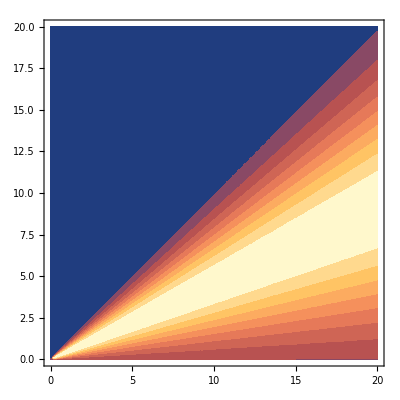

```mathematica
ContourPlot[f[ere,etrue],{etrue,0,20},{ere,0,20},ContourLines->False]//Quiet
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

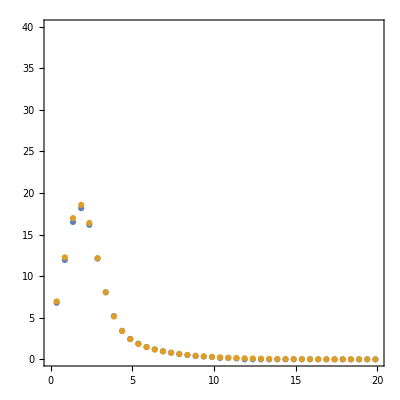

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### Introducing NSI

```mathematica
(* choosing Subscript[ϵ, μτ] only real *)
```

```mathematica
ratio[epS_,ee_]=(-1.3417950781553514+ee (63.6110167803427+(-11.335620650792169+0.48602694541668334 ee) ee)-26.253111607723554 epS+ee (653.3344894860501+ee (-102.78730074393953+4.450961331828265 ee)) epS+(525.5392109465565+ee (50842.27469116989+ee (-8729.640428648672+374.686356791237 ee))) epS^2+(1.3417950781553512+ee (-63.61101678034271+(11.335620650792173-0.48602694541668334 ee) ee)-47.198323815726795 epS+ee (-627.2311837169866+(102.78730074393945-4.450961331828264 ee) ee) epS+(377.44952730016934+ee (47657.51492975174+ee (-8263.66745442748+354.3136432087616 ee))) epS^2) Cos[8.323065282815573/ee]+(-10.918891490242757+ee (3.916905079979295+(-0.17249070990867868-2.1684043449710455*^-19 ee) ee)-59.87086539190307 epS+ee (-21.189965718249404+(-0.7854585909514353-0.06547117846490069 ee) ee) epS+(7086.844664530483+ee (-1565.9397835413793+125.74572752342468 ee)) epS^2) Sin[8.323065282815573/ee])/(-1.3417950781553516+ee (63.61101678034271+(-11.33562065079217+0.48602694541668334 ee) ee)+(1.3417950781553507+ee (-63.611016780342716+(11.335620650792173-0.4860269454166834 ee) ee)) Cos[8.323065282815573/ee]+(-10.918891490242876+ee (3.916905079979277+(-0.17249070990867785-2.1684043449710344*^-19 ee) ee)) Sin[8.323065282815573/ee]);
```

### Plot NSI

```mathematica
(*limite on Subscript[ϵ̃, 23] : 0.08 from my paper with JS *)
(* Subscript[ϵ̃, 23] = Subscript[p, μ] Subscript[ϵ, 23] = 27 Subscript[ϵ, 23] *)
```

```mathematica
Solve[0.08==x*27,x]
```

{{x→0.00296296}}

```mathematica
nsi=0.003;
nsi2=nsi*10;
nsi3=nsi*100;
```

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

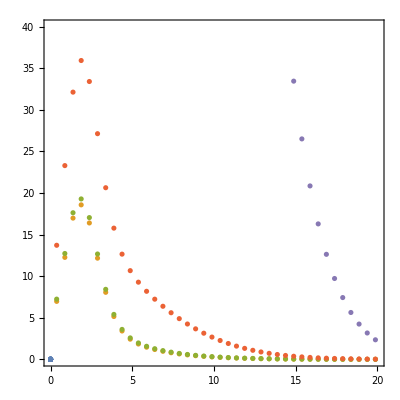

```mathematica
dataNSI=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI2=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi2,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI3=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi3,.5*i],{i,40}]},{j,40}]//Quiet;
ListPlot[{data*0,dataT,dataNSI,dataNSI2,dataNSI3},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
Transpose[{dataT[[All,2]],dataNSI[[All,2]]}]//Chop
```

{{6.97108,7.24059},{12.2612,12.7273},{16.9807,17.6248},{18.5749,19.2868},{16.398,17.0425},{12.1658,12.6663},{8.06067,8.41777},{5.15012,5.40323},{3.41041,3.59934},{2.42756,2.57819},{1.84576,1.97171},{1.46299,1.57092},{1.18441,1.27779},{0.968088,1.04902},{0.794312,0.864338},{0.65239,0.71278},{0.535537,0.587395},{0.438937,0.483254},{0.358948,0.396624},{0.292705,0.324558},{0.237899,0.264676},{0.192641,0.215017},{0.155364,0.173949},{0.124757,0.140098},{0.0997192,0.112303},{0.0793215,0.0895775},{0.0627787,0.0710833},{0.0494268,0.0561073},{0.0387054,0.0440439},{0.0301422,0.0343799},{0.0233408,0.0266819},{0.0179696,0.0205861},{0.0137529,0.0157878},{0.0104624,0.0120341},{0.00791051,0.00911601},{0.00594381,0.00686191},{0.00443777,0.005132},{0.00329194,0.00381313},{0.00242592,0.00281434},{0.00177576,0.0020631}}

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi,.5*i]//Chop,ratio[nsi,.5*i]/NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi2,.5*i]//Chop,ratio[nsi2,.5*i]/NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi3,.5*i]//Chop,ratio[nsi3,.5*i]/NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.96499,1.032,1.06944},{1.11857,1.03541,0.925658},{1.16206,1.0709,0.921556},{1.04411,1.03588,0.992111},{1.03437,1.03356,0.999219},{1.03343,1.03349,1.00005},{1.03379,1.03419,1.00038},{1.03473,1.03534,1.00059},{1.03606,1.03683,1.00074},{1.03769,1.0386,1.00088},{1.0396,1.04064,1.001},{1.04176,1.04292,1.00111},{1.04416,1.04543,1.00122},{1.04679,1.04818,1.00133},{1.04965,1.05116,1.00144},{1.05274,1.05436,1.00154},{1.05605,1.05778,1.00164},{1.05958,1.06142,1.00174},{1.06333,1.06528,1.00183},{1.0673,1.06936,1.00193},{1.07149,1.07365,1.00202},{1.07589,1.07816,1.00211},{1.08051,1.08289,1.0022},{1.08534,1.08783,1.00229},{1.09039,1.09299,1.00238},{1.09566,1.09836,1.00247},{1.10114,1.10395,1.00255},{1.10683,1.10975,1.00264},{1.11274,1.11577,1.00272},{1.11887,1.122,1.0028},{1.1252,1.12844,1.00288},{1.13176,1.1351,1.00296},{1.13852,1.14198,1.00303},{1.1455,1.14906,1.00311},{1.1527,1.15636,1.00318},{1.1601,1.16388,1.00325},{1.16772,1.1716,1.00332},{1.17556,1.17955,1.00339},{1.18361,1.1877,1.00346},{1.19187,1.19607,1.00353}}

{{-0.0429542,1.40816,-32.7828},{13.4957,1.70903,0.126636},{16.0094,5.26588,0.328924},{2.40293,1.55673,0.647846},{1.42396,1.36176,0.956324},{1.36602,1.38727,1.01556},{1.43127,1.48343,1.03644},{1.54882,1.61982,1.04584},{1.70087,1.78655,1.05037},{1.88096,1.97954,1.05241},{2.0862,2.1968,1.05301},{2.31513,2.43727,1.05276},{2.56693,2.70032,1.05197},{2.84111,2.98558,1.05085},{3.13737,3.2928,1.04954},{3.4555,3.62181,1.04813},{3.79535,3.9725,1.04667},{4.15684,4.34478,1.04521},{4.53989,4.73858,1.04377},{4.94444,5.15388,1.04236},{5.37047,5.59062,1.04099},{5.81793,6.0488,1.03968},{6.2868,6.52837,1.03843},{6.77707,7.02933,1.03722},{7.28872,7.55167,1.03608},{7.82174,8.09537,1.03498},{8.37612,8.66043,1.03394},{8.95186,9.24684,1.03295},{9.54894,9.85459,1.03201},{10.1674,10.4837,1.03111},{10.8071,11.1341,1.03026},{11.4682,11.8058,1.02944},{12.1506,12.4989,1.02867},{12.8543,13.2133,1.02793},{13.5794,13.949,1.02722},{14.3258,14.7061,1.02655},{15.0935,15.4844,1.0259},{15.8825,16.2841,1.02529},{16.6928,17.1051,1.0247},{17.5245,17.9474,1.02413}}

{{-45.3577,13.8956,-0.306355},{1256.95,43.58,0.0346711},{1489.97,399.342,0.26802},{111.209,26.3645,0.237071},{13.2696,7.23657,0.545348},{7.82947,10.1108,1.29137},{14.6461,19.9878,1.36472},{26.6371,33.8402,1.27042},{42.0383,50.6939,1.2059},{60.2143,70.1485,1.16498},{80.8847,92.0121,1.13757},{103.908,116.182,1.11813},{129.206,142.601,1.10367},{156.732,171.231,1.0925},{186.458,202.049,1.08362},{218.365,235.041,1.07637},{252.439,270.196,1.07034},{288.671,307.505,1.06524},{327.056,346.964,1.06087},{367.588,388.569,1.05708},{410.265,432.317,1.05375},{455.082,478.205,1.05081},{502.04,526.231,1.04819},{551.135,576.394,1.04583},{602.366,628.694,1.04371},{655.733,683.128,1.04178},{711.235,739.697,1.04002},{768.871,798.4,1.03841},{828.64,859.236,1.03692},{890.542,922.204,1.03555},{954.577,987.306,1.03429},{1020.74,1054.54,1.03311},{1089.04,1123.9,1.03201},{1159.48,1195.4,1.03098},{1232.04,1269.03,1.03003},{1306.73,1344.79,1.02912},{1383.56,1422.68,1.02828},{1462.52,1502.71,1.02748},{1543.61,1584.86,1.02673},{1626.83,1669.15,1.02601}}

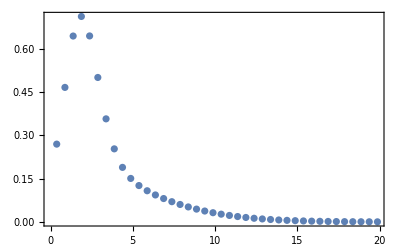

```mathematica
ListPlot[Transpose@{dataT[[All,1]],-dataT[[All,2]]+dataNSI[[All,2]]},Frame->True]
```

```mathematica
Manipulate[Plot[ratio[eps,ee],{ee,.5,20},Frame->True],{eps,0,10^-1}]
```

### Checks

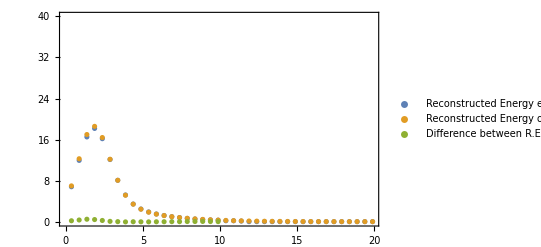

```mathematica
ListPlot[{data,dataT,Transpose[{data[[1;;20,1]],(dataT[[1;;20,2]]-data[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy extracted from figure","Reconstructed Energy obtained internally","Difference between R.E. obtained internally and extracted from figure"},PlotRange->{All,range}]
```

The NSI modulus is 0.003

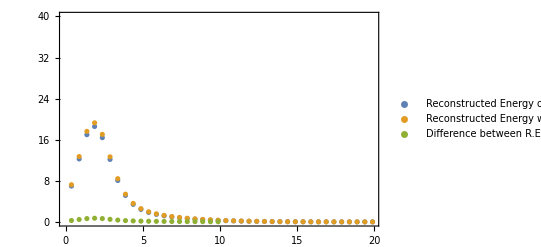

```mathematica
Print["The NSI modulus is ",nsi];ListPlot[{dataT,dataNSI,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.03

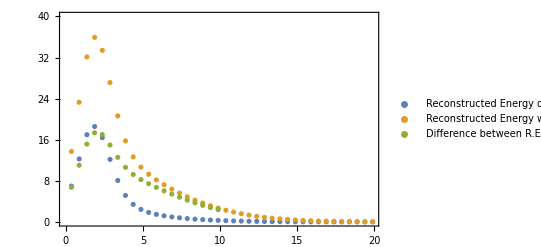

```mathematica
Print["The NSI modulus is ",nsi2];ListPlot[{dataT,dataNSI2,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI2[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.3

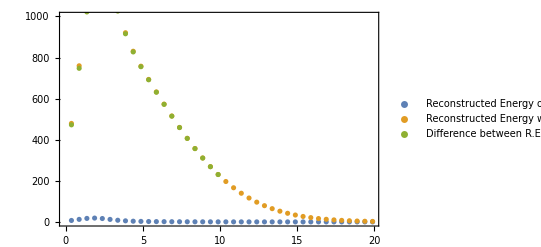

```mathematica
Print["The NSI modulus is ",nsi3];ListPlot[{dataT,dataNSI3,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI3[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,{0,1000}}]
```

### General Probabilitly ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passo=.4/10;
dataGen={};dataGenNSI={};dataGenNSI2={};dataGenNSIp={};dataGenNSI2p={};ls23={};
Do[ss23=(0.582)-.2+passo*i;delta=-2.5;AppendTo[ls23,ss23];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi2,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSIp,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2p,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi2,.5*i],{i,40}]},{j,40}]],{i,0,10}];
```

0.003

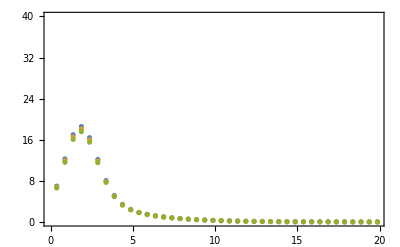
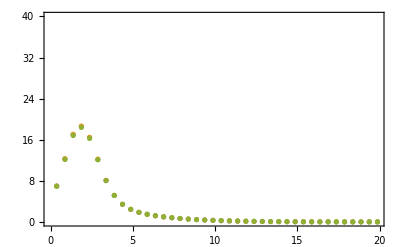
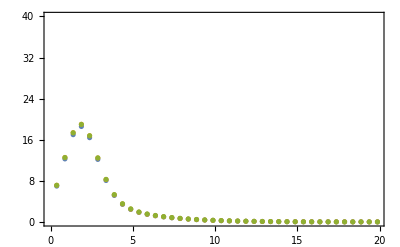
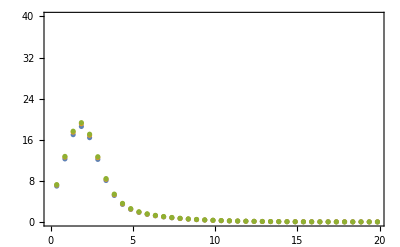
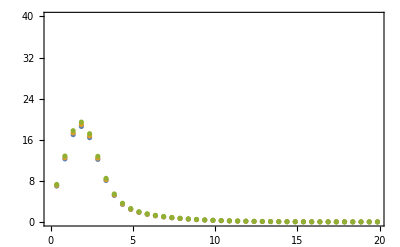
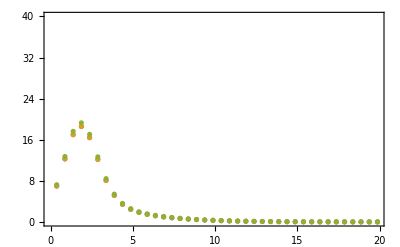
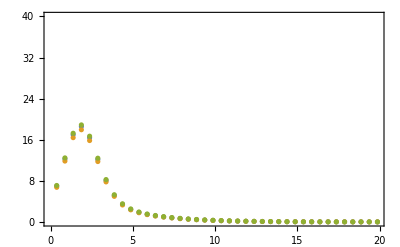
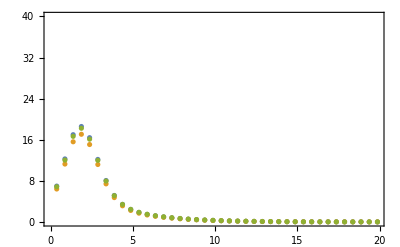

0.03

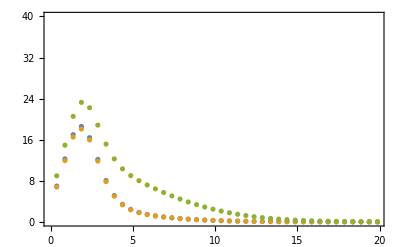
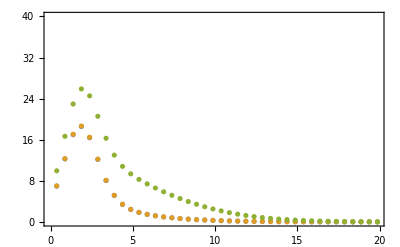
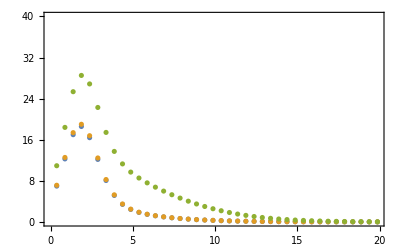
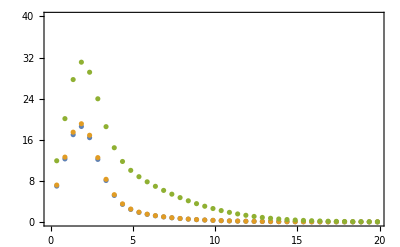
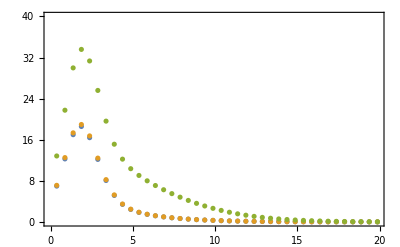
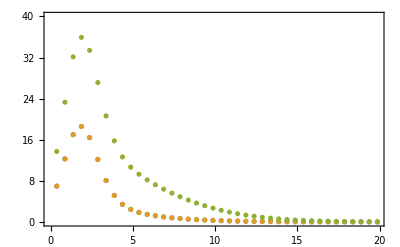
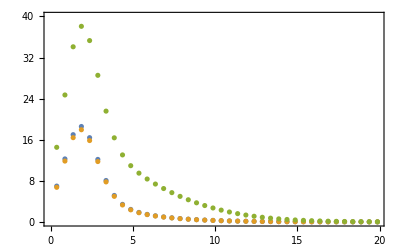
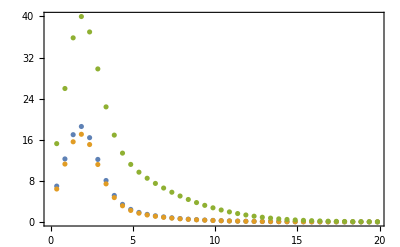

-0.003

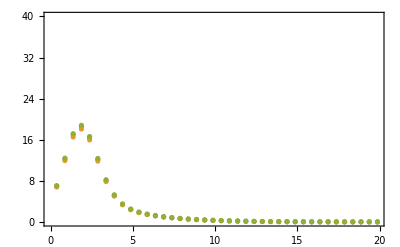
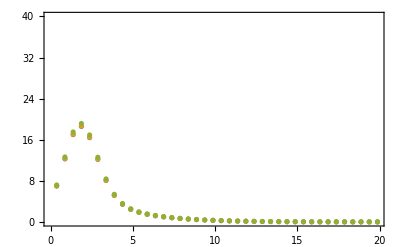
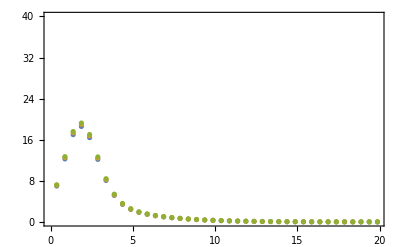
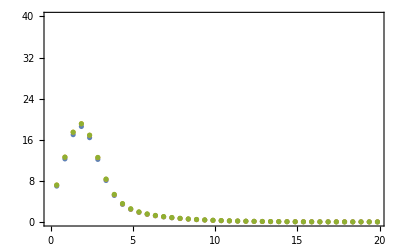
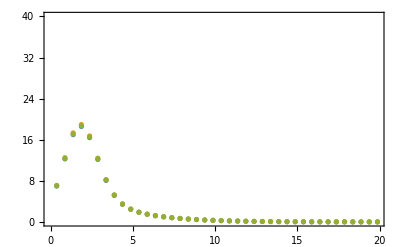
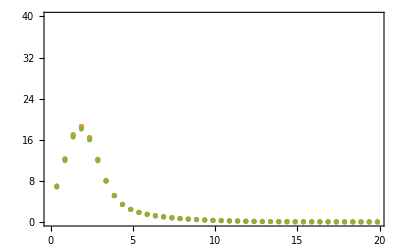
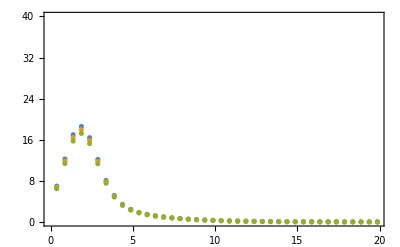
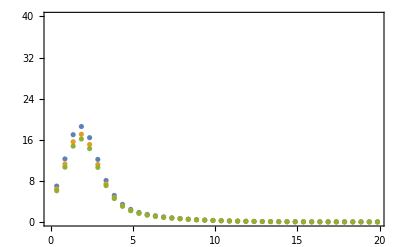

```mathematica
Print[nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[nsi2]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI2[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[-nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSIp[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
```

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.877206,0.962429,1.09715},{1.02851,1.03866,1.00988},{1.20426,0.84678,0.703154},{0.916722,0.953288,1.03989},{0.970634,0.984752,1.01455},{0.995329,1.00489,1.00961},{1.01309,1.02082,1.00763},{1.02787,1.03465,1.0066},{1.04103,1.04724,1.00597},{1.0532,1.05905,1.00555},{1.06471,1.0703,1.00525},{1.07576,1.08117,1.00502},{1.08647,1.09174,1.00485},{1.09693,1.10208,1.0047},{1.10718,1.11226,1.00458},{1.11728,1.12229,1.00448},{1.12725,1.1322,1.00439},{1.13712,1.14202,1.00431},{1.1469,1.15176,1.00424},{1.1566,1.16144,1.00418},{1.16625,1.17105,1.00412},{1.17584,1.18062,1.00407},{1.18539,1.19015,1.00402},{1.19489,1.19963,1.00397},{1.20436,1.20909,1.00392},{1.21381,1.21852,1.00388},{1.22322,1.22792,1.00384},{1.23261,1.2373,1.0038},{1.24198,1.24666,1.00377},{1.25133,1.256,1.00373},{1.26066,1.26532,1.0037},{1.26998,1.27463,1.00366},{1.27928,1.28393,1.00363},{1.28857,1.29321,1.0036},{1.29785,1.30248,1.00357},{1.30711,1.31174,1.00354},{1.31637,1.321,1.00351},{1.32562,1.33024,1.00349},{1.33486,1.33948,1.00346},{1.34409,1.34871,1.00343}}

{{0.655419,0.748632,1.14222},{0.810253,0.818672,1.01039},{0.967969,0.646053,0.667431},{0.708962,0.741793,1.04631},{0.757298,0.769893,1.01663},{0.779296,0.787785,1.01089},{0.795048,0.801892,1.00861},{0.808115,0.814106,1.00741},{0.819732,0.825215,1.00669},{0.830462,0.835613,1.0062},{0.840604,0.845526,1.00586},{0.850332,0.855088,1.00559},{0.859758,0.86439,1.00539},{0.868956,0.873492,1.00522},{0.877976,0.882437,1.00508},{0.886856,0.891257,1.00496},{0.895623,0.899974,1.00486},{0.904297,0.908607,1.00477},{0.912894,0.91717,1.00468},{0.921426,0.925674,1.00461},{0.929904,0.934126,1.00454},{0.938334,0.942536,1.00448},{0.946725,0.950907,1.00442},{0.95508,0.959246,1.00436},{0.963404,0.967557,1.00431},{0.971701,0.975841,1.00426},{0.979974,0.984104,1.00421},{0.988226,0.992346,1.00417},{0.99646,1.00057,1.00413},{1.00468,1.00878,1.00408},{1.01288,1.01697,1.00404},{1.02106,1.02515,1.004},{1.02924,1.03332,1.00397},{1.0374,1.04148,1.00393},{1.04555,1.04963,1.0039},{1.0537,1.05777,1.00386},{1.06183,1.0659,1.00383},{1.06996,1.07402,1.0038},{1.07808,1.08213,1.00376},{1.08619,1.09024,1.00373}}

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0417651,0.00127844,0.0302018,0.045592,0.0243565,0,0.0669707,0.393879,1.24978,3.05311,6.46513}

InterpolatingFunction[…]

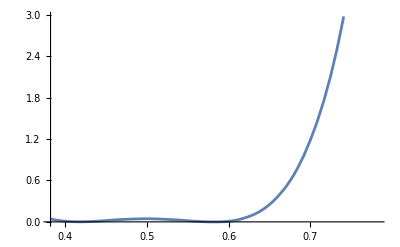

```mathematica
Table[{ls23[[i]],{chis23[[i]]}},{i,Length@ls23}];
Interpolation@%
Plot[%[x],{x,ls23[[1]],ls23[[-1]]}]
```

```mathematica
chiNSI=Table[Sum[dataGenNSI[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0380715,0.016042,0.013119,0.0295052,0.0653829,0.120937,0.196377,0.291966,0.408066,0.545208,0.704232}

{50.2196,54.2052,59.5398,66.2571,74.3762,83.9034,94.8329,107.147,120.815,135.788,151.994}

{0.134069,0.0747352,0.0353852,0.0157527,0.015595,0.0346672,0.0726948,0.129339,0.204146,0.296455,0.405233}

{86.171,76.2318,67.7091,60.5938,54.8634,50.4804,47.3902,45.5207,44.7887,45.1249,46.5518}

```mathematica
chis23NSI=Table[Sum[dataGenNSI[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.145607,0.0130478,0.0557808,0.131812,0.161555,0.120936,0.0418771,0.0205965,0.236567,0.98918,2.76826}

{48.6736,54.5243,61.267,68.6088,76.2534,83.9034,91.2583,98.01,103.835,108.383,111.258}

{0.0344902,0.0938085,0.117281,0.0831128,0.0254034,0.0346676,0.265912,0.956332,2.45797,5.29697,10.2857}

{83.5249,76.6689,69.6468,62.7507,56.268,50.4804,45.6579,42.0428,39.8182,39.049,39.5855}

```mathematica
Join[Table[{ls23[[i]],nsi,{chis23NSI[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi2,{chis23NSI2[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi,{chis23NSIp[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi2,{chis23NSI2p[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi*0,{chis23[[i]]}},{i,Length@ls23}]];
func=Interpolation@%
```

InterpolatingFunction[…]

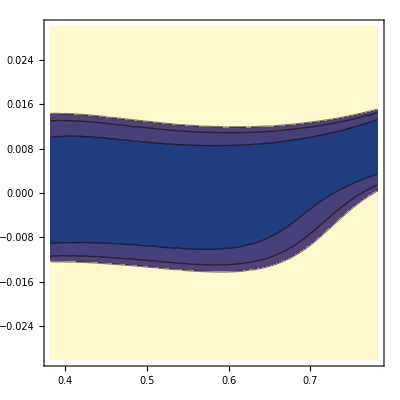

```mathematica
ContourPlot[func[s23,nsii],{s23,ls23[[1]],ls23[[-1]]},{nsii,-.03,.03},Contours->{2.3,4.6,6.}]
```

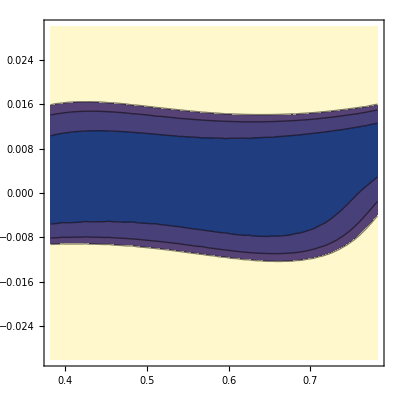

```mathematica
-
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=-2.5-1.+passodelta*k;AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

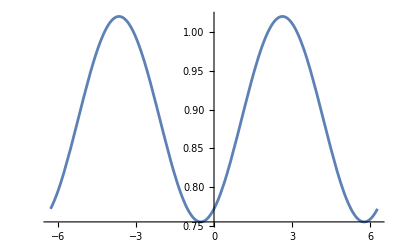

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

35

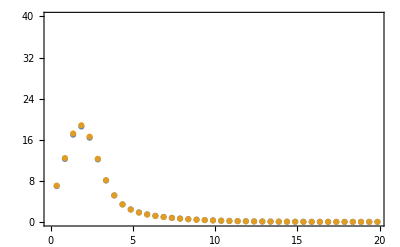

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.388688,0.128467,0.0204679,0.015481,0.0653107,0.12983,0.182048,0.211072,0.222916,0.239223,0.294002,0.168682,0.0213053,0.00806994,0.0776656,0.180342,0.274922,0.333861,0.346207,0.318417,0.273087,0.245708,0.0895912,0.0073862,0.0489266,0.161663,0.294925,0.406915,0.469759,0.472466,0.421752,0.340776,0.265897,0.0724878,0.0102742,0.0686238,0.194604,0.337258,0.454595,0.51864,0.518389,0.460639,0.368721,0.279264,0.0938652,0.00720276,0.0449956,0.15478,0.285949,0.396747,0.459323,0.462689,0.413544,0.335007,0.263379,0.182515,0.0260575,0.00519212,0.0687802,0.167198,0.259355,0.317752,0.33144,0.306842,0.266477,0.245714,0.423364,0.14908,0.0292794,0.0150083,0.0582625,0.119043,0.170427,0.201529,0.218307,0.242287,0.307296,0.969389,0.524375,0.26142,0.134623,0.0982298,0.113756,0.155076,0.211378,0.287968,0.404969,0.594039,2.06537,1.38882,0.932133,0.653306,0.509458,0.464024,0.491881,0.582297,0.73972,0.982451,1.33933,4.09204,3.11066,2.39964,1.92169,1.63738,1.51243,1.52289,1.65811,1.92145,2.32895,2.90596,7.65016,6.27044,5.22837,4.49209,4.02603,3.7985,3.78683,3.98038,4.38121,5.00265,5.8659}

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}]
```

{{{0.382,-3.5},{0.388688}},{{0.382,-3.3},{0.128467}},{{0.382,-3.1},{0.0204679}},{{0.382,-2.9},{0.015481}},{{0.382,-2.7},{0.0653107}},{{0.382,-2.5},{0.12983}},{{0.382,-2.3},{0.182048}},{{0.382,-2.1},{0.211072}},{{0.382,-1.9},{0.222916}},{{0.382,-1.7},{0.239223}},{{0.382,-1.5},{0.294002}},{{0.422,-3.5},{0.168682}},{{0.422,-3.3},{0.0213053}},{{0.422,-3.1},{0.00806994}},{{0.422,-2.9},{0.0776656}},{{0.422,-2.7},{0.180342}},{{0.422,-2.5},{0.274922}},{{0.422,-2.3},{0.333861}},{{0.422,-2.1},{0.346207}},{{0.422,-1.9},{0.318417}},{{0.422,-1.7},{0.273087}},{{0.422,-1.5},{0.245708}},{{0.462,-3.5},{0.0895912}},{{0.462,-3.3},{0.0073862}},{{0.462,-3.1},{0.0489266}},{{0.462,-2.9},{0.161663}},{{0.462,-2.7},{0.294925}},{{0.462,-2.5},{0.406915}},{{0.462,-2.3},{0.469759}},{{0.462,-2.1},{0.472466}},{{0.462,-1.9},{0.421752}},{{0.462,-1.7},{0.340776}},{{0.462,-1.5},{0.265897}},{{0.502,-3.5},{0.0724878}},{{0.502,-3.3},{0.0102742}},{{0.502,-3.1},{0.0686238}},{{0.502,-2.9},{0.194604}},{{0.502,-2.7},{0.337258}},{{0.502,-2.5},{0.454595}},{{0.502,-2.3},{0.51864}},{{0.502,-2.1},{0.518389}},{{0.502,-1.9},{0.460639}},{{0.502,-1.7},{0.368721}},{{0.502,-1.5},{0.279264}},{{0.542,-3.5},{0.0938652}},{{0.542,-3.3},{0.00720276}},{{0.542,-3.1},{0.0449956}},{{0.542,-2.9},{0.15478}},{{0.542,-2.7},{0.285949}},{{0.542,-2.5},{0.396747}},{{0.542,-2.3},{0.459323}},{{0.542,-2.1},{0.462689}},{{0.542,-1.9},{0.413544}},{{0.542,-1.7},{0.335007}},{{0.542,-1.5},{0.263379}},{{0.582,-3.5},{0.182515}},{{0.582,-3.3},{0.0260575}},{{0.582,-3.1},{0.00519212}},{{0.582,-2.9},{0.0687802}},{{0.582,-2.7},{0.167198}},{{0.582,-2.5},{0.259355}},{{0.582,-2.3},{0.317752}},{{0.582,-2.1},{0.33144}},{{0.582,-1.9},{0.306842}},{{0.582,-1.7},{0.266477}},{{0.582,-1.5},{0.245714}},{{0.622,-3.5},{0.423364}},{{0.622,-3.3},{0.14908}},{{0.622,-3.1},{0.0292794}},{{0.622,-2.9},{0.0150083}},{{0.622,-2.7},{0.0582625}},{{0.622,-2.5},{0.119043}},{{0.622,-2.3},{0.170427}},{{0.622,-2.1},{0.201529}},{{0.622,-1.9},{0.218307}},{{0.622,-1.7},{0.242287}},{{0.622,-1.5},{0.307296}},{{0.662,-3.5},{0.969389}},{{0.662,-3.3},{0.524375}},{{0.662,-3.1},{0.26142}},{{0.662,-2.9},{0.134623}},{{0.662,-2.7},{0.0982298}},{{0.662,-2.5},{0.113756}},{{0.662,-2.3},{0.155076}},{{0.662,-2.1},{0.211378}},{{0.662,-1.9},{0.287968}},{{0.662,-1.7},{0.404969}},{{0.662,-1.5},{0.594039}},{{0.702,-3.5},{2.06537}},{{0.702,-3.3},{1.38882}},{{0.702,-3.1},{0.932133}},{{0.702,-2.9},{0.653306}},{{0.702,-2.7},{0.509458}},{{0.702,-2.5},{0.464024}},{{0.702,-2.3},{0.491881}},{{0.702,-2.1},{0.582297}},{{0.702,-1.9},{0.73972}},{{0.702,-1.7},{0.982451}},{{0.702,-1.5},{1.33933}},{{0.742,-3.5},{4.09204}},{{0.742,-3.3},{3.11066}},{{0.742,-3.1},{2.39964}},{{0.742,-2.9},{1.92169}},{{0.742,-2.7},{1.63738}},{{0.742,-2.5},{1.51243}},{{0.742,-2.3},{1.52289}},{{0.742,-2.1},{1.65811}},{{0.742,-1.9},{1.92145}},{{0.742,-1.7},{2.32895}},{{0.742,-1.5},{2.90596}},{{0.782,-3.5},{7.65016}},{{0.782,-3.3},{6.27044}},{{0.782,-3.1},{5.22837}},{{0.782,-2.9},{4.49209}},{{0.782,-2.7},{4.02603}},{{0.782,-2.5},{3.7985}},{{0.782,-2.3},{3.78683}},{{0.782,-2.1},{3.98038}},{{0.782,-1.9},{4.38121}},{{0.782,-1.7},{5.00265}},{{0.782,-1.5},{5.8659}}}

InterpolatingFunction[…]

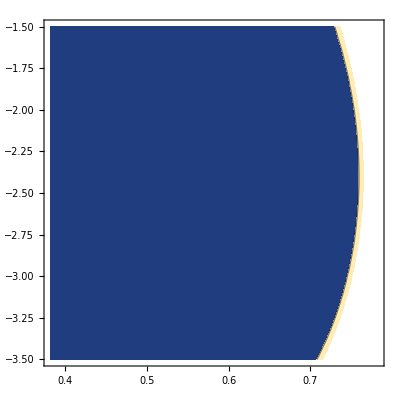

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

### Check probability

```mathematica
ratioGen[S23,dcp,0,ee]
Table[ratioGen[0.582,-2.15,0,ee],{ee,1,10}]
```

(0.-0.555354 ee √(1-S23) √S23 Cos[dcp]+ee (0.-8.22111 S23+8.22111 S23^2+0.555354 √(1-S23) √S23 Cos[dcp]) Cos[8.32307/ee]+S23 (0.+8.22111 ee-1.44661 Sin[8.32307/ee])-0.555354 ee √(1-S23) √S23 Sin[dcp] Sin[8.32307/ee]+S23^2 (0.-8.22111 ee+1.44661 Sin[8.32307/ee]))/(2.26532 ee-2.26532 ee Cos[8.32307/ee]+1.11022×10^-16 ee Cos[16.6461/ee]-0.351926 Sin[8.32307/ee])

{1.01241,0.89694,0.967545,1.00861,1.04238,1.07306,1.10209,1.13014,1.15755,1.18452}

## All data sets - s23 and dcp

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

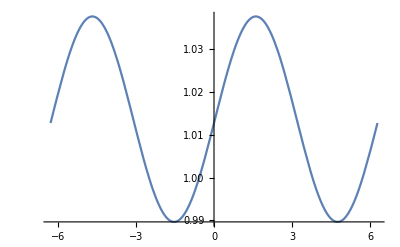

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

22

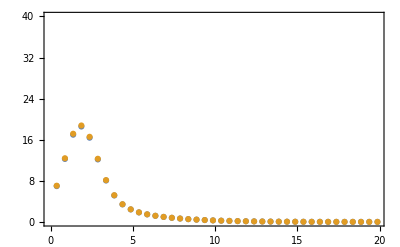

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0269286,0.0414439,0.0546922,0.0590627,0.0517798,0.0375102,0.023947,0.0157719,0.0135848,0.0171438,0.0269286,0.0056676,0.00133194,0.000107268,0.0000329362,0.000429671,0.0031485,0.00906881,0.0151177,0.0165889,0.0122312,0.0056676,0.0449538,0.0304462,0.0223745,0.0215057,0.0278334,0.0410531,0.057733,0.0704003,0.0719369,0.0614263,0.0449538,0.0628698,0.0458753,0.0367736,0.0368328,0.0460479,0.0631183,0.0828531,0.0963322,0.0962381,0.0826239,0.0628698,0.0370159,0.0245518,0.018702,0.0195993,0.0272754,0.0411252,0.0569,0.0669108,0.0652744,0.0529805,0.0370159,0.00131191,3.64809×10^-7,0.000313918,0.000141566,0.000295057,0.00315588,0.00837354,0.0119981,0.0106981,0.00569659,0.00131191,0.0503586,0.0666857,0.0747837,0.0696868,0.0544903,0.0375623,0.0257877,0.0213887,0.024219,0.0343157,0.0503586,0.352629,0.393232,0.409448,0.393344,0.352673,0.305674,0.270355,0.25757,0.270512,0.305796,0.352629,1.17667,1.2487,1.272,1.23608,1.15679,1.0673,1.0014,0.981226,1.01293,1.08649,1.17667,2.93985,3.05155,3.07931,3.01116,2.87591,2.7283,2.62382,2.59879,2.66142,2.79052,2.93985,6.30146,6.46301,6.49067,6.37271,6.15787,5.93154,5.77859,5.75318,5.86391,6.07205,6.30146}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

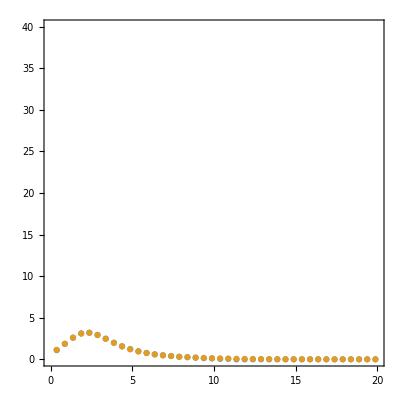

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

92

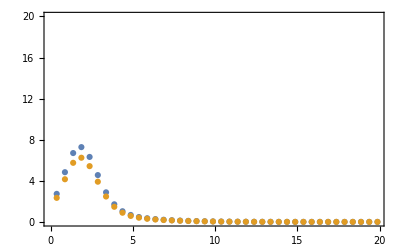

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

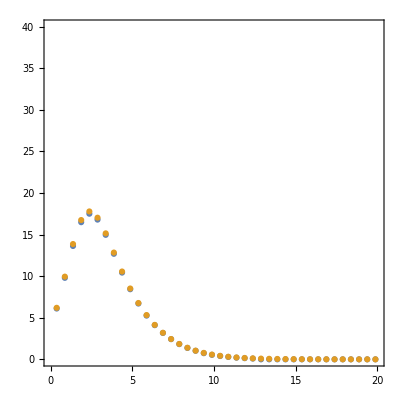

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

85

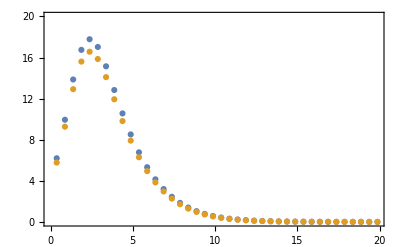

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0420292,0.0573772,0.0719694,0.0784319,0.0730937,0.0590644,0.0435542,0.0325554,0.0284762,0.0316937,0.0420292,0.00608709,0.00199269,0.000386975,0.000146651,0.000594144,0.00282837,0.0075367,0.0126028,0.0143678,0.0114022,0.00608709,0.0574899,0.0431901,0.0345179,0.0331331,0.0391966,0.0518222,0.0674257,0.0793865,0.0815003,0.0725985,0.0574899,0.0813286,0.0647588,0.0555319,0.0556253,0.0650224,0.0816927,0.100201,0.112502,0.11237,0.0998752,0.0813286,0.0464273,0.0345649,0.0289949,0.0304298,0.0387284,0.0523833,0.0667885,0.0751677,0.0729261,0.0613197,0.0464273,0.000866511,2.20338×10^-7,0.000158924,0.0000301403,0.000474013,0.00306487,0.00707227,0.00939573,0.00791739,0.00399815,0.000866511,0.0781431,0.0941104,0.0999529,0.092391,0.0755613,0.0576978,0.0454874,0.0417207,0.0468085,0.0600335,0.0781431,0.515763,0.55419,0.563437,0.539181,0.492429,0.442886,0.408878,0.401195,0.421999,0.465053,0.515763,1.69215,1.75874,1.76658,1.71221,1.61873,1.52371,1.46229,1.45536,1.50512,1.59485,1.69215,4.19535,4.29628,4.29478,4.19142,4.02871,3.87066,3.77578,3.77731,3.87465,4.0336,4.19535,8.95409,9.09667,9.07375,8.89467,8.6318,8.38739,8.25197,8.27373,8.44493,8.70408,8.95409}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,-3.14159},{0.382,-2.51327},{0.382,-1.88496},{0.382,-1.25664},{0.382,-0.628319},{0.382,0.},{0.382,0.628319},{0.382,1.25664},{0.382,1.88496},{0.382,2.51327},{0.382,3.14159},{0.422,-3.14159},{0.422,-2.51327},{0.422,-1.88496},{0.422,-1.25664},{0.422,-0.628319},{0.422,0.},{0.422,0.628319},{0.422,1.25664},{0.422,1.88496},{0.422,2.51327},{0.422,3.14159},{0.462,-3.14159},{0.462,-2.51327},{0.462,-1.88496},{0.462,-1.25664},{0.462,-0.628319},{0.462,0.},{0.462,0.628319},{0.462,1.25664},{0.462,1.88496},{0.462,2.51327},{0.462,3.14159},{0.502,-3.14159},{0.502,-2.51327},{0.502,-1.88496},{0.502,-1.25664},{0.502,-0.628319},{0.502,0.},{0.502,0.628319},{0.502,1.25664},{0.502,1.88496},{0.502,2.51327},{0.502,3.14159},{0.542,-3.14159},{0.542,-2.51327},{0.542,-1.88496},{0.542,-1.25664},{0.542,-0.628319},{0.542,0.},{0.542,0.628319},{0.542,1.25664},{0.542,1.88496},{0.542,2.51327},{0.542,3.14159},{0.582,-3.14159},{0.582,-2.51327},{0.582,-1.88496},{0.582,-1.25664},{0.582,-0.628319},{0.582,0.},{0.582,0.628319},{0.582,1.25664},{0.582,1.88496},{0.582,2.51327},{0.582,3.14159},{0.622,-3.14159},{0.622,-2.51327},{0.622,-1.88496},{0.622,-1.25664},{0.622,-0.628319},{0.622,0.},{0.622,0.628319},{0.622,1.25664},{0.622,1.88496},{0.622,2.51327},{0.622,3.14159},{0.662,-3.14159},{0.662,-2.51327},{0.662,-1.88496},{0.662,-1.25664},{0.662,-0.628319},{0.662,0.},{0.662,0.628319},{0.662,1.25664},{0.662,1.88496},{0.662,2.51327},{0.662,3.14159},{0.702,-3.14159},{0.702,-2.51327},{0.702,-1.88496},{0.702,-1.25664},{0.702,-0.628319},{0.702,0.},{0.702,0.628319},{0.702,1.25664},{0.702,1.88496},{0.702,2.51327},{0.702,3.14159},{0.742,-3.14159},{0.742,-2.51327},{0.742,-1.88496},{0.742,-1.25664},{0.742,-0.628319},{0.742,0.},{0.742,0.628319},{0.742,1.25664},{0.742,1.88496},{0.742,2.51327},{0.742,3.14159},{0.782,-3.14159},{0.782,-2.51327},{0.782,-1.88496},{0.782,-1.25664},{0.782,-0.628319},{0.782,0.},{0.782,0.628319},{0.782,1.25664},{0.782,1.88496},{0.782,2.51327},{0.782,3.14159}}

```mathematica
dataSet1
```

{0.0269286,0.0414439,0.0546922,0.0590627,0.0517798,0.0375102,0.023947,0.0157719,0.0135848,0.0171438,0.0269286,0.0056676,0.00133194,0.000107268,0.0000329362,0.000429671,0.0031485,0.00906881,0.0151177,0.0165889,0.0122312,0.0056676,0.0449538,0.0304462,0.0223745,0.0215057,0.0278334,0.0410531,0.057733,0.0704003,0.0719369,0.0614263,0.0449538,0.0628698,0.0458753,0.0367736,0.0368328,0.0460479,0.0631183,0.0828531,0.0963322,0.0962381,0.0826239,0.0628698,0.0370159,0.0245518,0.018702,0.0195993,0.0272754,0.0411252,0.0569,0.0669108,0.0652744,0.0529805,0.0370159,0.00131191,3.64809×10^-7,0.000313918,0.000141566,0.000295057,0.00315588,0.00837354,0.0119981,0.0106981,0.00569659,0.00131191,0.0503586,0.0666857,0.0747837,0.0696868,0.0544903,0.0375623,0.0257877,0.0213887,0.024219,0.0343157,0.0503586,0.352629,0.393232,0.409448,0.393344,0.352673,0.305674,0.270355,0.25757,0.270512,0.305796,0.352629,1.17667,1.2487,1.272,1.23608,1.15679,1.0673,1.0014,0.981226,1.01293,1.08649,1.17667,2.93985,3.05155,3.07931,3.01116,2.87591,2.7283,2.62382,2.59879,2.66142,2.79052,2.93985,6.30146,6.46301,6.49067,6.37271,6.15787,5.93154,5.77859,5.75318,5.86391,6.07205,6.30146}

```mathematica
dataSet2
```

{0.00955227,0.0151173,0.0201663,0.0217431,0.0188223,0.0132932,0.00815678,0.00515131,0.00440894,0.00580177,0.00955227,0.00216988,0.000479221,0.0000261919,6.42941×10^-6,0.000156884,0.00123485,0.0035913,0.00598536,0.00653895,0.00477735,0.00216988,0.0166804,0.0110593,0.0079711,0.00766309,0.0101235,0.0152672,0.0217762,0.0267139,0.0272771,0.0231249,0.0166804,0.0232723,0.0166782,0.0131663,0.0131873,0.01674,0.0233622,0.0310603,0.0363371,0.0363028,0.0309769,0.0232723,0.0137825,0.00893046,0.00665395,0.00697184,0.00990586,0.015272,0.021447,0.0254073,0.024807,0.0200147,0.0137825,0.000531912,1.49034×10^-7,0.000129918,0.0000609186,0.000104732,0.00122679,0.00331186,0.00478509,0.00429141,0.00229689,0.000531912,0.017911,0.024242,0.0274947,0.0256572,0.0198707,0.0133784,0.00885252,0.00711922,0.00809046,0.0118224,0.017911,0.127176,0.14299,0.149636,0.14385,0.128455,0.110425,0.0967018,0.0914851,0.0960625,0.109281,0.127176,0.425975,0.454119,0.46396,0.451067,0.421182,0.386883,0.361171,0.352656,0.363938,0.391501,0.425975,1.06608,1.10985,1.12216,1.09771,1.04691,0.99041,0.949501,0.93839,0.96073,1.00903,1.06608,2.28724,2.35073,2.36415,2.32185,2.24138,2.15486,2.09479,2.08241,2.12196,2.19967,2.28724}

```mathematica
dataSet3
```

{0.0420292,0.0573772,0.0719694,0.0784319,0.0730937,0.0590644,0.0435542,0.0325554,0.0284762,0.0316937,0.0420292,0.00608709,0.00199269,0.000386975,0.000146651,0.000594144,0.00282837,0.0075367,0.0126028,0.0143678,0.0114022,0.00608709,0.0574899,0.0431901,0.0345179,0.0331331,0.0391966,0.0518222,0.0674257,0.0793865,0.0815003,0.0725985,0.0574899,0.0813286,0.0647588,0.0555319,0.0556253,0.0650224,0.0816927,0.100201,0.112502,0.11237,0.0998752,0.0813286,0.0464273,0.0345649,0.0289949,0.0304298,0.0387284,0.0523833,0.0667885,0.0751677,0.0729261,0.0613197,0.0464273,0.000866511,2.20338×10^-7,0.000158924,0.0000301403,0.000474013,0.00306487,0.00707227,0.00939573,0.00791739,0.00399815,0.000866511,0.0781431,0.0941104,0.0999529,0.092391,0.0755613,0.0576978,0.0454874,0.0417207,0.0468085,0.0600335,0.0781431,0.515763,0.55419,0.563437,0.539181,0.492429,0.442886,0.408878,0.401195,0.421999,0.465053,0.515763,1.69215,1.75874,1.76658,1.71221,1.61873,1.52371,1.46229,1.45536,1.50512,1.59485,1.69215,4.19535,4.29628,4.29478,4.19142,4.02871,3.87066,3.77578,3.77731,3.87465,4.0336,4.19535,8.95409,9.09667,9.07375,8.89467,8.6318,8.38739,8.25197,8.27373,8.44493,8.70408,8.95409}

### Contour

```mathematica
dataSet1;
```

```mathematica
dataSet2;
```

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

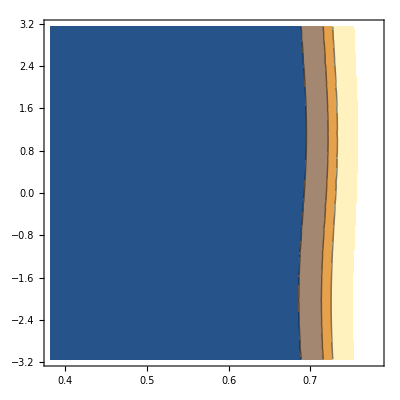

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

## All data sets - s23 and NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

11

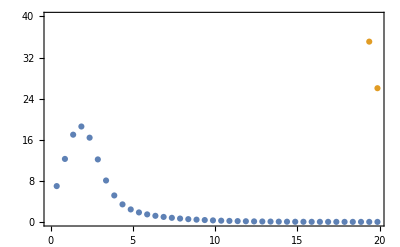

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{161975.,103633.,58225.4,25763.2,6281.58,0.0417651,5792.35,24764.2,56721.,101625.,159463.,159284.,101837.,57147.1,25224.8,6105.95,0.00127844,5801.76,24603.4,56211.2,100588.,157721.,157659.,100720.,56446.7,24850.7,5967.95,0.0302018,5855.3,24620.6,56100.1,100257.,157080.,157109.,100288.,56129.8,24644.6,5869.36,0.045592,5951.05,24811.6,56381.4,100624.,157529.,157642.,100550.,56201.8,24610.,5811.93,0.0243565,6087.22,25172.6,57049.1,101681.,159057.,159268.,101511.,56668.2,24750.8,5797.45,0,6262.,25699.6,58097.1,103419.,161655.,161996.,103181.,57534.8,25070.8,5827.83,0.0669707,6473.51,26388.7,59519.1,105830.,165310.,165837.,105566.,58807.9,25574.4,5905.17,0.393879,6719.75,27235.5,61308.7,108905.,170012.,170800.,108677.,60494.6,26266.2,6031.89,1.24978,6998.43,28235.3,63458.4,112633.,175749.,176901.,112523.,62603.,27152.,6210.84,3.05311,7306.86,29382.5,65959.6,117004.,182504.,184154.,117119.,65143.4,28238.4,6445.5,6.46513,7641.72,30670.2,68802.,122003.,190261.}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

19.775

19.4308

19.0148

1.03998

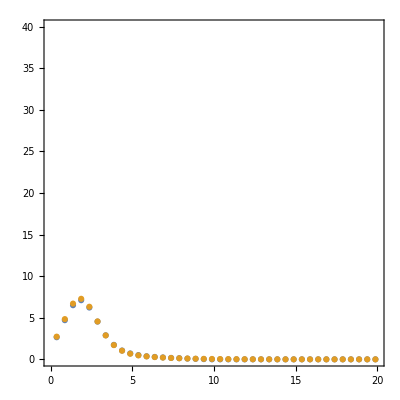

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

59

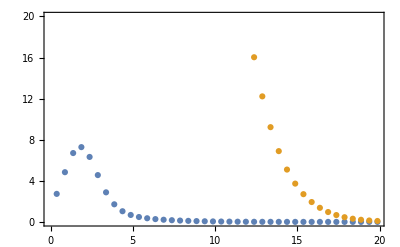

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

31

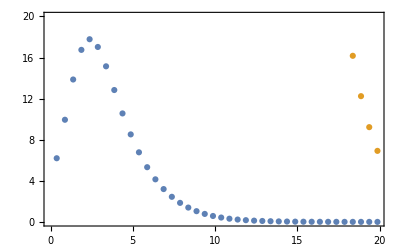

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{385993.,246953.,138767.,61450.7,15056.6,0.0577196,14347.1,60019.,136615.,244083.,382404.,382180.,244408.,137238.,60686.4,14804.8,0.00193435,14359.6,59787.9,135888.,242607.,379928.,379867.,242818.,136242.,60153.8,14606.5,0.0429381,14435.2,59808.1,135723.,242126.,379000.,379066.,242194.,135786.,59858.3,14464.4,0.0644759,14571.2,60073.9,136110.,242626.,379606.,379790.,242545.,135877.,59805.2,14381.1,0.0343767,14764.9,60579.6,137041.,244097.,381731.,382051.,243881.,136525.,59999.6,14359.2,0,15013.4,61319.6,138508.,246527.,385359.,385862.,246213.,137735.,60447.,14401.5,0.0943621,15314.,62288.1,140502.,249903.,390476.,391237.,249552.,139518.,61153.3,14511.,0.55473,15663.8,63478.8,143012.,254213.,397065.,398192.,253911.,141884.,62125.1,14690.9,1.75957,16059.2,64884.9,146030.,259443.,405108.,406745.,259306.,144842.,63370.1,14945.2,4.29738,16496.5,66498.4,149542.,265576.,414584.,416919.,265754.,148408.,64897.7,15278.5,9.09799,16970.9,68309.5,153533.,272591.,425467.}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,-1.},{0.382,-0.8},{0.382,-0.6},{0.382,-0.4},{0.382,-0.2},{0.382,0.},{0.382,0.2},{0.382,0.4},{0.382,0.6},{0.382,0.8},{0.382,1.},{0.422,-1.},{0.422,-0.8},{0.422,-0.6},{0.422,-0.4},{0.422,-0.2},{0.422,0.},{0.422,0.2},{0.422,0.4},{0.422,0.6},{0.422,0.8},{0.422,1.},{0.462,-1.},{0.462,-0.8},{0.462,-0.6},{0.462,-0.4},{0.462,-0.2},{0.462,0.},{0.462,0.2},{0.462,0.4},{0.462,0.6},{0.462,0.8},{0.462,1.},{0.502,-1.},{0.502,-0.8},{0.502,-0.6},{0.502,-0.4},{0.502,-0.2},{0.502,0.},{0.502,0.2},{0.502,0.4},{0.502,0.6},{0.502,0.8},{0.502,1.},{0.542,-1.},{0.542,-0.8},{0.542,-0.6},{0.542,-0.4},{0.542,-0.2},{0.542,0.},{0.542,0.2},{0.542,0.4},{0.542,0.6},{0.542,0.8},{0.542,1.},{0.582,-1.},{0.582,-0.8},{0.582,-0.6},{0.582,-0.4},{0.582,-0.2},{0.582,0.},{0.582,0.2},{0.582,0.4},{0.582,0.6},{0.582,0.8},{0.582,1.},{0.622,-1.},{0.622,-0.8},{0.622,-0.6},{0.622,-0.4},{0.622,-0.2},{0.622,0.},{0.622,0.2},{0.622,0.4},{0.622,0.6},{0.622,0.8},{0.622,1.},{0.662,-1.},{0.662,-0.8},{0.662,-0.6},{0.662,-0.4},{0.662,-0.2},{0.662,0.},{0.662,0.2},{0.662,0.4},{0.662,0.6},{0.662,0.8},{0.662,1.},{0.702,-1.},{0.702,-0.8},{0.702,-0.6},{0.702,-0.4},{0.702,-0.2},{0.702,0.},{0.702,0.2},{0.702,0.4},{0.702,0.6},{0.702,0.8},{0.702,1.},{0.742,-1.},{0.742,-0.8},{0.742,-0.6},{0.742,-0.4},{0.742,-0.2},{0.742,0.},{0.742,0.2},{0.742,0.4},{0.742,0.6},{0.742,0.8},{0.742,1.},{0.782,-1.},{0.782,-0.8},{0.782,-0.6},{0.782,-0.4},{0.782,-0.2},{0.782,0.},{0.782,0.2},{0.782,0.4},{0.782,0.6},{0.782,0.8},{0.782,1.}}

```mathematica
dataSet1
```

{161975.,103633.,58225.4,25763.2,6281.58,0.0417651,5792.35,24764.2,56721.,101625.,159463.,159284.,101837.,57147.1,25224.8,6105.95,0.00127844,5801.76,24603.4,56211.2,100588.,157721.,157659.,100720.,56446.7,24850.7,5967.95,0.0302018,5855.3,24620.6,56100.1,100257.,157080.,157109.,100288.,56129.8,24644.6,5869.36,0.045592,5951.05,24811.6,56381.4,100624.,157529.,157642.,100550.,56201.8,24610.,5811.93,0.0243565,6087.22,25172.6,57049.1,101681.,159057.,159268.,101511.,56668.2,24750.8,5797.45,0,6262.,25699.6,58097.1,103419.,161655.,161996.,103181.,57534.8,25070.8,5827.83,0.0669707,6473.51,26388.7,59519.1,105830.,165310.,165837.,105566.,58807.9,25574.4,5905.17,0.393879,6719.75,27235.5,61308.7,108905.,170012.,170800.,108677.,60494.6,26266.2,6031.89,1.24978,6998.43,28235.3,63458.4,112633.,175749.,176901.,112523.,62603.,27152.,6210.84,3.05311,7306.86,29382.5,65959.6,117004.,182504.,184154.,117119.,65143.4,28238.4,6445.5,6.46513,7641.72,30670.2,68802.,122003.,190261.}

```mathematica
dataSet2
```

{0.00955227,0.0151173,0.0201663,0.0217431,0.0188223,0.0132932,0.00815678,0.00515131,0.00440894,0.00580177,0.00955227,0.00216988,0.000479221,0.0000261919,6.42941×10^-6,0.000156884,0.00123485,0.0035913,0.00598536,0.00653895,0.00477735,0.00216988,0.0166804,0.0110593,0.0079711,0.00766309,0.0101235,0.0152672,0.0217762,0.0267139,0.0272771,0.0231249,0.0166804,0.0232723,0.0166782,0.0131663,0.0131873,0.01674,0.0233622,0.0310603,0.0363371,0.0363028,0.0309769,0.0232723,0.0137825,0.00893046,0.00665395,0.00697184,0.00990586,0.015272,0.021447,0.0254073,0.024807,0.0200147,0.0137825,0.000531912,1.49034×10^-7,0.000129918,0.0000609186,0.000104732,0.00122679,0.00331186,0.00478509,0.00429141,0.00229689,0.000531912,0.017911,0.024242,0.0274947,0.0256572,0.0198707,0.0133784,0.00885252,0.00711922,0.00809046,0.0118224,0.017911,0.127176,0.14299,0.149636,0.14385,0.128455,0.110425,0.0967018,0.0914851,0.0960625,0.109281,0.127176,0.425975,0.454119,0.46396,0.451067,0.421182,0.386883,0.361171,0.352656,0.363938,0.391501,0.425975,1.06608,1.10985,1.12216,1.09771,1.04691,0.99041,0.949501,0.93839,0.96073,1.00903,1.06608,2.28724,2.35073,2.36415,2.32185,2.24138,2.15486,2.09479,2.08241,2.12196,2.19967,2.28724}

```mathematica
dataSet3
```

{385993.,246953.,138767.,61450.7,15056.6,0.0577196,14347.1,60019.,136615.,244083.,382404.,382180.,244408.,137238.,60686.4,14804.8,0.00193435,14359.6,59787.9,135888.,242607.,379928.,379867.,242818.,136242.,60153.8,14606.5,0.0429381,14435.2,59808.1,135723.,242126.,379000.,379066.,242194.,135786.,59858.3,14464.4,0.0644759,14571.2,60073.9,136110.,242626.,379606.,379790.,242545.,135877.,59805.2,14381.1,0.0343767,14764.9,60579.6,137041.,244097.,381731.,382051.,243881.,136525.,59999.6,14359.2,0,15013.4,61319.6,138508.,246527.,385359.,385862.,246213.,137735.,60447.,14401.5,0.0943621,15314.,62288.1,140502.,249903.,390476.,391237.,249552.,139518.,61153.3,14511.,0.55473,15663.8,63478.8,143012.,254213.,397065.,398192.,253911.,141884.,62125.1,14690.9,1.75957,16059.2,64884.9,146030.,259443.,405108.,406745.,259306.,144842.,63370.1,14945.2,4.29738,16496.5,66498.4,149542.,265576.,414584.,416919.,265754.,148408.,64897.7,15278.5,9.09799,16970.9,68309.5,153533.,272591.,425467.}

### Contour

```mathematica
dataSet1;
```

```mathematica
dataSet2;
```

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

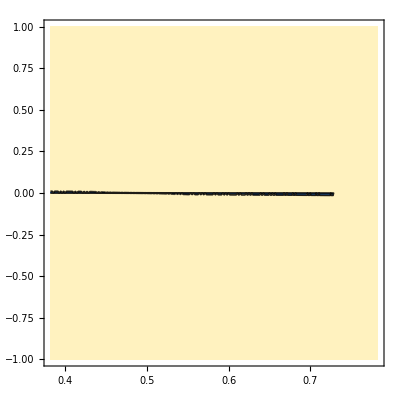

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

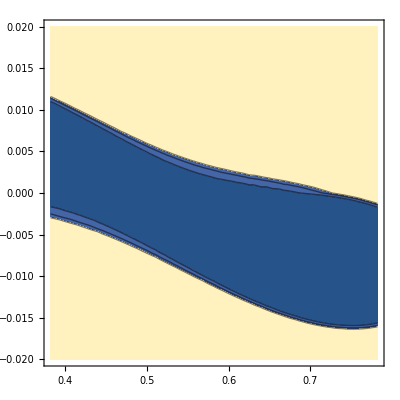

```mathematica
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]]/50,Max@ls23d[[All,2]]/50},Contours->{2.3,4.6,6.}]
```

## All data sets - s23 and dm31

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
pmut[s12_,c12_,s13_,c13_,s23_,c23_,δ_,dm31_,dm21_,ee_,emut_]=(dm31 (c23^4 ee emut^2 (-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2+dm31^2 (729.-1458. s13^2))+c23^3 ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+148.8066566943162 s13^2)) s23+c23^2 (c12^2 dm21 (-4.5474735088646407*^-13 dm31^2-2.7105054312137608*^-20 ee^2)+ee (1.9999999999999998 dm31^2-0.0008665646560000002 dm31 ee+9.386678787854984*^-8 ee^2+dm31 ((-3.5113576553450443+7.271321001515295*^-17 ⅈ) dm31+2.7105054312137608*^-20 ee+1101.7797307465376 dm31 emut^2) s13^2)) s23^2+c23 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.00000000000001-40.8066566943162 s13^2))) s23^3+ee (729. dm31^2-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2) emut^2 s23^4)+c23 dm31 (1101.7797307465376 c23^3 dm31^2 ee emut^2 s13^2+c23^2 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.-135.6133133886324 s13^2))) s23+c23 (c12^2 dm21 (4.5474735088646407*^-13 dm31^2+2.7105054312137608*^-20 ee^2)+ee (ee^2 (-9.386678787854984*^-8+0.00006842888836346283 emut^2)+dm31 ee (0.0008665646560000002-0.6317256342240002 emut^2-2.7105054312137608*^-20 s13^2)+dm31^2 (-1.9999999999999998+3.5113576553450443 s13^2+emut^2 (1458.-1458. s13^2)))) s23^2+ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+54. s13^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee]+c12 c23 dm21 s12 s13 (-8.673617379884035*^-19 c23^3 dm31 ee^2 emut+c23^2 ((-0.0004332823280000001 dm31+9.386678787854984*^-8 ee) ee^2+(-1.6442870905801747*^6 dm31^3+356.22026925346245 dm31^2 ee+0.31586281711200004 dm31 ee^2-0.00006842888836346282 ee^3) emut^2) s23+c23 (121799.04374667956 dm31^3-26.386686611367594 dm31^2 ee-0.046794491423999995 dm31 ee^2+0.000010137613090883384 ee^3) emut s23^2+(-2255.5378471607337 dm31^3+0.4886423446549555 dm31^2 ee+dm31 ee^2 (0.0004332823280000001-0.3158628171119999 emut^2)+ee^3 (-9.386678787854982*^-8+0.00006842888836346282 emut^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee-1. δ]-0.011698622856 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[δ]+2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[δ]-9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[δ]+2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[δ]+0.0008665646560000002 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[δ]-1.8773357575709967*^-7 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[δ]+1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[δ]-0.9475884513359999 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[δ]+0.00013685777672692564 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[δ]-747780.3248878407 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[δ]+54.00000000000003 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[δ]+0.093588982848 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[δ]-0.000015206419636325076 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[δ]+9231.855862812848 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[δ]-5.551115123125783*^-16 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[δ]-0.0012998469840000003 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[δ]+1.8773357575709967*^-7 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[δ]-1.3460045847981133*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[δ]+2916.000000000001 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[δ]+0.6317256342240001 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[δ]-0.00013685777672692564 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[δ]+249260.10829594688 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[δ]-54.00000000000001 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[δ]+2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[δ]+6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[1. δ]-1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[1. δ]-1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[1. δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[1. δ]+565081.7592678213 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[1. δ]-14.419970082948637 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[1. δ]-0.023397245712 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[1. δ]-6976.318015652115 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[1. δ]-0.48864234465495493 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[1. δ]+0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[1. δ]+1.0171471666820783*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[1. δ]-2203.559461493075 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[1. δ]-188360.5864226071 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[1. δ]+40.80665669431621 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[1. δ]-249260.10829594688 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+54.000000000000014 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+0.011698622856000002 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.0004332823280000001 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+9.386678787854984*^-8 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-6.730022923990566*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+1458.0000000000005 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.00006842888836346282 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+249260.10829594696 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-(0.035095868568+1.925929944387236*^-34 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]+5.068806545441692*^-6 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-1.9999999999999996 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.0008665646560000002 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-9.386678787854982*^-8 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-0.631725634224 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.00006842888836346282 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+0.023397245712 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+188360.5864226071 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-40.80665669431621 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+5.085735833410392*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1101.7797307465376 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-188360.5864226071 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]-13.19334330568379 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.011698622856 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.9999999999999998 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.31586281711200004 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]+954.9059770030174 c23^4 dm31^3 ee emut^2 s13^2 Sin[(3296.2634783428016 dm31)/ee]+177998.22783051126 c12^2 c23^3 dm21 dm31^3 emut s23 Sin[(3296.2634783428016 dm31)/ee]-77.12348653427833 c12^2 c23^3 dm21 dm31^2 ee emut s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c12^2 c23^3 dm21 dm31 ee^2 emut s23 Sin[(3296.2634783428016 dm31)/ee]-109.29551934143674 c23^3 dm31^3 ee emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c23^3 dm31^2 ee^2 emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]-6592.526956685602 c12^2 c23^2 dm21 dm31^3 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.856425427195494 c12^2 c23^2 dm21 dm31^2 ee s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c12^2 c23^2 dm21 dm31 ee^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+4.805952151423804*^6 c12^2 c23^2 dm21 dm31^3 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-2082.334136425515 c12^2 c23^2 dm21 dm31^2 ee emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c12^2 c23^2 dm21 dm31 ee^2 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.7380974557143687 c23^2 dm31^3 ee s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c23^2 dm31^2 ee^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-1041.1670682127576 c23^2 dm31^3 ee emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c23^2 dm31^2 ee^2 emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-177998.22783051128 c12^2 c23 dm21 dm31^3 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+77.12348653427834 c12^2 c23 dm21 dm31^2 ee emut s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c12^2 c23 dm21 dm31 ee^2 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+38.561743267139164 c23 dm31^3 ee emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c23 dm31^2 ee^2 emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]+4.407777171115168*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-954.9059770030176 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-326502.0126751977 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+70.7337760742976 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[δ]+4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[δ]-4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[δ]-5.534686227014404*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[δ]+2.3980817331903384*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[δ]-(2.5976160902274616*^-18+1.3877787807814457*^-17 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[δ]-7.471826406469446*^-10 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Sin[δ]+3.237410339806957*^-13 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Sin[δ]-3.5067817218070734*^-17 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Sin[δ]+6046.333568059216 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[1. δ]-1.3098847421166222 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[1. δ]+1.6187051699034782*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[1. δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[1. δ]+163251.00633759884 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[1. δ]-35.3668880371488 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[1. δ]+2.5976160902274616*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[1. δ]-4.8104001670878927*^-20 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Sin[1. δ]+163251.00633759884 c12 dm21 dm31^3 emut s12 s13 s23^4 Sin[1. δ]-35.3668880371488 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Sin[1. δ]-2.767343113507202*^-11 c12 c23^4 dm21 dm31^3 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.1990408665951692*^-14 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]-1.2988080451137308*^-18 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-7.471826406469446*^-10 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+3.237410339806957*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+2.767343113507202*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]-1.1990408665951692*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+1.2988080451137308*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+c12 dm21 dm31 s12 s13 (c23^4 dm31 (163251.00633759884 dm31-35.3668880371488 ee) emut+c23^3 dm31 (-6046.333568059216 dm31+1.3098847421166222 ee+4.407777171115168*^6 dm31 emut^2-954.9059770030176 ee emut^2) s23+c23^2 (-163251.00633759887 dm31^2+35.3668880371488 dm31 ee-1.2988080451137308*^-18 ee^2) emut s23^2+c23 ee (-1.1102230246251565*^-16 dm31+4.8104001670878927*^-20 ee+(1.6187051699034782*^-13 dm31-3.5067817218070734*^-17 ee) emut^2) s23^3+(-5.995204332975845*^-15 dm31+1.2988080451137308*^-18 ee) ee emut s23^4) Sin[(3296.2634783428016 dm31)/ee+1. δ])/(dm31 (dm31-0.00021664116400000005 ee)^2 ee);
```

```mathematica
ratioGen[S23_,δ_,dm31_,epS_,ee_]=(pmut[s12,c12,s13,c13,s23,c23,δ,dm31,dm21,ee,epS]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.s23->Sqrt[S23]/.Thread[{s12,s13,δ,dm21}->{Sqrt@0.31,Sqrt@0.02240,-2.5,7.39*10^-5}])/(pmut[s12,c12,s13,c13,s23,c23,δ,dm31,dm21,ee,0]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.Thread[{s12,s13,s23,δ,dm21,dm31}->{Sqrt@0.31,Sqrt@0.02240,Sqrt@0.582,-2.5,7.39*10^-5,2.525*10^-3}]);
```

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

116

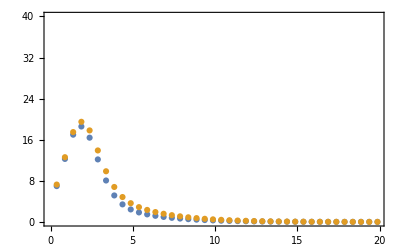

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{249.37,67.7919,11.3871,0.0143638,6.38304,16.0289,22.5031,25.7306,29.5343,37.3753,47.0408,246.261,65.21,10.0459,0.128467,7.80133,18.3309,25.1528,28.2486,31.6335,39.0249,48.4422,244.628,63.7778,9.31767,0.247915,8.6877,19.7404,26.7706,29.7903,32.9275,40.0517,49.3227,244.395,63.4138,9.11996,0.289704,8.95857,20.1733,27.2716,30.2705,33.3306,40.3702,49.5972,245.544,64.0963,9.43012,0.230691,8.5903,19.6055,26.6309,29.6637,32.8172,39.9545,49.2404,248.116,65.8602,10.2821,0.104331,7.61586,18.0692,24.8804,28.0013,31.4183,38.8358,48.2835,252.212,68.8012,11.7708,0.00502416,6.12913,15.6579,22.1129,25.3756,29.2257,37.1056,46.8184,258.008,73.09,14.0653,0.101321,4.29812,12.5389,18.4949,21.9524,26.4049,34.9294,45.0109,265.786,78.9978,17.4355,0.662201,2.39109,8.97966,14.2932,17.9977,23.2212,32.5721,43.1263,275.981,86.9468,22.3009,2.106,0.82542,5.39654,9.92295,13.9257,20.088,30.447,41.578,289.281,97.604,29.3244,5.0938,0.260757,2.44775,6.04097,10.3918,17.6595,29.2074,41.0201}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

19.775

19.4308

19.0148

1.03998

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

83

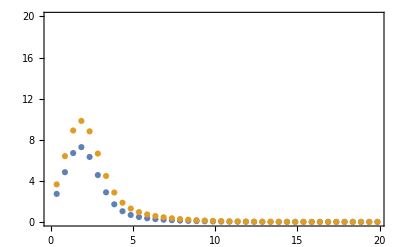

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{89.766,24.0636,3.96198,0.00405878,1.99643,4.58368,5.58749,5.42888,6.14881,9.52716,14.0878,88.6363,23.1308,3.48301,0.0433331,2.47517,5.31965,6.35843,6.04226,6.49647,9.61,14.0052,88.0431,22.6135,3.22326,0.0855027,2.77591,5.77301,6.83359,6.42488,6.7216,9.6776,13.9754,87.9586,22.4821,3.15274,0.100353,2.86821,5.91307,6.98199,6.54558,6.79288,9.69867,13.9673,88.3766,22.7286,3.26322,0.0794496,2.74341,5.73095,6.79453,6.39503,6.70086,9.66373,13.9715,89.3114,23.3657,3.56704,0.0349491,2.41348,5.23837,6.28271,5.98453,6.45668,9.58389,13.9993,90.8,24.4283,4.09873,0.00118083,1.91255,4.46924,5.48015,5.34748,6.0936,9.49236,14.0841,92.9068,25.9785,4.91982,0.0394512,1.30169,3.48435,4.4474,4.54415,5.67169,9.44914,14.286,95.734,28.1149,6.12847,0.247602,0.678469,2.38096,3.28135,3.67112,5.28727,9.55046,14.7015,99.44,30.9912,7.8773,0.777811,0.194674,1.31046,2.13296,2.87894,5.09054,9.94636,15.4807,104.275,34.85,10.4075,1.87057,0.090234,0.512172,1.24096,2.40572,5.31915,10.8742,16.8614}

```mathematica
dataSet2=chis23d;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

24

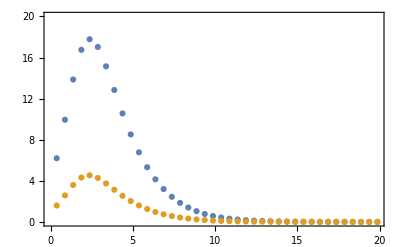

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{369.707,107.314,19.6161,0.0441872,15.4245,47.0651,82.5779,114.063,137.37,151.327,156.751,365.308,103.556,17.5547,0.248358,18.1362,52.2232,89.8721,123.017,147.437,161.974,167.521,362.996,101.469,16.4292,0.441379,19.8008,55.3298,94.2418,128.371,153.454,168.338,173.962,362.664,100.938,16.1237,0.506953,20.3016,56.2678,95.5695,130.008,155.302,170.3,175.955,364.285,101.934,16.6065,0.412873,19.6061,55.0044,93.8218,127.892,152.946,167.826,173.464,367.918,104.504,17.9252,0.206469,17.7614,51.5862,89.0453,122.07,146.433,160.961,166.534,373.702,108.784,20.2133,0.0207224,14.9001,46.1458,81.3717,112.675,135.893,149.834,155.296,381.888,115.013,23.7085,0.0928584,11.2591,38.9196,71.0373,99.9398,121.561,134.681,139.983,392.869,123.572,28.7901,0.801289,7.21645,30.2852,58.4191,84.2426,103.813,115.877,120.97,407.258,135.055,36.0478,2.73441,3.35977,20.8295,44.1033,66.1687,83.2345,94.006,98.8407,426.021,150.398,46.4131,6.82189,0.617566,11.4802,29.0166,46.6434,60.7488,69.991,74.5171}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,0.0005},{0.382,0.0012},{0.382,0.0019},{0.382,0.0026},{0.382,0.0033},{0.382,0.004},{0.382,0.0047},{0.382,0.0054},{0.382,0.0061},{0.382,0.0068},{0.382,0.0075},{0.422,0.0005},{0.422,0.0012},{0.422,0.0019},{0.422,0.0026},{0.422,0.0033},{0.422,0.004},{0.422,0.0047},{0.422,0.0054},{0.422,0.0061},{0.422,0.0068},{0.422,0.0075},{0.462,0.0005},{0.462,0.0012},{0.462,0.0019},{0.462,0.0026},{0.462,0.0033},{0.462,0.004},{0.462,0.0047},{0.462,0.0054},{0.462,0.0061},{0.462,0.0068},{0.462,0.0075},{0.502,0.0005},{0.502,0.0012},{0.502,0.0019},{0.502,0.0026},{0.502,0.0033},{0.502,0.004},{0.502,0.0047},{0.502,0.0054},{0.502,0.0061},{0.502,0.0068},{0.502,0.0075},{0.542,0.0005},{0.542,0.0012},{0.542,0.0019},{0.542,0.0026},{0.542,0.0033},{0.542,0.004},{0.542,0.0047},{0.542,0.0054},{0.542,0.0061},{0.542,0.0068},{0.542,0.0075},{0.582,0.0005},{0.582,0.0012},{0.582,0.0019},{0.582,0.0026},{0.582,0.0033},{0.582,0.004},{0.582,0.0047},{0.582,0.0054},{0.582,0.0061},{0.582,0.0068},{0.582,0.0075},{0.622,0.0005},{0.622,0.0012},{0.622,0.0019},{0.622,0.0026},{0.622,0.0033},{0.622,0.004},{0.622,0.0047},{0.622,0.0054},{0.622,0.0061},{0.622,0.0068},{0.622,0.0075},{0.662,0.0005},{0.662,0.0012},{0.662,0.0019},{0.662,0.0026},{0.662,0.0033},{0.662,0.004},{0.662,0.0047},{0.662,0.0054},{0.662,0.0061},{0.662,0.0068},{0.662,0.0075},{0.702,0.0005},{0.702,0.0012},{0.702,0.0019},{0.702,0.0026},{0.702,0.0033},{0.702,0.004},{0.702,0.0047},{0.702,0.0054},{0.702,0.0061},{0.702,0.0068},{0.702,0.0075},{0.742,0.0005},{0.742,0.0012},{0.742,0.0019},{0.742,0.0026},{0.742,0.0033},{0.742,0.004},{0.742,0.0047},{0.742,0.0054},{0.742,0.0061},{0.742,0.0068},{0.742,0.0075},{0.782,0.0005},{0.782,0.0012},{0.782,0.0019},{0.782,0.0026},{0.782,0.0033},{0.782,0.004},{0.782,0.0047},{0.782,0.0054},{0.782,0.0061},{0.782,0.0068},{0.782,0.0075}}

```mathematica
dataSet1
```

{249.37,67.7919,11.3871,0.0143638,6.38304,16.0289,22.5031,25.7306,29.5343,37.3753,47.0408,246.261,65.21,10.0459,0.128467,7.80133,18.3309,25.1528,28.2486,31.6335,39.0249,48.4422,244.628,63.7778,9.31767,0.247915,8.6877,19.7404,26.7706,29.7903,32.9275,40.0517,49.3227,244.395,63.4138,9.11996,0.289704,8.95857,20.1733,27.2716,30.2705,33.3306,40.3702,49.5972,245.544,64.0963,9.43012,0.230691,8.5903,19.6055,26.6309,29.6637,32.8172,39.9545,49.2404,248.116,65.8602,10.2821,0.104331,7.61586,18.0692,24.8804,28.0013,31.4183,38.8358,48.2835,252.212,68.8012,11.7708,0.00502416,6.12913,15.6579,22.1129,25.3756,29.2257,37.1056,46.8184,258.008,73.09,14.0653,0.101321,4.29812,12.5389,18.4949,21.9524,26.4049,34.9294,45.0109,265.786,78.9978,17.4355,0.662201,2.39109,8.97966,14.2932,17.9977,23.2212,32.5721,43.1263,275.981,86.9468,22.3009,2.106,0.82542,5.39654,9.92295,13.9257,20.088,30.447,41.578,289.281,97.604,29.3244,5.0938,0.260757,2.44775,6.04097,10.3918,17.6595,29.2074,41.0201}

```mathematica
dataSet2
```

{89.766,24.0636,3.96198,0.00405878,1.99643,4.58368,5.58749,5.42888,6.14881,9.52716,14.0878,88.6363,23.1308,3.48301,0.0433331,2.47517,5.31965,6.35843,6.04226,6.49647,9.61,14.0052,88.0431,22.6135,3.22326,0.0855027,2.77591,5.77301,6.83359,6.42488,6.7216,9.6776,13.9754,87.9586,22.4821,3.15274,0.100353,2.86821,5.91307,6.98199,6.54558,6.79288,9.69867,13.9673,88.3766,22.7286,3.26322,0.0794496,2.74341,5.73095,6.79453,6.39503,6.70086,9.66373,13.9715,89.3114,23.3657,3.56704,0.0349491,2.41348,5.23837,6.28271,5.98453,6.45668,9.58389,13.9993,90.8,24.4283,4.09873,0.00118083,1.91255,4.46924,5.48015,5.34748,6.0936,9.49236,14.0841,92.9068,25.9785,4.91982,0.0394512,1.30169,3.48435,4.4474,4.54415,5.67169,9.44914,14.286,95.734,28.1149,6.12847,0.247602,0.678469,2.38096,3.28135,3.67112,5.28727,9.55046,14.7015,99.44,30.9912,7.8773,0.777811,0.194674,1.31046,2.13296,2.87894,5.09054,9.94636,15.4807,104.275,34.85,10.4075,1.87057,0.090234,0.512172,1.24096,2.40572,5.31915,10.8742,16.8614}

```mathematica
dataSet3
```

{369.707,107.314,19.6161,0.0441872,15.4245,47.0651,82.5779,114.063,137.37,151.327,156.751,365.308,103.556,17.5547,0.248358,18.1362,52.2232,89.8721,123.017,147.437,161.974,167.521,362.996,101.469,16.4292,0.441379,19.8008,55.3298,94.2418,128.371,153.454,168.338,173.962,362.664,100.938,16.1237,0.506953,20.3016,56.2678,95.5695,130.008,155.302,170.3,175.955,364.285,101.934,16.6065,0.412873,19.6061,55.0044,93.8218,127.892,152.946,167.826,173.464,367.918,104.504,17.9252,0.206469,17.7614,51.5862,89.0453,122.07,146.433,160.961,166.534,373.702,108.784,20.2133,0.0207224,14.9001,46.1458,81.3717,112.675,135.893,149.834,155.296,381.888,115.013,23.7085,0.0928584,11.2591,38.9196,71.0373,99.9398,121.561,134.681,139.983,392.869,123.572,28.7901,0.801289,7.21645,30.2852,58.4191,84.2426,103.813,115.877,120.97,407.258,135.055,36.0478,2.73441,3.35977,20.8295,44.1033,66.1687,83.2345,94.006,98.8407,426.021,150.398,46.4131,6.82189,0.617566,11.4802,29.0166,46.6434,60.7488,69.991,74.5171}

### Contour

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

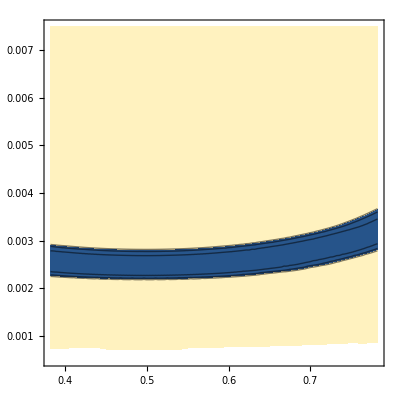

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

```mathematica
f[S23_]=2*Sqrt[S23]*Sqrt[1-S23];
```

```mathematica
(* sin^2(2θ) = 2 sin(θ)cos(θ) *)
```

```mathematica
Ls23d=MapAt[f,ls23d,{{All,1}}];
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000714286,0.0005005} lies outside the range of data in the interpolating function. Extrapolation will be used.

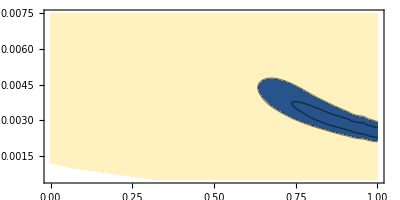

```mathematica
Table[{Ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,0,1},{del,Min@Ls23d[[All,2]],Max@Ls23d[[All,2]]},Contours->{2.3,11.3},AspectRatio->1/2]
```

```mathematica
(* compare with fig5 *)
```

```mathematica
(* In this plot, all the other parameters are fixed. In the paper, some of the parameters are marginalized over, so the region increases *)
```

## All data sets - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
sinal=Table[{bg[[i,1]],bg[[i,2]]+dataT[[i,2]]},{i,Length@bg}];
```

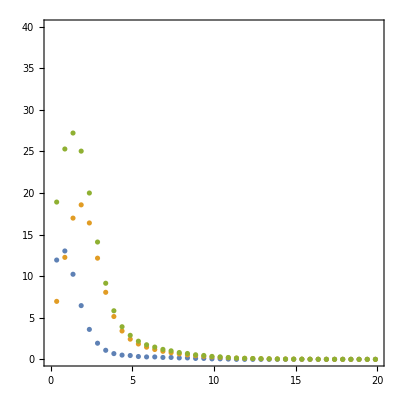

```mathematica
ListPlot[{bg,dataT,sinal},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

7

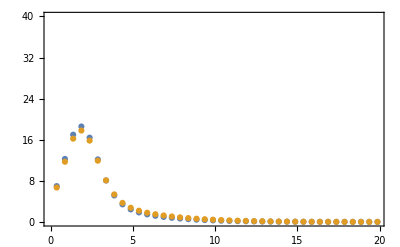

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{28.3962,20.0561,13.473,8.48504,4.90884,2.53512,1.12547,0.41493,0.129763,0.033219,0,0.0851642,0.530114,1.69353,3.96106,7.68465,13.1592,20.622,30.2605,42.2222,56.6229}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{24.3396,17.191,11.5483,7.27289,4.20758,2.17296,0.964689,0.355655,0.111226,0.0284734,0,0.0729979,0.454383,1.4516,3.3952,6.58685,11.2793,17.676,25.9376,36.1904,48.534}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{26.7438,18.8169,12.5569,7.8262,4.46343,2.23905,0.940361,0.305468,0.0803148,0.0203945,0,0.0693769,0.349385,1.1892,2.90543,5.81323,10.1929,16.2781,24.2095,34.1355,46.1896}

{-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.4,-0.45,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{23.0661,16.2202,10.8145,6.73103,3.83151,1.9249,0.806023,0.26183,0.0688413,0.017481,0,0.059466,0.305187,1.04217,2.5418,5.07419,8.87964,14.1583,21.0703,29.7219,40.1625}

{-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35,-0.45,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

16

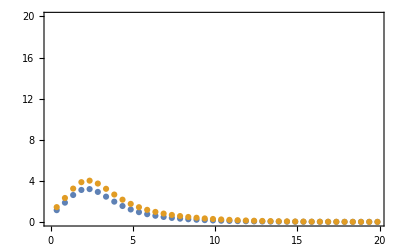

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

```mathematica
$10^{-7}<|U_{\mu N|<10^{-6}$
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{16.3418,11.4956,7.66016,4.75525,2.68211,1.32124,0.532046,0.156096,0.0287278,0.00489495,0,0.0279364,0.204785,0.710923,1.74161,3.47406,6.05469,9.59844,14.1928,19.9032,26.7776}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{14.0072,9.85339,6.56585,4.07593,2.29895,1.13249,0.456039,0.133797,0.0246238,0.00419567,0,0.0239455,0.17553,0.609362,1.49281,2.97776,5.18974,8.22723,12.1653,17.0599,22.9523}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{13.5199,9.48621,6.2993,3.89433,2.19369,1.10889,0.437802,0.152519,0.0223227,0.00154476,0,0.0185817,0.147654,0.430076,1.12841,2.30451,4.11401,6.68495,10.0987,14.4203,19.6991}

{-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{11.7314,8.24829,5.49083,3.38943,1.90317,0.956192,0.380974,0.13073,0.0191338,0.00132408,0,0.0159271,0.13173,0.374351,0.990063,1.99815,3.57772,5.82138,8.7989,12.566,17.1649}

{-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

3

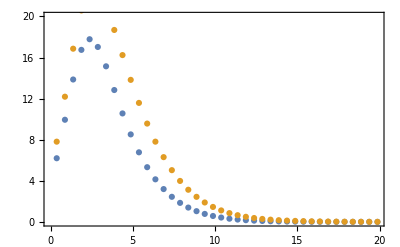

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{71.5077,48.7148,31.1906,18.4048,9.71496,4.37153,1.54253,0.369311,0.0608871,0.0240377,0,0.149249,1.02924,3.46918,8.40769,16.7598,29.3379,46.8204,69.7501,98.5474,133.53}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{61.2923,41.7555,26.7348,15.7755,8.32711,3.74702,1.32217,0.316552,0.052189,0.0206037,0,0.127928,0.882208,2.97358,7.20659,14.3655,25.1467,40.1318,59.7858,84.4692,114.454}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{62.1666,41.8594,26.7319,15.8053,8.38644,3.81451,1.38085,0.348416,0.0515139,0.0186567,0,0.110054,0.759913,2.63468,6.51664,13.2374,23.5567,38.2631,58.3354,84.2725,116.45}

{-0.5,-0.5,-0.45,-0.35,-0.25,-0.15,-0.1,-0.05,0.,0.,0.,-0.05,-0.1,-0.15,-0.25,-0.35,-0.45,-0.5,-0.5,-0.5,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{53.8571,36.4509,23.3296,13.7823,7.3075,3.32101,1.20203,0.304356,0.0441548,0.0159914,0,0.100047,0.674211,2.30973,5.72855,11.6067,20.6301,33.3684,50.5732,72.805,100.385}

{-0.5,-0.5,-0.4,-0.3,-0.2,-0.15,-0.05,-0.05,0.,0.,0.,-0.05,-0.1,-0.15,-0.25,-0.3,-0.4,-0.5,-0.5,-0.5,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.02},{-0.018},{-0.016},{-0.014},{-0.012},{-0.01},{-0.008},{-0.006},{-0.004},{-0.002},{0.},{0.002},{0.004},{0.006},{0.008},{0.01},{0.012},{0.014},{0.016},{0.018},{0.02}}

```mathematica
dataSet1
dataSet1bg
```

{24.3396,17.191,11.5483,7.27289,4.20758,2.17296,0.964689,0.355655,0.111226,0.0284734,0,0.0729979,0.454383,1.4516,3.3952,6.58685,11.2793,17.676,25.9376,36.1904,48.534}

{23.0661,16.2202,10.8145,6.73103,3.83151,1.9249,0.806023,0.26183,0.0688413,0.017481,0,0.059466,0.305187,1.04217,2.5418,5.07419,8.87964,14.1583,21.0703,29.7219,40.1625}

```mathematica
dataSet2
dataSet2bg
```

{14.0072,9.85339,6.56585,4.07593,2.29895,1.13249,0.456039,0.133797,0.0246238,0.00419567,0,0.0239455,0.17553,0.609362,1.49281,2.97776,5.18974,8.22723,12.1653,17.0599,22.9523}

{11.7314,8.24829,5.49083,3.38943,1.90317,0.956192,0.380974,0.13073,0.0191338,0.00132408,0,0.0159271,0.13173,0.374351,0.990063,1.99815,3.57772,5.82138,8.7989,12.566,17.1649}

```mathematica
dataSet3
dataSet3bg
```

{61.2923,41.7555,26.7348,15.7755,8.32711,3.74702,1.32217,0.316552,0.052189,0.0206037,0,0.127928,0.882208,2.97358,7.20659,14.3655,25.1467,40.1318,59.7858,84.4692,114.454}

{53.8571,36.4509,23.3296,13.7823,7.3075,3.32101,1.20203,0.304356,0.0441548,0.0159914,0,0.100047,0.674211,2.30973,5.72855,11.6067,20.6301,33.3684,50.5732,72.805,100.385}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3
```

{99.6392,68.7999,44.8489,27.1243,14.8336,7.05247,2.7429,0.806004,0.188038,0.0532728,0,0.224871,1.51212,5.03454,12.0946,23.9301,41.6158,66.035,97.8887,137.72,185.94}

InterpolatingFunction[…]

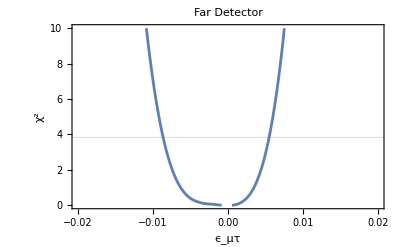

far_detector.pdf

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg
```

{88.6546,60.9194,39.6349,23.9027,13.0422,6.2021,2.38902,0.696917,0.13213,0.0347965,0,0.17544,1.11113,3.72625,9.26041,18.679,33.0874,53.3481,80.4424,115.093,157.713}

InterpolatingFunction[…]

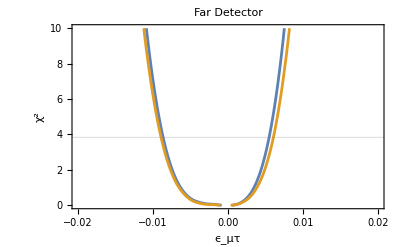

far_detector_bg.pdf

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_bg.pdf",%]
```

## All data sets - NSI - s23

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
sinal=Table[{bg[[i,1]],bg[[i,2]]+dataT[[i,2]]},{i,Length@bg}];
```

```mathematica
ListPlot[{bg,dataT,sinal},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-2;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

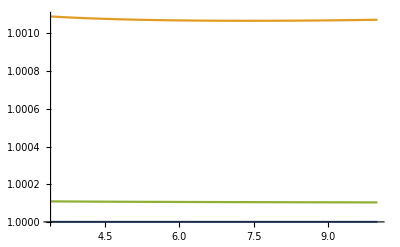

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,5.97521},{0.875,10.5096},{1.375,14.5549},{1.875,15.9213},{2.375,14.0555},{2.875,10.4278},{3.375,6.90915},{3.875,4.41438},{4.375,2.92321},{4.875,2.08077},{5.375,1.58208},{5.875,1.25399},{6.375,1.01521},{6.875,0.829789},{7.375,0.680839},{7.875,0.559192},{8.375,0.459032},{8.875,0.376232},{9.375,0.30767},{9.875,0.25089},{10.375,0.203914},{10.875,0.165121},{11.375,0.133169},{11.875,0.106934},{12.375,0.0854736},{12.875,0.0679899},{13.375,0.0538103},{13.875,0.0423658},{14.375,0.033176},{14.875,0.0258362},{15.375,0.0200064},{15.875,0.0154025},{16.375,0.0117882},{16.875,0.00896776},{17.375,0.00678044},{17.875,0.0050947},{18.375,0.0038038},{18.875,0.00282166},{19.375,0.00207936},{19.875,0.00152208}}

55

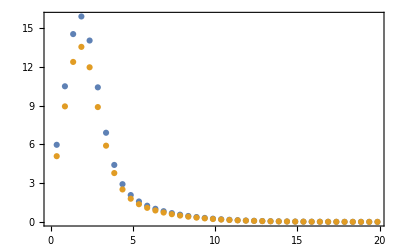

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{4.19938,3.6876,3.1865,2.73558,2.38034,2.17296,2.17336,2.45046,3.08376,4.16544,5.80309,2.08659,1.78334,1.48265,1.21824,1.02999,0.964689,1.07698,1.43064,2.10026,3.17338,4.7533,0.881103,0.723319,0.56148,0.42279,0.340715,0.355654,0.515863,0.878675,1.51213,2.49707,3.93001,0.313037,0.244963,0.167554,0.100801,0.0709793,0.111225,0.262365,0.574046,1.10624,1.93128,3.13648,0.113778,0.0932068,0.0590252,0.0234408,0.00488443,0.0284729,0.126709,0.34047,0.720352,1.32849,2.24098,0.072617,0.0781587,0.0665119,0.0417548,0.0140558,0,0.0231391,0.114806,0.315254,0.675219,1.25803,0.104231,0.140472,0.156577,0.148471,0.117977,0.0729988,0.0279144,0.00420515,0.0313713,0.148211,0.404574,0.281975,0.379024,0.453885,0.494627,0.49498,0.454386,0.378241,0.278349,0.17362,0.0910758,0.0672549,0.808079,1.01572,1.20048,1.34307,1.42963,1.4516,1.40589,1.29512,1.12815,0.920874,0.697247,1.94708,2.32725,2.68561,2.99615,3.238,3.3952,3.45677,3.41681,3.27488,3.03652,2.71408,3.96799,4.58859,5.19048,5.74157,6.2146,6.58685,6.84008,6.96054,6.93923,6.77221,6.46121}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{3.59946,3.1608,2.73128,2.34479,2.04029,1.86253,1.86288,2.1004,2.64322,3.57038,4.97408,1.78851,1.52858,1.27084,1.0442,0.882849,0.826877,0.923124,1.22626,1.80023,2.72004,4.07426,0.755231,0.619988,0.481268,0.362391,0.292041,0.304846,0.442168,0.75315,1.29611,2.14035,3.36858,0.268317,0.209968,0.143618,0.0864011,0.0608394,0.0953355,0.224884,0.492039,0.948209,1.65538,2.68841,0.0975238,0.0798915,0.050593,0.0200921,0.00418666,0.0244053,0.108608,0.291831,0.617445,1.1387,1.92084,0.0622431,0.0669931,0.0570102,0.0357898,0.0120478,0,0.0198335,0.0984049,0.270218,0.578759,1.07831,0.0893413,0.120405,0.134209,0.127261,0.101123,0.0625704,0.0239267,0.00360441,0.0268897,0.127038,0.346778,0.241693,0.324877,0.389044,0.423966,0.424269,0.389473,0.324207,0.238585,0.148817,0.078065,0.0576471,0.692639,0.870618,1.02898,1.1512,1.2254,1.24423,1.20505,1.1101,0.966988,0.789321,0.59764,1.66892,1.99478,2.30195,2.56813,2.77543,2.91017,2.96295,2.9287,2.80704,2.60273,2.32636,3.40114,3.93308,4.44898,4.92135,5.3268,5.64587,5.86292,5.96618,5.94791,5.80475,5.53818}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.43082,3.09641,2.7443,2.43014,2.12868,1.88952,1.73289,1.68081,1.75605,2.02625,2.44923,1.65116,1.46916,1.27161,1.06658,0.912752,0.795304,0.746283,0.804661,0.976631,1.30322,1.84457,0.670721,0.567877,0.465006,0.381396,0.298846,0.254403,0.301402,0.387914,0.627136,0.967843,1.51749,0.216902,0.183572,0.15009,0.0955452,0.0576864,0.0651362,0.127532,0.231547,0.467023,0.785177,1.301,0.0866661,0.0734133,0.0477453,0.0203391,0.00410117,0.0164407,0.0776067,0.150679,0.323573,0.595105,0.988929,0.0510556,0.0549533,0.0467423,0.0293143,0.00985255,0,0.0161401,0.0778333,0.150273,0.319009,0.589129,0.0813634,0.094115,0.0997205,0.0968197,0.0868008,0.0580408,0.0237476,0.00368215,0.0182647,0.0833745,0.178249,0.198329,0.248156,0.288677,0.311272,0.311437,0.288858,0.247584,0.196328,0.148896,0.0868912,0.0499761,0.617956,0.754572,0.862955,0.937034,0.983046,0.994799,0.970224,0.911615,0.825986,0.691608,0.545926,1.55387,1.78672,2.01198,2.21053,2.34992,2.43674,2.47098,2.44862,2.3699,2.23621,2.02965,3.26939,3.64452,4.01883,4.36838,4.66456,4.87848,5.02577,5.09627,5.08367,4.98586,4.80543}

{-0.15,-0.1,-0.1,-0.1,-0.05,-0.05,0.,0.,0.05,0.1,0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.05,0.1,0.15,-0.05,0.,0.,0.,0.,0.,0.05,0.05,0.05,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.05,0.05,0.05,0.1,0.,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{2.98723,2.67693,2.37512,2.10583,1.8303,1.6253,1.48533,1.44069,1.5109,1.74566,2.1222,1.43814,1.28214,1.09566,0.919924,0.788073,0.681689,0.639671,0.695424,0.842826,1.1399,1.60474,0.580618,0.492466,0.404291,0.332625,0.256153,0.218059,0.258345,0.338212,0.54326,0.852436,1.34395,0.19163,0.163062,0.133768,0.0818959,0.0494455,0.055831,0.115027,0.204183,0.40602,0.695866,1.14163,0.0760555,0.0629257,0.0409245,0.0174336,0.00351529,0.014092,0.068221,0.134867,0.283062,0.532948,0.870511,0.0437619,0.0471028,0.0400648,0.0251265,0.00844504,0,0.0138344,0.0684058,0.13452,0.279151,0.527825,0.0697401,0.0863843,0.091189,0.0887026,0.0784523,0.0497493,0.0203551,0.00315613,0.0156554,0.0771782,0.158499,0.17571,0.21842,0.253151,0.272519,0.27266,0.253307,0.217929,0.173995,0.13334,0.0744782,0.0428367,0.535391,0.65249,0.758147,0.826029,0.865468,0.875542,0.854478,0.804241,0.716474,0.598521,0.473651,1.35474,1.55433,1.74741,1.9176,2.05161,2.13931,2.16942,2.15024,2.07197,1.93961,1.76256,2.83435,3.1753,3.49614,3.79576,4.05655,4.26378,4.39923,4.45966,4.44886,4.36502,4.19333}

{-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,0.,0.,0.05,0.05,0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.1,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.1,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,0.05,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.05,0.05,0.1,0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.05,0.1,0.,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.05,0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.2,-0.2,-0.2,-0.2,-0.15}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-2;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.979577},{0.875,1.60576},{1.375,2.24307},{1.875,2.66511},{2.375,2.73731},{2.875,2.50178},{3.375,2.10684},{3.875,1.69048},{4.375,1.32699},{4.875,1.03671},{5.375,0.813371},{5.875,0.643145},{6.375,0.512847},{6.875,0.412122},{7.375,0.333351},{7.875,0.271034},{8.375,0.221205},{8.875,0.180984},{9.375,0.148262},{9.875,0.121474},{10.375,0.0994442},{10.875,0.081275},{11.375,0.0662689},{11.875,0.0538743},{12.375,0.0436474},{12.875,0.0352256},{13.375,0.0283093},{13.875,0.0226483},{14.375,0.0180327},{14.875,0.0142853},{15.375,0.011257},{15.875,0.00882189},{16.375,0.00687398},{16.875,0.00532439},{17.375,0.00409878},{17.875,0.00313526},{18.375,0.00238252},{18.875,0.0017983},{19.375,0.00134793},{19.875,0.00100317}}

89

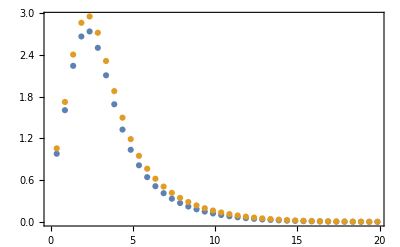

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{2.1738,1.97201,1.75814,1.54047,1.32839,1.13249,0.964799,0.838901,0.770232,0.776363,0.877386,1.0594,0.941582,0.814347,0.685046,0.562279,0.45604,0.377896,0.341217,0.361476,0.456628,0.647596,0.428012,0.369385,0.3038,0.237409,0.177731,0.133797,0.11634,0.138042,0.21387,0.361503,0.601897,0.135178,0.112345,0.0844725,0.056225,0.033713,0.0246238,0.0384074,0.0865294,0.182808,0.343864,0.589713,0.0363124,0.0305774,0.0208367,0.0100026,0.00246392,0.00419558,0.0229238,0.0683592,0.152514,0.29013,0.499251,0.0175296,0.0188374,0.0160143,0.0100465,0.00338024,0,0.00556081,0.0275834,0.0757278,0.162167,0.302095,0.0326801,0.0424328,0.0466954,0.0445033,0.0362929,0.0239457,0.0108816,0.00220702,0.00493267,0.0282754,0.084073,0.121765,0.152605,0.175537,0.187768,0.187819,0.175531,0.152124,0.120301,0.0844041,0.0506484,0.0274398,0.394436,0.467118,0.528751,0.574939,0.602482,0.609363,0.594777,0.559188,0.504448,0.433956,0.352899,0.993469,1.13284,1.25768,1.36224,1.44183,1.49281,1.51257,1.49957,1.45344,1.37504,1.26667,2.0633,2.29505,2.50878,2.69763,2.85564,2.97777,3.05983,3.09855,3.09156,3.03748,2.93607}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{1.86326,1.69029,1.50698,1.32041,1.13862,0.970708,0.82697,0.719058,0.660199,0.665454,0.752045,0.908061,0.80707,0.698012,0.587182,0.481953,0.390891,0.323911,0.292472,0.309837,0.391395,0.555082,0.366867,0.316615,0.2604,0.203493,0.15234,0.114683,0.0997197,0.118322,0.183317,0.30986,0.515912,0.115867,0.0962957,0.072405,0.0481929,0.0288968,0.0211061,0.0329207,0.0741681,0.156693,0.294741,0.505468,0.0311249,0.0262092,0.01786,0.00857365,0.00211193,0.00359621,0.019649,0.0585936,0.130726,0.248683,0.427929,0.0150254,0.0161463,0.0137266,0.00861133,0.00289735,0,0.00476641,0.0236429,0.0649096,0.139001,0.258939,0.0280115,0.036371,0.0400247,0.0381457,0.0311082,0.0205249,0.00932706,0.00189173,0.004228,0.0242361,0.0720626,0.10437,0.130805,0.15046,0.160944,0.160987,0.150455,0.130392,0.103115,0.0723463,0.0434129,0.0235198,0.338088,0.400387,0.453215,0.492805,0.516413,0.522312,0.509809,0.479304,0.432384,0.371962,0.302485,0.851545,0.971006,1.07801,1.16763,1.23585,1.27955,1.29649,1.28535,1.24581,1.17861,1.08571,1.76854,1.96719,2.15039,2.31225,2.44769,2.55237,2.62271,2.6559,2.64991,2.60356,2.51663}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.4962,1.39209,1.28212,1.17049,1.06184,0.933223,0.803367,0.688849,0.595895,0.531148,0.50166,0.719014,0.652974,0.581028,0.506816,0.434479,0.368672,0.314577,0.277922,0.24628,0.213473,0.214076,0.276114,0.250259,0.221865,0.193943,0.170097,0.133122,0.0964356,0.0740323,0.0719378,0.096898,0.156434,0.104566,0.0901281,0.0718502,0.0519613,0.0333249,0.0194592,0.0145672,0.0235785,0.052204,0.107004,0.188631,0.0222937,0.0191689,0.0137685,0.0074817,0.00237613,0.00121976,0.0075154,0.0255495,0.0604565,0.118302,0.179889,0.00828693,0.00890529,0.00756465,0.00473774,0.00158994,0,0.00259463,0.0127985,0.034902,0.0741496,0.136854,0.0201793,0.0254302,0.0277032,0.0265316,0.0221248,0.0153855,0.0079417,0.00219329,0.0013763,0.00964824,0.032199,0.0957452,0.114875,0.128799,0.136144,0.136171,0.128784,0.114564,0.0948051,0.0715718,0.0477784,0.0272877,0.258898,0.291057,0.318696,0.339594,0.352119,0.355248,0.348587,0.332407,0.307699,0.276242,0.240693,0.678762,0.756335,0.825495,0.883262,0.927165,0.950329,0.958737,0.953179,0.933524,0.890265,0.830385,1.43197,1.5514,1.662,1.76007,1.84239,1.90618,1.94911,1.96938,1.9657,1.93736,1.8843}

{-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.30531,1.21608,1.12182,1.02613,0.925093,0.805619,0.694314,0.596156,0.516482,0.460984,0.435709,0.622012,0.565406,0.503738,0.440128,0.378125,0.321719,0.275352,0.243933,0.211097,0.182977,0.183494,0.242383,0.220222,0.195884,0.171951,0.151512,0.114105,0.0826591,0.0634563,0.0616609,0.0830554,0.134086,0.089628,0.0772527,0.0615859,0.0445382,0.0285642,0.0166793,0.0124862,0.0202101,0.0447463,0.0917177,0.167398,0.0191089,0.0164304,0.0118016,0.00641289,0.00203669,0.00104551,0.00644178,0.0218995,0.0518199,0.101402,0.159905,0.00710308,0.00763311,0.00648398,0.00406092,0.00136281,0,0.00222397,0.0109702,0.029916,0.0635568,0.117303,0.0172965,0.0217973,0.0237456,0.0227414,0.0189641,0.0131876,0.00680717,0.00187996,0.00117969,0.00826992,0.0275991,0.0820673,0.0984644,0.110399,0.116695,0.116718,0.110387,0.0981981,0.0812615,0.0613473,0.0409529,0.0233895,0.227627,0.255191,0.278883,0.296795,0.307531,0.310213,0.304503,0.290634,0.269456,0.242493,0.212022,0.58751,0.654001,0.713281,0.762796,0.800427,0.824508,0.833832,0.827685,0.805878,0.768799,0.717472,1.25026,1.35263,1.44743,1.53149,1.60205,1.65672,1.69352,1.7109,1.70774,1.68345,1.63797}

{-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-2;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,5.31141},{0.875,8.52311},{1.375,11.8828},{1.875,14.3551},{2.375,15.243},{2.875,14.597},{3.375,12.9826},{3.875,11.0043},{4.375,9.05147},{4.875,7.30118},{5.375,5.80644},{5.875,4.56467},{6.375,3.55219},{6.875,2.73878},{7.375,2.09367},{7.875,1.58801},{8.375,1.19593},{8.875,0.894927},{9.375,0.665937},{9.875,0.493159},{10.375,0.363746},{10.875,0.267439},{11.375,0.196167},{11.875,0.143667},{12.375,0.105139},{12.875,0.0769445},{13.375,0.056349},{13.875,0.0413177},{14.375,0.0303467},{14.875,0.0223318},{15.375,0.0164668},{15.875,0.0121652},{16.375,0.00900182},{16.875,0.00666892},{17.375,0.00494369},{17.875,0.00366465},{18.375,0.00271451},{18.875,0.00200775},{19.375,0.00148172},{19.875,0.00109031}}

10

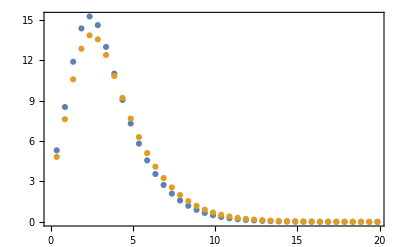

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{9.71253,8.55107,7.32212,6.07404,4.86166,3.74703,2.80025,2.10062,1.73802,1.81459,2.44687,4.71679,4.046,3.32419,2.59454,1.90761,1.32217,0.906213,0.738316,0.909374,1.5248,2.70733,1.93792,1.60714,1.23926,0.870506,0.545195,0.316553,0.247841,0.41384,0.902798,1.81897,3.28592,0.651524,0.522718,0.366596,0.210607,0.0907176,0.0521888,0.150667,0.453681,1.04263,2.01544,3.49007,0.198813,0.165826,0.11001,0.0484669,0.0069699,0.0206032,0.134736,0.406391,0.906109,1.72047,2.95544,0.102886,0.110532,0.0939505,0.0589324,0.0198265,0,0.0326126,0.161762,0.444087,0.950961,1.77146,0.178044,0.234057,0.258565,0.245915,0.198683,0.127929,0.0537452,0.0061282,0.0262569,0.168268,0.501691,0.578366,0.752421,0.882364,0.9518,0.952046,0.882212,0.749524,0.569938,0.369085,0.183621,0.06312,1.75622,2.16642,2.51559,2.77788,2.93448,2.97359,2.89052,2.68813,2.37745,1.97865,1.52247,4.35636,5.14946,5.8617,6.45928,6.91471,7.2066,7.31973,7.24519,6.98086,6.53204,5.91244,9.09909,10.4314,11.6618,12.7499,13.661,14.3655,14.8391,15.0625,15.022,14.7097,14.1243}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{8.32502,7.32949,6.2761,5.20632,4.16714,3.21174,2.40021,1.80053,1.48973,1.55536,2.09732,4.04297,3.468,2.84931,2.22389,1.6351,1.13329,0.776754,0.632842,0.779463,1.30697,2.32057,1.66108,1.37755,1.06222,0.746148,0.46731,0.271331,0.212435,0.35472,0.773827,1.55911,2.81651,0.558449,0.448044,0.314225,0.18052,0.0777579,0.0447333,0.129143,0.38887,0.893686,1.72752,2.99149,0.170411,0.142136,0.0942939,0.0415431,0.0059742,0.0176599,0.115488,0.348335,0.776665,1.47469,2.53323,0.0881883,0.0947413,0.080529,0.0505135,0.0169942,0,0.0279537,0.138653,0.380646,0.815109,1.51839,0.152609,0.200621,0.221627,0.210784,0.1703,0.109654,0.0460673,0.00525274,0.0225059,0.144229,0.430021,0.495742,0.644932,0.756312,0.815829,0.81604,0.756182,0.642449,0.488519,0.316359,0.15739,0.0541028,1.50533,1.85693,2.15622,2.38104,2.51527,2.54879,2.47759,2.30411,2.03781,1.69599,1.30497,3.73402,4.41382,5.02431,5.53653,5.9269,6.17709,6.27405,6.21016,5.9836,5.59889,5.0678,7.79922,8.94123,9.99581,10.9285,11.7094,12.3133,12.7192,12.9107,12.876,12.6083,12.1066}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{7.5996,6.74226,5.84699,4.93279,4.04833,3.21421,2.49738,1.9385,1.57721,1.46976,1.6778,3.62208,3.15025,2.62479,2.10147,1.59961,1.16979,0.829483,0.648861,0.671476,0.946612,1.52957,1.46363,1.22409,0.961372,0.709379,0.464639,0.297464,0.209213,0.274966,0.534971,1.02432,1.81789,0.481854,0.386761,0.274438,0.168086,0.0879084,0.0431671,0.099724,0.263517,0.600593,1.16335,2.00345,0.135079,0.114789,0.0824833,0.0431234,0.00670463,0.0153694,0.0857709,0.248038,0.548299,1.04346,1.76158,0.0738575,0.0778969,0.069246,0.0488516,0.0164187,0,0.0269213,0.104245,0.280694,0.587065,1.08981,0.121977,0.15719,0.173064,0.164835,0.13474,0.0922342,0.0476354,0.00595185,0.0197487,0.103708,0.310079,0.426849,0.544393,0.628391,0.674163,0.674319,0.628267,0.542507,0.420603,0.275305,0.149689,0.0610675,1.33024,1.61382,1.85374,2.03727,2.14801,2.17578,2.11682,1.97414,1.75809,1.48718,1.16024,3.36063,3.92587,4.4441,4.87137,5.1938,5.40221,5.48331,5.42982,5.24085,4.92254,4.48123,7.13806,8.10721,9.00836,9.81705,10.4815,10.9973,11.3462,11.5113,11.4813,11.2506,10.8201}

{-0.3,-0.25,-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.05,-0.2,-0.2,-0.15,-0.15,-0.1,-0.1,-0.05,0.,0.05,0.1,0.15,-0.15,-0.1,-0.1,-0.1,-0.05,-0.05,0.,0.05,0.1,0.1,0.15,-0.05,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.15,0.2,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.15,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.2,-0.2,-0.2,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.2,-0.25,-0.3,-0.3,-0.3,-0.35,-0.35,-0.35,-0.35,-0.35,-0.35,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{6.66208,5.92194,5.12264,4.31954,3.53214,2.80647,2.16347,1.66729,1.35646,1.25979,1.44383,3.19097,2.75811,2.30124,1.84402,1.39395,1.01669,0.716699,0.556166,0.581265,0.827901,1.3469,1.27978,1.07207,0.846891,0.619932,0.403976,0.260683,0.179326,0.241399,0.466012,0.900849,1.60962,0.418732,0.337224,0.240947,0.149788,0.0753501,0.0370003,0.091192,0.231586,0.537651,1.03952,1.77841,0.121496,0.104105,0.0764143,0.0369629,0.00574682,0.0131738,0.0792322,0.218318,0.492828,0.920758,1.56136,0.0690207,0.0724831,0.065068,0.0418728,0.0140732,0,0.0230754,0.0950674,0.246309,0.526056,0.964473,0.110266,0.140448,0.154055,0.147001,0.121206,0.0847721,0.0408303,0.00510159,0.0169275,0.0946068,0.271496,0.371585,0.482829,0.561478,0.600712,0.600845,0.561372,0.48094,0.366231,0.24169,0.134019,0.0523436,1.16306,1.42336,1.64035,1.79766,1.89258,1.91638,1.86584,1.74354,1.55836,1.30349,1.01735,2.95332,3.45646,3.90066,4.27875,4.56973,4.75738,4.83032,4.78223,4.61213,4.325,3.93248,6.2612,7.11816,7.92156,8.62033,9.207,9.66418,9.97307,10.1192,10.0927,9.88851,9.50725}

{-0.25,-0.25,-0.2,-0.2,-0.15,-0.15,-0.1,-0.05,0.,0.,0.05,-0.15,-0.15,-0.15,-0.1,-0.1,-0.05,-0.05,0.,0.05,0.05,0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,0.,0.05,0.05,0.1,0.15,-0.05,-0.05,-0.05,-0.05,0.,0.,0.05,0.05,0.1,0.1,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,0.1,0.1,0.15,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.05,0.05,0.1,0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.05,0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,0.,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.15,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.25,-0.25,-0.25,-0.3,-0.3,-0.3,-0.3,-0.3,-0.3,-0.3,-0.3}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.01,0.482},{-0.01,0.502},{-0.01,0.522},{-0.01,0.542},{-0.01,0.562},{-0.01,0.582},{-0.01,0.602},{-0.01,0.622},{-0.01,0.642},{-0.01,0.662},{-0.01,0.682},{-0.008,0.482},{-0.008,0.502},{-0.008,0.522},{-0.008,0.542},{-0.008,0.562},{-0.008,0.582},{-0.008,0.602},{-0.008,0.622},{-0.008,0.642},{-0.008,0.662},{-0.008,0.682},{-0.006,0.482},{-0.006,0.502},{-0.006,0.522},{-0.006,0.542},{-0.006,0.562},{-0.006,0.582},{-0.006,0.602},{-0.006,0.622},{-0.006,0.642},{-0.006,0.662},{-0.006,0.682},{-0.004,0.482},{-0.004,0.502},{-0.004,0.522},{-0.004,0.542},{-0.004,0.562},{-0.004,0.582},{-0.004,0.602},{-0.004,0.622},{-0.004,0.642},{-0.004,0.662},{-0.004,0.682},{-0.002,0.482},{-0.002,0.502},{-0.002,0.522},{-0.002,0.542},{-0.002,0.562},{-0.002,0.582},{-0.002,0.602},{-0.002,0.622},{-0.002,0.642},{-0.002,0.662},{-0.002,0.682},{0.,0.482},{0.,0.502},{0.,0.522},{0.,0.542},{0.,0.562},{0.,0.582},{0.,0.602},{0.,0.622},{0.,0.642},{0.,0.662},{0.,0.682},{0.002,0.482},{0.002,0.502},{0.002,0.522},{0.002,0.542},{0.002,0.562},{0.002,0.582},{0.002,0.602},{0.002,0.622},{0.002,0.642},{0.002,0.662},{0.002,0.682},{0.004,0.482},{0.004,0.502},{0.004,0.522},{0.004,0.542},{0.004,0.562},{0.004,0.582},{0.004,0.602},{0.004,0.622},{0.004,0.642},{0.004,0.662},{0.004,0.682},{0.006,0.482},{0.006,0.502},{0.006,0.522},{0.006,0.542},{0.006,0.562},{0.006,0.582},{0.006,0.602},{0.006,0.622},{0.006,0.642},{0.006,0.662},{0.006,0.682},{0.008,0.482},{0.008,0.502},{0.008,0.522},{0.008,0.542},{0.008,0.562},{0.008,0.582},{0.008,0.602},{0.008,0.622},{0.008,0.642},{0.008,0.662},{0.008,0.682},{0.01,0.482},{0.01,0.502},{0.01,0.522},{0.01,0.542},{0.01,0.562},{0.01,0.582},{0.01,0.602},{0.01,0.622},{0.01,0.642},{0.01,0.662},{0.01,0.682}}

```mathematica
dataSet1
dataSet1bg
```

{3.59946,3.1608,2.73128,2.34479,2.04029,1.86253,1.86288,2.1004,2.64322,3.57038,4.97408,1.78851,1.52858,1.27084,1.0442,0.882849,0.826877,0.923124,1.22626,1.80023,2.72004,4.07426,0.755231,0.619988,0.481268,0.362391,0.292041,0.304846,0.442168,0.75315,1.29611,2.14035,3.36858,0.268317,0.209968,0.143618,0.0864011,0.0608394,0.0953355,0.224884,0.492039,0.948209,1.65538,2.68841,0.0975238,0.0798915,0.050593,0.0200921,0.00418666,0.0244053,0.108608,0.291831,0.617445,1.1387,1.92084,0.0622431,0.0669931,0.0570102,0.0357898,0.0120478,0,0.0198335,0.0984049,0.270218,0.578759,1.07831,0.0893413,0.120405,0.134209,0.127261,0.101123,0.0625704,0.0239267,0.00360441,0.0268897,0.127038,0.346778,0.241693,0.324877,0.389044,0.423966,0.424269,0.389473,0.324207,0.238585,0.148817,0.078065,0.0576471,0.692639,0.870618,1.02898,1.1512,1.2254,1.24423,1.20505,1.1101,0.966988,0.789321,0.59764,1.66892,1.99478,2.30195,2.56813,2.77543,2.91017,2.96295,2.9287,2.80704,2.60273,2.32636,3.40114,3.93308,4.44898,4.92135,5.3268,5.64587,5.86292,5.96618,5.94791,5.80475,5.53818}

{2.98723,2.67693,2.37512,2.10583,1.8303,1.6253,1.48533,1.44069,1.5109,1.74566,2.1222,1.43814,1.28214,1.09566,0.919924,0.788073,0.681689,0.639671,0.695424,0.842826,1.1399,1.60474,0.580618,0.492466,0.404291,0.332625,0.256153,0.218059,0.258345,0.338212,0.54326,0.852436,1.34395,0.19163,0.163062,0.133768,0.0818959,0.0494455,0.055831,0.115027,0.204183,0.40602,0.695866,1.14163,0.0760555,0.0629257,0.0409245,0.0174336,0.00351529,0.014092,0.068221,0.134867,0.283062,0.532948,0.870511,0.0437619,0.0471028,0.0400648,0.0251265,0.00844504,0,0.0138344,0.0684058,0.13452,0.279151,0.527825,0.0697401,0.0863843,0.091189,0.0887026,0.0784523,0.0497493,0.0203551,0.00315613,0.0156554,0.0771782,0.158499,0.17571,0.21842,0.253151,0.272519,0.27266,0.253307,0.217929,0.173995,0.13334,0.0744782,0.0428367,0.535391,0.65249,0.758147,0.826029,0.865468,0.875542,0.854478,0.804241,0.716474,0.598521,0.473651,1.35474,1.55433,1.74741,1.9176,2.05161,2.13931,2.16942,2.15024,2.07197,1.93961,1.76256,2.83435,3.1753,3.49614,3.79576,4.05655,4.26378,4.39923,4.45966,4.44886,4.36502,4.19333}

```mathematica
dataSet2
dataSet2bg
```

{1.86326,1.69029,1.50698,1.32041,1.13862,0.970708,0.82697,0.719058,0.660199,0.665454,0.752045,0.908061,0.80707,0.698012,0.587182,0.481953,0.390891,0.323911,0.292472,0.309837,0.391395,0.555082,0.366867,0.316615,0.2604,0.203493,0.15234,0.114683,0.0997197,0.118322,0.183317,0.30986,0.515912,0.115867,0.0962957,0.072405,0.0481929,0.0288968,0.0211061,0.0329207,0.0741681,0.156693,0.294741,0.505468,0.0311249,0.0262092,0.01786,0.00857365,0.00211193,0.00359621,0.019649,0.0585936,0.130726,0.248683,0.427929,0.0150254,0.0161463,0.0137266,0.00861133,0.00289735,0,0.00476641,0.0236429,0.0649096,0.139001,0.258939,0.0280115,0.036371,0.0400247,0.0381457,0.0311082,0.0205249,0.00932706,0.00189173,0.004228,0.0242361,0.0720626,0.10437,0.130805,0.15046,0.160944,0.160987,0.150455,0.130392,0.103115,0.0723463,0.0434129,0.0235198,0.338088,0.400387,0.453215,0.492805,0.516413,0.522312,0.509809,0.479304,0.432384,0.371962,0.302485,0.851545,0.971006,1.07801,1.16763,1.23585,1.27955,1.29649,1.28535,1.24581,1.17861,1.08571,1.76854,1.96719,2.15039,2.31225,2.44769,2.55237,2.62271,2.6559,2.64991,2.60356,2.51663}

{1.30531,1.21608,1.12182,1.02613,0.925093,0.805619,0.694314,0.596156,0.516482,0.460984,0.435709,0.622012,0.565406,0.503738,0.440128,0.378125,0.321719,0.275352,0.243933,0.211097,0.182977,0.183494,0.242383,0.220222,0.195884,0.171951,0.151512,0.114105,0.0826591,0.0634563,0.0616609,0.0830554,0.134086,0.089628,0.0772527,0.0615859,0.0445382,0.0285642,0.0166793,0.0124862,0.0202101,0.0447463,0.0917177,0.167398,0.0191089,0.0164304,0.0118016,0.00641289,0.00203669,0.00104551,0.00644178,0.0218995,0.0518199,0.101402,0.159905,0.00710308,0.00763311,0.00648398,0.00406092,0.00136281,0,0.00222397,0.0109702,0.029916,0.0635568,0.117303,0.0172965,0.0217973,0.0237456,0.0227414,0.0189641,0.0131876,0.00680717,0.00187996,0.00117969,0.00826992,0.0275991,0.0820673,0.0984644,0.110399,0.116695,0.116718,0.110387,0.0981981,0.0812615,0.0613473,0.0409529,0.0233895,0.227627,0.255191,0.278883,0.296795,0.307531,0.310213,0.304503,0.290634,0.269456,0.242493,0.212022,0.58751,0.654001,0.713281,0.762796,0.800427,0.824508,0.833832,0.827685,0.805878,0.768799,0.717472,1.25026,1.35263,1.44743,1.53149,1.60205,1.65672,1.69352,1.7109,1.70774,1.68345,1.63797}

```mathematica
dataSet3
dataSet3bg
```

{8.32502,7.32949,6.2761,5.20632,4.16714,3.21174,2.40021,1.80053,1.48973,1.55536,2.09732,4.04297,3.468,2.84931,2.22389,1.6351,1.13329,0.776754,0.632842,0.779463,1.30697,2.32057,1.66108,1.37755,1.06222,0.746148,0.46731,0.271331,0.212435,0.35472,0.773827,1.55911,2.81651,0.558449,0.448044,0.314225,0.18052,0.0777579,0.0447333,0.129143,0.38887,0.893686,1.72752,2.99149,0.170411,0.142136,0.0942939,0.0415431,0.0059742,0.0176599,0.115488,0.348335,0.776665,1.47469,2.53323,0.0881883,0.0947413,0.080529,0.0505135,0.0169942,0,0.0279537,0.138653,0.380646,0.815109,1.51839,0.152609,0.200621,0.221627,0.210784,0.1703,0.109654,0.0460673,0.00525274,0.0225059,0.144229,0.430021,0.495742,0.644932,0.756312,0.815829,0.81604,0.756182,0.642449,0.488519,0.316359,0.15739,0.0541028,1.50533,1.85693,2.15622,2.38104,2.51527,2.54879,2.47759,2.30411,2.03781,1.69599,1.30497,3.73402,4.41382,5.02431,5.53653,5.9269,6.17709,6.27405,6.21016,5.9836,5.59889,5.0678,7.79922,8.94123,9.99581,10.9285,11.7094,12.3133,12.7192,12.9107,12.876,12.6083,12.1066}

{6.66208,5.92194,5.12264,4.31954,3.53214,2.80647,2.16347,1.66729,1.35646,1.25979,1.44383,3.19097,2.75811,2.30124,1.84402,1.39395,1.01669,0.716699,0.556166,0.581265,0.827901,1.3469,1.27978,1.07207,0.846891,0.619932,0.403976,0.260683,0.179326,0.241399,0.466012,0.900849,1.60962,0.418732,0.337224,0.240947,0.149788,0.0753501,0.0370003,0.091192,0.231586,0.537651,1.03952,1.77841,0.121496,0.104105,0.0764143,0.0369629,0.00574682,0.0131738,0.0792322,0.218318,0.492828,0.920758,1.56136,0.0690207,0.0724831,0.065068,0.0418728,0.0140732,0,0.0230754,0.0950674,0.246309,0.526056,0.964473,0.110266,0.140448,0.154055,0.147001,0.121206,0.0847721,0.0408303,0.00510159,0.0169275,0.0946068,0.271496,0.371585,0.482829,0.561478,0.600712,0.600845,0.561372,0.48094,0.366231,0.24169,0.134019,0.0523436,1.16306,1.42336,1.64035,1.79766,1.89258,1.91638,1.86584,1.74354,1.55836,1.30349,1.01735,2.95332,3.45646,3.90066,4.27875,4.56973,4.75738,4.83032,4.78223,4.61213,4.325,3.93248,6.2612,7.11816,7.92156,8.62033,9.207,9.66418,9.97307,10.1192,10.0927,9.88851,9.50725}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adriano/Dropbox/Neutrinos/Tau/Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

{{-0.01,6.04498},{-0.008,2.35106},{-0.006,0.690861},{-0.004,0.161175},{-0.002,0.0456614},{0.,0},{0.002,0.192749},{0.004,1.29611},{0.006,4.31533},{0.008,10.3668},{0.01,20.5115}}

InterpolatingFunction[…]

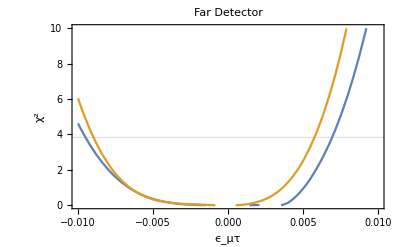

far_detector_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSet[[1+11*j;;11+11*j]]},{j,0,10}];
func=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSet[[1+5+11*j]]},{j,0,10}]
funcNo=Interpolation@%
Plot[{func[del],funcNo[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_s23.pdf",%]
```

```mathematica
-
```

-Graphics-

far_detector.pdf

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

InterpolatingFunction[…]

{{-0.01,5.23739},{-0.008,2.0201},{-0.006,0.592847},{-0.004,0.109511},{-0.002,0.0283113},{0.,0},{0.002,0.147709},{0.004,0.925065},{0.006,3.10214},{0.008,7.7212},{0.01,15.5847}}

InterpolatingFunction[…]

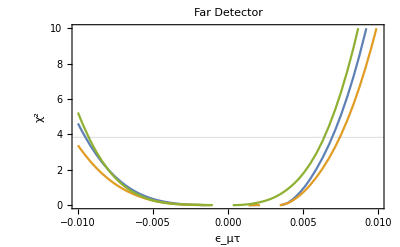

far_detector_bg_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSetbg[[1+11*j;;11+11*j]]},{j,0,10}];
funcbg=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSetbg[[1+5+11*j]]},{j,0,10}]
funcNobg=Interpolation@%
Plot[{func[del],funcbg[del],funcNobg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_bg_s23.pdf",%]
```

```mathematica
-
```

-Graphics-

far_detector_bg.pdf

## All data sets - near - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(94593.79431933298 ee epS^2-16993.30788307618 ee^2 epS^2+729.0000000000001 ee^3 epS^2+259.51658341292085 ee s23^2-46.62087210720489 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-184751.02944044588 ee epS^2 s23^2+33986.61576615236 ee^2 epS^2 s23^2-1458.0000000000002 ee^3 epS^2 s23^2-259.5165834129209 ee s23^4+46.62087210720489 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+189187.5893080193 ee epS^2 s23^4-33986.61576615236 ee^2 epS^2 s23^4+1458.0000000000002 ee^3 epS^2 s23^4-6842.630720016514 ee epS s23 √(1-s23^2)+1258.7635468945318 ee^2 epS s23 √(1-s23^2)-54.00000000000001 ee^3 epS s23 √(1-s23^2)+14013.895504297725 ee epS s23^3 √(1-s23^2)-2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)+108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+2.437058034171625 ee epS^2 Sin[0.006402357909858133/ee]-0.03512714837222423 s23^2 Sin[0.006402357909858133/ee]+0.012713742369988023 ee s23^2 Sin[0.006402357909858133/ee]-0.0005454098974757641 ee^2 s23^2 Sin[0.006402357909858133/ee]+25.60769116335146 epS^2 s23^2 Sin[0.006402357909858133/ee]-11.705376221892895 ee epS^2 s23^2 Sin[0.006402357909858133/ee]+0.397603815259832 ee^2 epS^2 s23^2 Sin[0.006402357909858133/ee]+0.03512714837222423 s23^4 Sin[0.006402357909858133/ee]-0.012713742369988023 ee s23^4 Sin[0.006402357909858133/ee]+0.0005454098974757641 ee^2 s23^4 Sin[0.006402357909858133/ee]-25.60769116335146 epS^2 s23^4 Sin[0.006402357909858133/ee]+9.26831818772127 ee epS^2 s23^4 Sin[0.006402357909858133/ee]-0.397603815259832 ee^2 epS^2 s23^4 Sin[0.006402357909858133/ee]+0.9484330060500541 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-0.43353245266269974 ee epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]+0.014726067231845632 ee^2 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-1.8968660121001082 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+0.6865420879793533 ee epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]-0.029452134463691264 ee^2 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+Cos[δ] (ee s23 (0.00012107371492220409 epS^2 s23^2 √(1-s23^2)-1.6608191333311595*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (6.7263175012044485*^-6 s23-8.968423319544172*^-6 s23^3))+s23 (-0.0014111405425865087 epS^2 s23^2 √(1-s23^2)+1.935720911561134*^-6 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00007839669689246875 s23+0.00010452892922785395 s23^3))+ee^2 (-0.1888960369049804 √(1-s23^2) (-0.5 s23+1. s23^3)+137.70521090373074 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.275048249108618+10.200385992868943 s23^2-10.200385992868943 s23^4))+ee^3 (0.01620699299409185 √(1-s23^2) (-0.5 s23+1. s23^3)-11.814897892692962 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10939720271012002-0.8751776216809599 s23^2+0.8751776216809601 s23^4))+(s23 √(1-s23^2) (-0.0035238968220475553+0.007047793644095111 s23^2+ee (0.00030234499379971615-0.0006046899875994323 s23^2))+epS^2 s23 √(1-s23^2) (5.137841566545336-5.137841566545336 s23^2+ee (-0.4408190009599862+0.4408190009599862 s23^2))+epS (0.09514521419528398-0.4757260709764199 s23^2+0.3805808567811359 s23^4+ee (-0.008163314832592337+0.04081657416296169 s23^2-0.03265325933036935 s23^4))) Sin[0.006402357909858133/ee])+0.09514521419528398 epS s23^2 Sin[δ]-0.008163314832592337 ee epS s23^2 Sin[δ]+0.0035238968220475553 s23 √(1-s23^2) Sin[δ]-0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]+0.000026132232306963488 epS Sin[0.006402357909858133/ee] Sin[δ]-2.2421058289978646*^-6 ee epS Sin[0.006402357909858133/ee] Sin[δ]-1.2750482491086177 ee^2 epS Sin[0.006402357909858133/ee] Sin[δ]+0.10939720271012002 ee^3 epS Sin[0.006402357909858133/ee] Sin[δ]-0.00002613223216485494 epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]+2.2421058289978646*^-6 ee epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]-9.67860455780567*^-7 s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+8.304095677758028*^-8 ee s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+Cos[0.006402357909858133/ee] (4436.55919822007 ee epS^2-259.5165834129209 ee s23^2+46.62087210720489 ee^2 s23^2-1.9999999999999998 ee^3 s23^2+184751.03010979923 ee epS^2 s23^2-33986.61576615236 ee^2 epS^2 s23^2+1458.0000000000002 ee^3 epS^2 s23^2+259.51658341292085 ee s23^4-46.62087210720489 ee^2 s23^4+1.9999999999999998 ee^3 s23^4-189187.5893080193 ee epS^2 s23^4+33986.61576615236 ee^2 epS^2 s23^4-1458.0000000000002 ee^3 epS^2 s23^4+6842.6307448073785 ee epS s23 √(1-s23^2)-1258.7635468945318 ee^2 epS s23 √(1-s23^2)+54.00000000000001 ee^3 epS s23 √(1-s23^2)-14013.895504297725 ee epS s23^3 √(1-s23^2)+2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)-108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+(s23 √(1-s23^2) (9.67860455780567*^-7-1.9357209106729556*^-6 s23^2+ee^3 (0.008103496497045925-0.01620699299409185 s23^2)+ee (-8.304095677758028*^-8+1.6608191322209365*^-7 s23^2)+ee^2 (-0.0944480184524902+0.1888960369049804 s23^2))+epS^2 s23 √(1-s23^2) (-0.001411140544405498+0.0014111405425865087 s23^2+ee^2 (68.85260545186536-137.70521090373074 s23^2)+ee (0.00012107371497904751-0.00012107371486536067 s23^2)+ee^3 (-5.907448946346481+11.814897892692962 s23^2))+epS (-0.000026132232306963488+0.00013066116162008257 s23^2-0.00010452892917101053 s23^4+ee^3 (-0.10939720271012002+0.87517762168096 s23^2-0.8751776216809601 s23^4)+ee (2.2421058307742214*^-6-0.000011210529159200178 s23^2+8.9684233266496*^-6 s23^4)+ee^2 (1.2750482491086181-10.200385992868942 s23^2+10.200385992868945 s23^4))) Cos[δ]+0.09514521419528398 epS Sin[δ]-0.008163314832592337 ee epS Sin[δ]-0.09514521419528395 epS s23^2 Sin[δ]+0.008163314832592337 ee epS s23^2 Sin[δ]-0.0035238968220475553 s23 √(1-s23^2) Sin[δ]+0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]))/(-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

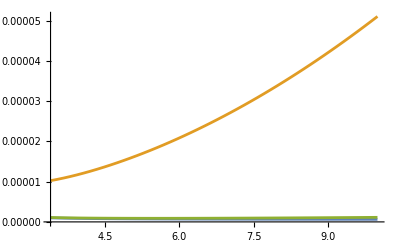

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0147204},{0.875,0.0260777},{1.375,0.0360527},{1.875,0.0390462},{2.375,0.0338369},{2.875,0.024409},{3.375,0.0155661},{3.875,0.00949552},{4.375,0.00599982},{4.875,0.00411114},{5.375,0.00304627},{5.875,0.00237553},{6.375,0.00190277},{6.875,0.00154347},{7.375,0.00125909},{7.875,0.00102934},{8.375,0.000841759},{8.875,0.000687729},{9.375,0.000560885},{9.875,0.000456318},{10.375,0.000370137},{10.875,0.000299201},{11.375,0.000240935},{11.875,0.00019321},{12.375,0.000154249},{12.875,0.000122567},{13.375,0.000096912},{13.875,0.0000762349},{14.375,0.0000596519},{14.875,0.0000464216},{15.375,0.0000359236},{15.875,0.0000276406},{16.375,0.0000211431},{16.875,0.0000160765},{17.375,0.0000121497},{17.875,9.12525×10^-6},{18.375,6.81045×10^-6},{18.875,5.0502×10^-6},{19.375,3.7204×10^-6},{19.875,2.72248×10^-6}}

8

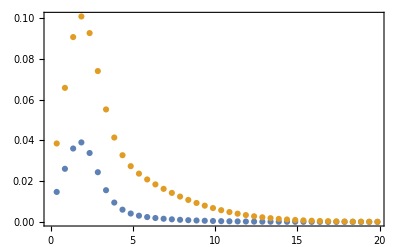

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{11.1479,8.84869,6.8102,5.03442,3.5239,2.28183,1.312,0.617614,0.196212,0.0217462,0,0.0212508,0.194041,0.61324,1.30531,2.27282,3.5126,5.02087,6.79442,8.83071,11.1278}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{9.55536,7.58459,5.83731,4.31522,3.02048,1.95585,1.12457,0.529384,0.168182,0.0186396,0,0.018215,0.166321,0.525635,1.11883,1.94813,3.0108,4.30361,5.82379,7.56918,9.53808}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.74897,1.23366,0.843499,0.562264,0.37251,0.227583,0.116019,0.0503745,0.0161977,0.00218803,0,0.00216151,0.0160969,0.050137,0.115557,0.226791,0.371816,0.561059,0.841652,1.23104,1.74546}

{-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.50483,1.06314,0.728713,0.487655,0.325009,0.195071,0.0994447,0.0431781,0.0138837,0.00187546,0,0.00185272,0.0137973,0.0429746,0.099049,0.194392,0.324414,0.486622,0.72713,1.0609,1.50182}

{-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.00216276},{0.875,0.00358207},{1.375,0.00500607},{1.875,0.00589802},{2.375,0.00596281},{2.875,0.00533601},{3.375,0.00438793},{3.875,0.00343758},{4.375,0.00263986},{4.875,0.00202392},{5.375,0.00156351},{5.875,0.00122096},{6.375,0.000963902},{6.875,0.000768375},{7.375,0.000617468},{7.875,0.000499368},{8.375,0.000405776},{8.875,0.000330789},{9.375,0.000270159},{9.875,0.00022078},{10.375,0.000180348},{10.875,0.000147123},{11.375,0.000119767},{11.875,0.0000972299},{12.375,0.0000786762},{12.875,0.0000634269},{13.375,0.0000509245},{13.875,0.0000407063},{14.375,0.0000323856},{14.875,0.0000256379},{15.375,0.0000201904},{15.875,0.000015814},{16.375,0.0000123159},{16.875,9.53518×10^-6},{17.375,7.33725×10^-6},{17.875,5.61032×10^-6},{18.375,4.26189×10^-6},{18.875,3.21583×10^-6},{19.375,2.40976×10^-6},{19.875,1.79295×10^-6}}

12

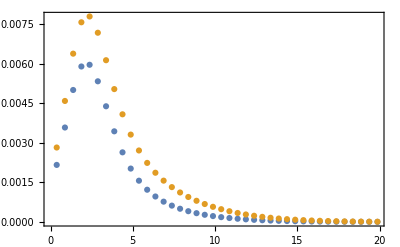

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{4.31184,3.4437,2.67116,1.99474,1.41512,0.933288,0.550614,0.268931,0.0899668,0.0105977,0,0.0103929,0.0891785,0.267472,0.548486,0.930505,1.41169,1.99067,2.66647,3.43838,4.3059}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{3.69586,2.95174,2.28957,1.70977,1.21296,0.799961,0.471954,0.230512,0.0771144,0.00908378,0,0.00890824,0.0764388,0.229261,0.470131,0.797575,1.21002,1.70629,2.28554,2.94718,3.69077}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.561222,0.424147,0.299338,0.203442,0.131923,0.0804105,0.044835,0.0215962,0.00774022,0.00115391,0,0.00114162,0.00770286,0.0215241,0.0447137,0.0802213,0.131645,0.203049,0.298806,0.423448,0.560571}

{-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.486762,0.363554,0.256576,0.174379,0.113077,0.0689233,0.03843,0.018511,0.00663448,0.000989068,0,0.000978533,0.00660245,0.0184492,0.038326,0.0687611,0.112838,0.174042,0.256119,0.362956,0.486204}

{-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0133131},{0.875,0.0215821},{1.375,0.0301183},{1.875,0.0361098},{2.375,0.0377928},{2.875,0.0355151},{3.375,0.0309509},{3.875,0.0257333},{4.375,0.0208155},{4.875,0.0165605},{5.375,0.013024},{5.875,0.0101466},{6.375,0.00783774},{6.875,0.00600583},{7.375,0.00456727},{7.875,0.00344868},{8.375,0.00258704},{8.875,0.00192922},{9.375,0.00143114},{9.875,0.00105687},{10.375,0.000777542},{10.875,0.000570338},{11.375,0.000417436},{11.875,0.000305101},{12.375,0.00022286},{12.875,0.000162808},{13.375,0.000119032},{13.875,0.0000871446},{14.375,0.0000639125},{14.875,0.0000469692},{15.375,0.0000345905},{15.875,0.0000255253},{16.375,0.0000188682},{16.875,0.0000139652},{17.375,0.0000103437},{17.875,7.66179×10^-6},{18.375,5.67151×10^-6},{18.875,4.19236×10^-6},{19.375,3.09234×10^-6},{19.875,2.27443×10^-6}}

11

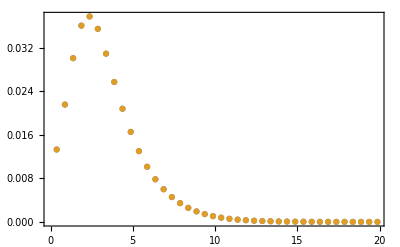

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{27.527,21.9654,17.0176,12.6872,8.97889,5.8994,3.45828,1.66852,0.542882,0.0592865,0,0.0579531,0.537548,1.65859,3.44379,5.88045,8.95556,12.6596,16.9857,21.9292,27.4865}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{23.5945,18.8275,14.5865,10.8747,7.69619,5.05663,2.96424,1.43016,0.465328,0.050817,0,0.0496741,0.460755,1.42165,2.95182,5.04038,7.67619,10.851,14.5592,18.7964,23.5599}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{4.12745,2.89422,1.94958,1.25152,0.76404,0.445111,0.215526,0.111887,0.0365286,0.00416518,0,0.0041015,0.0362338,0.111692,0.214663,0.444055,0.761521,1.24816,1.94504,2.88812,4.1194}

{-0.3,-0.25,-0.2,-0.15,-0.1,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.71793,2.61245,1.7625,1.12416,0.677748,0.40007,0.19045,0.101617,0.0313102,0.00357015,0,0.00351557,0.0310575,0.10145,0.189711,0.398397,0.675589,1.12128,1.75861,2.60613,3.7099}

{-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.1,-0.15,-0.2,-0.2,-0.25}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0001},{-0.00009},{-0.00008},{-0.00007},{-0.00006},{-0.00005},{-0.00004},{-0.00003},{-0.00002},{-0.00001},{0.},{0.00001},{0.00002},{0.00003},{0.00004},{0.00005},{0.00006},{0.00007},{0.00008},{0.00009},{0.0001}}

```mathematica
dataSet1
dataSet1bg
```

{9.55536,7.58459,5.83731,4.31522,3.02048,1.95585,1.12457,0.529384,0.168182,0.0186396,0,0.018215,0.166321,0.525635,1.11883,1.94813,3.0108,4.30361,5.82379,7.56918,9.53808}

{1.50483,1.06314,0.728713,0.487655,0.325009,0.195071,0.0994447,0.0431781,0.0138837,0.00187546,0,0.00185272,0.0137973,0.0429746,0.099049,0.194392,0.324414,0.486622,0.72713,1.0609,1.50182}

```mathematica
dataSet2
dataSet2bg
```

{3.69586,2.95174,2.28957,1.70977,1.21296,0.799961,0.471954,0.230512,0.0771144,0.00908378,0,0.00890824,0.0764388,0.229261,0.470131,0.797575,1.21002,1.70629,2.28554,2.94718,3.69077}

{0.486762,0.363554,0.256576,0.174379,0.113077,0.0689233,0.03843,0.018511,0.00663448,0.000989068,0,0.000978533,0.00660245,0.0184492,0.038326,0.0687611,0.112838,0.174042,0.256119,0.362956,0.486204}

```mathematica
dataSet3
dataSet3bg
```

{23.5945,18.8275,14.5865,10.8747,7.69619,5.05663,2.96424,1.43016,0.465328,0.050817,0,0.0496741,0.460755,1.42165,2.95182,5.04038,7.67619,10.851,14.5592,18.7964,23.5599}

{3.71793,2.61245,1.7625,1.12416,0.677748,0.40007,0.19045,0.101617,0.0313102,0.00357015,0,0.00351557,0.0310575,0.10145,0.189711,0.398397,0.675589,1.12128,1.75861,2.60613,3.7099}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

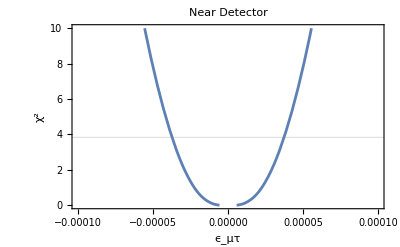

near_detector.pdf

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

InterpolatingFunction[…]

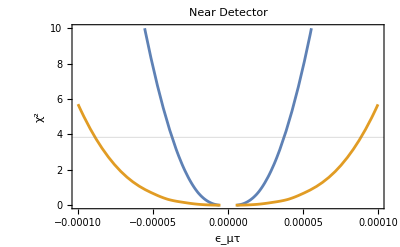

near_detector_bg.pdf

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_bg.pdf",%]
```

### chi - α

```mathematica
(*nteo - ndata + ndata*Log(ndata/nteo)*)
```

```mathematica
chi=nsi+(1+a)*ncp-(n+nc)+(n+nc)*Log[(n+nc)/(nsi+(1+a)*ncp)]+(a/sg)^2
```

-n-nc+(1+a) ncp+nsi+a^2/sg^2+(n+nc) Log[(n+nc)/((1+a) ncp+nsi)]

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->n,ncp->nc}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
%/.{sg->0.25,nc->2,n->11}
ContourPlot[{%%[[1,1,2]]/.sg->0.25,%%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→-(2 n+nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)},{a→(-2 n-nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)}}

{{a→-6.5625},{a→0.}}

-Graphics-

```mathematica
(* this means a=0. Consistent, since for a=0 we must recover the data_True (chi=0)*)
(* Thus, we only use the second root *)
```

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->10,ncp->1}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
ContourPlot[{%[[1,1,2]]/.sg->0.25,%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→1/4 (-22-sg^2-√(484+(-44+8 n+8 nc) sg^2+sg^4))},{a→1/4 (-22-sg^2+√(484+(-44+8 n+8 nc) sg^2+sg^4))}}

-Graphics-

```mathematica
(* only second root makes sense*)
```

## All data sets - near - NSI - s23

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(94593.79431933298 ee epS^2-16993.30788307618 ee^2 epS^2+729.0000000000001 ee^3 epS^2+259.51658341292085 ee s23^2-46.62087210720489 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-184751.02944044588 ee epS^2 s23^2+33986.61576615236 ee^2 epS^2 s23^2-1458.0000000000002 ee^3 epS^2 s23^2-259.5165834129209 ee s23^4+46.62087210720489 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+189187.5893080193 ee epS^2 s23^4-33986.61576615236 ee^2 epS^2 s23^4+1458.0000000000002 ee^3 epS^2 s23^4-6842.630720016514 ee epS s23 √(1-s23^2)+1258.7635468945318 ee^2 epS s23 √(1-s23^2)-54.00000000000001 ee^3 epS s23 √(1-s23^2)+14013.895504297725 ee epS s23^3 √(1-s23^2)-2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)+108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+2.437058034171625 ee epS^2 Sin[0.006402357909858133/ee]-0.03512714837222423 s23^2 Sin[0.006402357909858133/ee]+0.012713742369988023 ee s23^2 Sin[0.006402357909858133/ee]-0.0005454098974757641 ee^2 s23^2 Sin[0.006402357909858133/ee]+25.60769116335146 epS^2 s23^2 Sin[0.006402357909858133/ee]-11.705376221892895 ee epS^2 s23^2 Sin[0.006402357909858133/ee]+0.397603815259832 ee^2 epS^2 s23^2 Sin[0.006402357909858133/ee]+0.03512714837222423 s23^4 Sin[0.006402357909858133/ee]-0.012713742369988023 ee s23^4 Sin[0.006402357909858133/ee]+0.0005454098974757641 ee^2 s23^4 Sin[0.006402357909858133/ee]-25.60769116335146 epS^2 s23^4 Sin[0.006402357909858133/ee]+9.26831818772127 ee epS^2 s23^4 Sin[0.006402357909858133/ee]-0.397603815259832 ee^2 epS^2 s23^4 Sin[0.006402357909858133/ee]+0.9484330060500541 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-0.43353245266269974 ee epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]+0.014726067231845632 ee^2 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-1.8968660121001082 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+0.6865420879793533 ee epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]-0.029452134463691264 ee^2 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+Cos[δ] (ee s23 (0.00012107371492220409 epS^2 s23^2 √(1-s23^2)-1.6608191333311595*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (6.7263175012044485*^-6 s23-8.968423319544172*^-6 s23^3))+s23 (-0.0014111405425865087 epS^2 s23^2 √(1-s23^2)+1.935720911561134*^-6 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00007839669689246875 s23+0.00010452892922785395 s23^3))+ee^2 (-0.1888960369049804 √(1-s23^2) (-0.5 s23+1. s23^3)+137.70521090373074 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.275048249108618+10.200385992868943 s23^2-10.200385992868943 s23^4))+ee^3 (0.01620699299409185 √(1-s23^2) (-0.5 s23+1. s23^3)-11.814897892692962 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10939720271012002-0.8751776216809599 s23^2+0.8751776216809601 s23^4))+(s23 √(1-s23^2) (-0.0035238968220475553+0.007047793644095111 s23^2+ee (0.00030234499379971615-0.0006046899875994323 s23^2))+epS^2 s23 √(1-s23^2) (5.137841566545336-5.137841566545336 s23^2+ee (-0.4408190009599862+0.4408190009599862 s23^2))+epS (0.09514521419528398-0.4757260709764199 s23^2+0.3805808567811359 s23^4+ee (-0.008163314832592337+0.04081657416296169 s23^2-0.03265325933036935 s23^4))) Sin[0.006402357909858133/ee])+0.09514521419528398 epS s23^2 Sin[δ]-0.008163314832592337 ee epS s23^2 Sin[δ]+0.0035238968220475553 s23 √(1-s23^2) Sin[δ]-0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]+0.000026132232306963488 epS Sin[0.006402357909858133/ee] Sin[δ]-2.2421058289978646*^-6 ee epS Sin[0.006402357909858133/ee] Sin[δ]-1.2750482491086177 ee^2 epS Sin[0.006402357909858133/ee] Sin[δ]+0.10939720271012002 ee^3 epS Sin[0.006402357909858133/ee] Sin[δ]-0.00002613223216485494 epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]+2.2421058289978646*^-6 ee epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]-9.67860455780567*^-7 s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+8.304095677758028*^-8 ee s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+Cos[0.006402357909858133/ee] (4436.55919822007 ee epS^2-259.5165834129209 ee s23^2+46.62087210720489 ee^2 s23^2-1.9999999999999998 ee^3 s23^2+184751.03010979923 ee epS^2 s23^2-33986.61576615236 ee^2 epS^2 s23^2+1458.0000000000002 ee^3 epS^2 s23^2+259.51658341292085 ee s23^4-46.62087210720489 ee^2 s23^4+1.9999999999999998 ee^3 s23^4-189187.5893080193 ee epS^2 s23^4+33986.61576615236 ee^2 epS^2 s23^4-1458.0000000000002 ee^3 epS^2 s23^4+6842.6307448073785 ee epS s23 √(1-s23^2)-1258.7635468945318 ee^2 epS s23 √(1-s23^2)+54.00000000000001 ee^3 epS s23 √(1-s23^2)-14013.895504297725 ee epS s23^3 √(1-s23^2)+2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)-108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+(s23 √(1-s23^2) (9.67860455780567*^-7-1.9357209106729556*^-6 s23^2+ee^3 (0.008103496497045925-0.01620699299409185 s23^2)+ee (-8.304095677758028*^-8+1.6608191322209365*^-7 s23^2)+ee^2 (-0.0944480184524902+0.1888960369049804 s23^2))+epS^2 s23 √(1-s23^2) (-0.001411140544405498+0.0014111405425865087 s23^2+ee^2 (68.85260545186536-137.70521090373074 s23^2)+ee (0.00012107371497904751-0.00012107371486536067 s23^2)+ee^3 (-5.907448946346481+11.814897892692962 s23^2))+epS (-0.000026132232306963488+0.00013066116162008257 s23^2-0.00010452892917101053 s23^4+ee^3 (-0.10939720271012002+0.87517762168096 s23^2-0.8751776216809601 s23^4)+ee (2.2421058307742214*^-6-0.000011210529159200178 s23^2+8.9684233266496*^-6 s23^4)+ee^2 (1.2750482491086181-10.200385992868942 s23^2+10.200385992868945 s23^4))) Cos[δ]+0.09514521419528398 epS Sin[δ]-0.008163314832592337 ee epS Sin[δ]-0.09514521419528395 epS s23^2 Sin[δ]+0.008163314832592337 ee epS s23^2 Sin[δ]-0.0035238968220475553 s23 √(1-s23^2) Sin[δ]+0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]))/(-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0147204},{0.875,0.0260777},{1.375,0.0360527},{1.875,0.0390462},{2.375,0.0338369},{2.875,0.024409},{3.375,0.0155661},{3.875,0.00949552},{4.375,0.00599982},{4.875,0.00411114},{5.375,0.00304627},{5.875,0.00237553},{6.375,0.00190277},{6.875,0.00154347},{7.375,0.00125909},{7.875,0.00102934},{8.375,0.000841759},{8.875,0.000687729},{9.375,0.000560885},{9.875,0.000456318},{10.375,0.000370137},{10.875,0.000299201},{11.375,0.000240935},{11.875,0.00019321},{12.375,0.000154249},{12.875,0.000122567},{13.375,0.000096912},{13.875,0.0000762349},{14.375,0.0000596519},{14.875,0.0000464216},{15.375,0.0000359236},{15.875,0.0000276406},{16.375,0.0000211431},{16.875,0.0000160765},{17.375,0.0000121497},{17.875,9.12525×10^-6},{18.375,6.81045×10^-6},{18.875,5.0502×10^-6},{19.375,3.7204×10^-6},{19.875,2.72248×10^-6}}

82

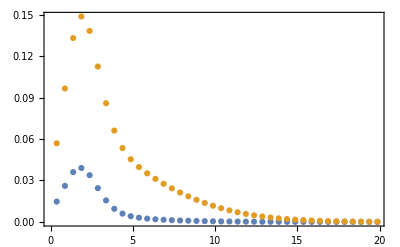

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{11.1603,11.1607,11.1596,11.1571,11.1532,11.1479,11.1412,11.1331,11.1236,11.1126,11.1003,6.8222,6.82256,6.82153,6.81913,6.81535,6.8102,6.80367,6.79577,6.7865,6.77586,6.76385,3.53521,3.53556,3.53461,3.53235,3.52877,3.5239,3.51771,3.51023,3.50144,3.49136,3.47998,1.32185,1.32218,1.32136,1.31939,1.31627,1.312,1.3066,1.30006,1.29239,1.2836,1.27368,0.202266,0.20248,0.201976,0.200758,0.198833,0.196212,0.192912,0.188953,0.184362,0.179169,0.173414,0.000170383,0.000183065,0.000155615,0.0000976173,0.0000328424,0,0.0000540246,0.000267971,0.000735669,0.00157535,0.00293459,0.19997,0.200202,0.19972,0.198527,0.19663,0.194041,0.190775,0.186854,0.182303,0.177155,0.171446,1.31484,1.31523,1.31447,1.31256,1.3095,1.30531,1.29997,1.29349,1.28589,1.27715,1.2673,3.52338,3.52384,3.52299,3.52084,3.51737,3.5126,3.50652,3.49913,3.49044,3.48045,3.46916,6.80569,6.80619,6.80532,6.80306,6.79943,6.79442,6.78804,6.78028,6.77114,6.76063,6.74874,11.1392,11.1398,11.1389,11.1366,11.1329,11.1278,11.1212,11.1133,11.1039,11.0932,11.081}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{9.56599,9.56629,9.56537,9.56324,9.55991,9.55536,9.54961,9.54265,9.53449,9.52512,9.51456,5.8476,5.8479,5.84703,5.84497,5.84173,5.83731,5.83172,5.82495,5.817,5.80788,5.79759,3.03018,3.03048,3.02967,3.02772,3.02466,3.02048,3.01518,3.00877,3.00124,2.99259,2.98284,1.13302,1.1333,1.13259,1.1309,1.12823,1.12457,1.11994,1.11434,1.10776,1.10023,1.09173,0.173371,0.173554,0.173122,0.172078,0.170428,0.168182,0.165353,0.16196,0.158025,0.153574,0.14864,0.000146043,0.000156913,0.000133384,0.000083672,0.0000281506,0,0.0000463068,0.000229689,0.000630574,0.0013503,0.00251536,0.171403,0.171602,0.171188,0.170166,0.16854,0.166321,0.163522,0.160161,0.15626,0.151847,0.146954,1.127,1.12734,1.12669,1.12505,1.12243,1.11883,1.11426,1.10871,1.10219,1.0947,1.08626,3.02004,3.02044,3.01971,3.01786,3.01489,3.0108,3.00559,2.99926,2.99181,2.98325,2.97357,5.83345,5.83388,5.83313,5.8312,5.82809,5.82379,5.81832,5.81167,5.80383,5.79482,5.78464,9.5479,9.54836,9.54761,9.54564,9.54247,9.53808,9.53248,9.52568,9.51766,9.50843,9.498}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
dataGen//Length
```

121

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.75055,1.75059,1.75046,1.75014,1.74964,1.74897,1.74811,1.74708,1.74587,1.74448,1.74291,0.844432,0.844459,0.844379,0.844193,0.843899,0.843499,0.842993,0.842381,0.841663,0.840842,0.839916,0.372849,0.37286,0.372831,0.372763,0.372656,0.37251,0.372326,0.372103,0.371844,0.371548,0.371215,0.116486,0.116501,0.116462,0.116369,0.116221,0.116019,0.115763,0.115454,0.115093,0.11468,0.114215,0.0163603,0.016366,0.0163525,0.0163198,0.0162681,0.0161977,0.016109,0.0160025,0.0158787,0.0157385,0.0155825,2.09626×10^-6,2.25318×10^-6,1.91365×10^-6,1.19789×10^-6,4.01651×10^-7,0,6.53683×10^-7,3.21862×10^-6,8.75922×10^-6,0.0000185665,0.0000341835,0.016256,0.0162622,0.0162493,0.0162173,0.0161664,0.0160969,0.0160092,0.0159037,0.015781,0.015642,0.0154872,0.116008,0.116027,0.115991,0.1159,0.115756,0.115557,0.115305,0.115,0.114642,0.114233,0.113772,0.372137,0.372151,0.372125,0.372061,0.371958,0.371816,0.371636,0.371418,0.371163,0.370871,0.370544,0.842525,0.842564,0.842496,0.842321,0.84204,0.841652,0.841158,0.840558,0.839853,0.839044,0.83813,1.74692,1.74699,1.74687,1.74658,1.74611,1.74546,1.74463,1.74362,1.74243,1.74107,1.73952}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.50618,1.50622,1.5061,1.50583,1.50541,1.50483,1.5041,1.50321,1.50217,1.50098,1.49964,0.729513,0.729536,0.729468,0.729308,0.729056,0.728713,0.728279,0.727755,0.72714,0.726436,0.725642,0.325299,0.325308,0.325284,0.325225,0.325134,0.325009,0.324851,0.32466,0.324438,0.324184,0.323899,0.0998451,0.0998584,0.0998249,0.0997446,0.0996178,0.0994447,0.0992255,0.0989608,0.098651,0.0982968,0.0978986,0.0140231,0.014028,0.0140164,0.0139884,0.0139441,0.0138837,0.0138077,0.0137164,0.0136104,0.0134901,0.0133564,1.7968×10^-6,1.93129×10^-6,1.64027×10^-6,1.02676×10^-6,3.44272×10^-7,0,5.603×10^-7,2.75881×10^-6,7.50791×10^-6,0.0000159141,0.0000293001,0.0139337,0.0139391,0.013928,0.0139005,0.0138569,0.0137973,0.0137221,0.0136317,0.0135266,0.0134074,0.0132748,0.0994355,0.0994513,0.0994204,0.099343,0.0992191,0.099049,0.0988329,0.0985714,0.0982649,0.0979139,0.0975191,0.324689,0.324701,0.324679,0.324624,0.324535,0.324414,0.324259,0.324073,0.323854,0.323604,0.323323,0.727878,0.727912,0.727854,0.727704,0.727463,0.72713,0.726707,0.726193,0.725589,0.724895,0.724112,1.50307,1.50313,1.50303,1.50278,1.50238,1.50182,1.50111,1.50025,1.49923,1.49806,1.49673}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

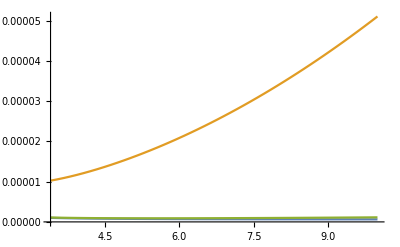

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.00216276},{0.875,0.00358207},{1.375,0.00500607},{1.875,0.00589802},{2.375,0.00596281},{2.875,0.00533601},{3.375,0.00438793},{3.875,0.00343758},{4.375,0.00263986},{4.875,0.00202392},{5.375,0.00156351},{5.875,0.00122096},{6.375,0.000963902},{6.875,0.000768375},{7.375,0.000617468},{7.875,0.000499368},{8.375,0.000405776},{8.875,0.000330789},{9.375,0.000270159},{9.875,0.00022078},{10.375,0.000180348},{10.875,0.000147123},{11.375,0.000119767},{11.875,0.0000972299},{12.375,0.0000786762},{12.875,0.0000634269},{13.375,0.0000509245},{13.875,0.0000407063},{14.375,0.0000323856},{14.875,0.0000256379},{15.375,0.0000201904},{15.875,0.000015814},{16.375,0.0000123159},{16.875,9.53518×10^-6},{17.375,7.33725×10^-6},{17.875,5.61032×10^-6},{18.375,4.26189×10^-6},{18.875,3.21583×10^-6},{19.375,2.40976×10^-6},{19.875,1.79295×10^-6}}

6

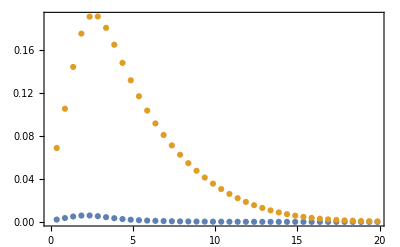

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{4.31455,4.31463,4.3144,4.31385,4.313,4.31184,4.31037,4.30859,4.30651,4.30412,4.30142,2.67382,2.6739,2.67367,2.67314,2.6723,2.67116,2.66972,2.66797,2.66592,2.66356,2.66091,1.41768,1.41776,1.41754,1.41703,1.41622,1.41512,1.41372,1.41203,1.41004,1.40776,1.40518,0.552959,0.553037,0.552841,0.552372,0.551629,0.550614,0.549326,0.547766,0.545934,0.543832,0.54146,0.0916428,0.0917017,0.0915629,0.0912268,0.0906943,0.0899668,0.0890464,0.0879353,0.0866367,0.0851541,0.0834919,0.0000365421,0.0000392621,0.0000333747,0.000020936,7.04371×10^-6,0,0.0000115867,0.0000574718,0.000157779,0.000337865,0.000629381,0.0908235,0.0908876,0.0907545,0.0904246,0.0898988,0.0891785,0.0882656,0.0871625,0.0858722,0.0843985,0.0827454,0.550757,0.550849,0.550669,0.550214,0.549486,0.548486,0.547212,0.545667,0.54385,0.541761,0.539402,1.41413,1.41423,1.41404,1.41356,1.41277,1.41169,1.41032,1.40865,1.40668,1.40442,1.40186,2.66896,2.66907,2.66888,2.66838,2.66758,2.66647,2.66506,2.66334,2.66132,2.65899,2.65636,4.30841,4.30852,4.30833,4.30783,4.30702,4.3059,4.30447,4.30273,4.30068,4.29832,4.29566}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{3.69819,3.69825,3.69805,3.69759,3.69686,3.69586,3.6946,3.69308,3.69129,3.68924,3.68693,2.29184,2.29191,2.29172,2.29126,2.29055,2.28957,2.28833,2.28683,2.28507,2.28305,2.28078,1.21515,1.21522,1.21504,1.2146,1.2139,1.21296,1.21176,1.21031,1.20861,1.20665,1.20444,0.473965,0.474032,0.473864,0.473461,0.472825,0.471954,0.470851,0.469513,0.467944,0.466142,0.464109,0.078551,0.0786015,0.0784825,0.0781944,0.077738,0.0771144,0.0763255,0.0753731,0.07426,0.0729892,0.0715645,0.0000313218,0.0000336532,0.0000286069,0.0000179452,6.03747×10^-6,0,9.93145×10^-6,0.0000492616,0.000135239,0.000289598,0.00053947,0.0778487,0.0779037,0.0777896,0.0775068,0.0770561,0.0764388,0.0756563,0.0747107,0.0736048,0.0723415,0.0709246,0.472077,0.472157,0.472002,0.471612,0.470988,0.470131,0.469039,0.467715,0.466157,0.464367,0.462345,1.21211,1.2122,1.21204,1.21162,1.21095,1.21002,1.20884,1.20741,1.20572,1.20379,1.2016,2.28768,2.28778,2.28761,2.28718,2.2865,2.28554,2.28433,2.28286,2.28113,2.27913,2.27688,3.69292,3.69302,3.69285,3.69242,3.69173,3.69077,3.68954,3.68805,3.6863,3.68428,3.68199}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.561415,0.56142,0.561404,0.561365,0.561305,0.561222,0.561118,0.560992,0.560844,0.560674,0.560483,0.299559,0.299566,0.299547,0.299503,0.299433,0.299338,0.299218,0.299073,0.298902,0.298707,0.298486,0.132067,0.132072,0.13206,0.132031,0.131985,0.131923,0.131845,0.13175,0.131638,0.131511,0.131366,0.0449183,0.0449211,0.0449141,0.0448974,0.0448711,0.044835,0.0447893,0.044734,0.0446691,0.0445947,0.0445108,0.00778278,0.00778428,0.00778076,0.00777223,0.00775871,0.00774022,0.00771679,0.00768846,0.00765527,0.00761727,0.00757453,5.30369×10^-7,5.69905×10^-7,4.84335×10^-7,3.03655×10^-7,1.0207×10^-7,0,1.67435×10^-7,8.28915×10^-7,2.27051×10^-6,4.84928×10^-6,9.00648×10^-6,0.00774466,0.00774628,0.00774291,0.00773453,0.00772117,0.00770286,0.0076796,0.00765146,0.00761845,0.00758065,0.0075381,0.0447943,0.0447975,0.0447911,0.044775,0.0447492,0.0447137,0.0446685,0.0446138,0.0445495,0.0444757,0.0443924,0.131781,0.131787,0.131777,0.131749,0.131705,0.131645,0.131567,0.131474,0.131364,0.131237,0.131094,0.299013,0.299022,0.299006,0.298965,0.298898,0.298806,0.298688,0.298546,0.298378,0.298185,0.297967,0.560749,0.560757,0.560744,0.560708,0.560651,0.560571,0.56047,0.560347,0.560202,0.560035,0.559847}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.486927,0.486932,0.486917,0.486884,0.486833,0.486762,0.486672,0.486564,0.486438,0.486292,0.486128,0.256765,0.256771,0.256755,0.256717,0.256657,0.256576,0.256473,0.256348,0.256202,0.256034,0.255845,0.1132,0.113204,0.113194,0.113169,0.11313,0.113077,0.11301,0.112929,0.112833,0.112723,0.1126,0.0385014,0.0385038,0.0384978,0.0384835,0.0384609,0.03843,0.0383908,0.0383434,0.0382878,0.038224,0.0381521,0.00667096,0.00667224,0.00666922,0.00666191,0.00665032,0.00663448,0.00661439,0.00659011,0.00656166,0.00652909,0.00649245,4.54602×10^-7,4.8849×10^-7,4.15144×10^-7,2.60275×10^-7,8.74884×10^-8,0,1.43515×10^-7,7.10499×10^-7,1.94615×10^-6,4.15652×10^-6,7.71984×10^-6,0.00663828,0.00663967,0.00663678,0.0066296,0.00661815,0.00660245,0.00658252,0.00655839,0.0065301,0.0064977,0.00646123,0.0383951,0.0383979,0.0383924,0.0383786,0.0383564,0.038326,0.0382873,0.0382404,0.0381853,0.038122,0.0380506,0.112956,0.112961,0.112951,0.112928,0.11289,0.112838,0.112772,0.112692,0.112597,0.112489,0.112366,0.256297,0.256305,0.256291,0.256255,0.256198,0.256119,0.256019,0.255896,0.255753,0.255587,0.2554,0.486356,0.486363,0.486352,0.486321,0.486272,0.486204,0.486117,0.486012,0.485887,0.485744,0.485583}

{-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
(* 3σ range: 0.433 - 0.623 *)
```

```mathematica
passoNSI=2./10;
passos23=.2/10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;Do[ss23=(0.582)-.1+passos23*kk;AppendTo[ls23d,{delta,ss23}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[ss23,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{kk,0,10}],{k,0,10}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

```mathematica
ls23d[[(((Length@dataGen)-1)/2+1)]]
```

{0.,0.582}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0114112},{0.875,0.018499},{1.375,0.0258157},{1.875,0.0309513},{2.375,0.0323938},{2.875,0.0304416},{3.375,0.0265293},{3.875,0.0220571},{4.375,0.0178419},{4.875,0.0141947},{5.375,0.0111635},{5.875,0.0086971},{6.375,0.00671806},{6.875,0.00514785},{7.375,0.0039148},{7.875,0.00295601},{8.375,0.00221746},{8.875,0.00165361},{9.375,0.00122669},{9.875,0.000905886},{10.375,0.000666465},{10.875,0.000488861},{11.375,0.000357802},{11.875,0.000261515},{12.375,0.000191023},{12.875,0.00013955},{13.375,0.000102028},{13.875,0.0000746953},{14.375,0.0000547821},{14.875,0.0000402593},{15.375,0.000029649},{15.875,0.0000218788},{16.375,0.0000161728},{16.875,0.0000119702},{17.375,8.86604×10^-6},{17.875,6.56725×10^-6},{18.375,4.86129×10^-6},{18.875,3.59345×10^-6},{19.375,2.65058×10^-6},{19.875,1.94951×10^-6}}

33

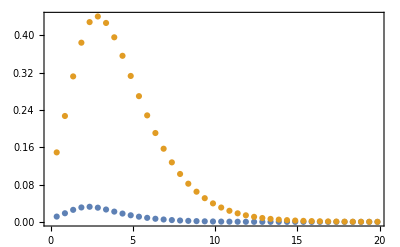

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{23.6102,23.6106,23.6093,23.6061,23.6012,23.5945,23.5861,23.5758,23.5638,23.5501,23.5345,14.6019,14.6023,14.601,14.5979,14.5931,14.5865,14.5782,14.5681,14.5563,14.5427,14.5274,7.71097,7.71143,7.71019,7.70723,7.70256,7.69619,7.68812,7.67834,7.66685,7.65367,7.63879,2.97784,2.9783,2.97716,2.97444,2.97013,2.96424,2.95676,2.94771,2.93709,2.92489,2.91112,0.475144,0.475489,0.474676,0.472708,0.469589,0.465328,0.459933,0.453418,0.4458,0.437097,0.427331,0.000210099,0.000225737,0.000191887,0.000120371,0.0000404978,0,0.0000666175,0.000330433,0.000907149,0.00194254,0.00361861,0.470392,0.470767,0.469987,0.468055,0.464976,0.460755,0.455405,0.448936,0.441366,0.432713,0.422999,2.96499,2.96553,2.96448,2.96184,2.95762,2.95182,2.94443,2.93546,2.92492,2.9128,2.8991,7.69028,7.69088,7.68978,7.68696,7.68243,7.67619,7.66825,7.6586,7.64724,7.63417,7.61941,14.5735,14.5742,14.5731,14.5702,14.5656,14.5592,14.551,14.5411,14.5294,14.516,14.5009,23.5743,23.575,23.5739,23.571,23.5663,23.5599,23.5517,23.5416,23.5298,23.5163,23.5009}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{20.2373,20.2377,20.2365,20.2338,20.2296,20.2239,20.2166,20.2079,20.1976,20.1858,20.1724,12.5159,12.5163,12.5151,12.5125,12.5084,12.5027,12.4956,12.487,12.4768,12.4652,12.4521,6.6094,6.6098,6.60873,6.6062,6.6022,6.59674,6.58981,6.58143,6.57159,6.56029,6.54753,2.55244,2.55282,2.55185,2.54952,2.54582,2.54077,2.53437,2.52661,2.5175,2.50705,2.49525,0.407267,0.407562,0.406865,0.405178,0.402505,0.398852,0.394228,0.388644,0.382114,0.374654,0.366284,0.000180084,0.000193489,0.000164475,0.000103176,0.0000347124,0,0.0000571007,0.000283229,0.000777556,0.00166504,0.00310167,0.403193,0.403514,0.402846,0.40119,0.39855,0.394933,0.390347,0.384802,0.378313,0.370897,0.362571,2.54142,2.54188,2.54098,2.53872,2.5351,2.53013,2.5238,2.51611,2.50707,2.49668,2.48495,6.59167,6.59219,6.59124,6.58882,6.58494,6.57959,6.57278,6.56451,6.55478,6.54358,6.53092,12.4916,12.4922,12.4912,12.4887,12.4848,12.4793,12.4723,12.4638,12.4538,12.4423,12.4293,20.2066,20.2071,20.2062,20.2037,20.1997,20.1942,20.1871,20.1786,20.1684,20.1568,20.1436}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.18458,3.18465,3.18444,3.18394,3.18317,3.18211,3.18077,3.17916,3.17726,3.17509,3.17265,1.52316,1.52321,1.52305,1.52268,1.52208,1.52127,1.52025,1.51902,1.51757,1.5159,1.51403,0.597247,0.597278,0.597195,0.596999,0.59669,0.596269,0.595736,0.595092,0.594338,0.593475,0.592505,0.175163,0.175178,0.17514,0.17505,0.174908,0.174714,0.174468,0.174173,0.173828,0.173435,0.172996,0.0300638,0.0300775,0.0300453,0.0299672,0.0298437,0.0296752,0.0294624,0.0292061,0.0289073,0.0285671,0.028187,3.94438×10^-6,4.23945×10^-6,3.60096×10^-6,2.25466×10^-6,7.56289×10^-7,0,1.23241×10^-6,6.07343×10^-6,0.0000165457,0.0000351134,0.0000647416,0.029824,0.0298389,0.029808,0.0297316,0.0296099,0.0294435,0.0292328,0.0289789,0.0286826,0.0283451,0.0279678,0.174567,0.174585,0.17455,0.174464,0.174325,0.174135,0.173895,0.173604,0.173265,0.172878,0.172444,0.59552,0.59556,0.595487,0.595301,0.595003,0.594592,0.594071,0.593438,0.592696,0.591845,0.590887,1.51907,1.51915,1.51902,1.51866,1.5181,1.51731,1.51632,1.5151,1.51368,1.51204,1.5102,3.17799,3.17809,3.17792,3.17746,3.17673,3.17571,3.17441,3.17283,3.17098,3.16885,3.16644}

{-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{2.8725,2.87256,2.87238,2.87195,2.87129,2.87038,2.86924,2.86785,2.86623,2.86437,2.86227,1.35699,1.35704,1.3569,1.35658,1.35607,1.35538,1.3545,1.35344,1.3522,1.35078,1.34917,0.534783,0.53481,0.534739,0.534571,0.534306,0.533945,0.533488,0.532936,0.53229,0.53155,0.530718,0.155854,0.155867,0.155835,0.155757,0.155635,0.155469,0.155259,0.155005,0.15471,0.154373,0.153996,0.025769,0.0257807,0.0257531,0.0256862,0.0255803,0.0254359,0.0252535,0.0250338,0.0247777,0.0244861,0.0241602,3.3809×10^-6,3.63381×10^-6,3.08654×10^-6,1.93257×10^-6,6.48247×10^-7,0,1.05635×10^-6,5.20579×10^-6,0.000014182,0.0000300972,0.0000554928,0.0255635,0.0255762,0.0255497,0.0254842,0.0253799,0.0252372,0.0250567,0.024839,0.0245851,0.0242958,0.0239724,0.155343,0.155359,0.155329,0.155255,0.155136,0.154973,0.154767,0.154518,0.154227,0.153895,0.153523,0.533303,0.533337,0.533274,0.533115,0.532859,0.532508,0.53206,0.531518,0.530882,0.530153,0.529332,1.35349,1.35356,1.35344,1.35314,1.35265,1.35198,1.35113,1.35009,1.34887,1.34747,1.34588,2.86684,2.86694,2.86679,2.8664,2.86576,2.86489,2.86378,2.86243,2.86084,2.85901,2.85695}

{-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.15,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0001,0.482},{-0.0001,0.502},{-0.0001,0.522},{-0.0001,0.542},{-0.0001,0.562},{-0.0001,0.582},{-0.0001,0.602},{-0.0001,0.622},{-0.0001,0.642},{-0.0001,0.662},{-0.0001,0.682},{-0.00008,0.482},{-0.00008,0.502},{-0.00008,0.522},{-0.00008,0.542},{-0.00008,0.562},{-0.00008,0.582},{-0.00008,0.602},{-0.00008,0.622},{-0.00008,0.642},{-0.00008,0.662},{-0.00008,0.682},{-0.00006,0.482},{-0.00006,0.502},{-0.00006,0.522},{-0.00006,0.542},{-0.00006,0.562},{-0.00006,0.582},{-0.00006,0.602},{-0.00006,0.622},{-0.00006,0.642},{-0.00006,0.662},{-0.00006,0.682},{-0.00004,0.482},{-0.00004,0.502},{-0.00004,0.522},{-0.00004,0.542},{-0.00004,0.562},{-0.00004,0.582},{-0.00004,0.602},{-0.00004,0.622},{-0.00004,0.642},{-0.00004,0.662},{-0.00004,0.682},{-0.00002,0.482},{-0.00002,0.502},{-0.00002,0.522},{-0.00002,0.542},{-0.00002,0.562},{-0.00002,0.582},{-0.00002,0.602},{-0.00002,0.622},{-0.00002,0.642},{-0.00002,0.662},{-0.00002,0.682},{0.,0.482},{0.,0.502},{0.,0.522},{0.,0.542},{0.,0.562},{0.,0.582},{0.,0.602},{0.,0.622},{0.,0.642},{0.,0.662},{0.,0.682},{0.00002,0.482},{0.00002,0.502},{0.00002,0.522},{0.00002,0.542},{0.00002,0.562},{0.00002,0.582},{0.00002,0.602},{0.00002,0.622},{0.00002,0.642},{0.00002,0.662},{0.00002,0.682},{0.00004,0.482},{0.00004,0.502},{0.00004,0.522},{0.00004,0.542},{0.00004,0.562},{0.00004,0.582},{0.00004,0.602},{0.00004,0.622},{0.00004,0.642},{0.00004,0.662},{0.00004,0.682},{0.00006,0.482},{0.00006,0.502},{0.00006,0.522},{0.00006,0.542},{0.00006,0.562},{0.00006,0.582},{0.00006,0.602},{0.00006,0.622},{0.00006,0.642},{0.00006,0.662},{0.00006,0.682},{0.00008,0.482},{0.00008,0.502},{0.00008,0.522},{0.00008,0.542},{0.00008,0.562},{0.00008,0.582},{0.00008,0.602},{0.00008,0.622},{0.00008,0.642},{0.00008,0.662},{0.00008,0.682},{0.0001,0.482},{0.0001,0.502},{0.0001,0.522},{0.0001,0.542},{0.0001,0.562},{0.0001,0.582},{0.0001,0.602},{0.0001,0.622},{0.0001,0.642},{0.0001,0.662},{0.0001,0.682}}

```mathematica
dataSet1
dataSet1bg
```

{9.56599,9.56629,9.56537,9.56324,9.55991,9.55536,9.54961,9.54265,9.53449,9.52512,9.51456,5.8476,5.8479,5.84703,5.84497,5.84173,5.83731,5.83172,5.82495,5.817,5.80788,5.79759,3.03018,3.03048,3.02967,3.02772,3.02466,3.02048,3.01518,3.00877,3.00124,2.99259,2.98284,1.13302,1.1333,1.13259,1.1309,1.12823,1.12457,1.11994,1.11434,1.10776,1.10023,1.09173,0.173371,0.173554,0.173122,0.172078,0.170428,0.168182,0.165353,0.16196,0.158025,0.153574,0.14864,0.000146043,0.000156913,0.000133384,0.000083672,0.0000281506,0,0.0000463068,0.000229689,0.000630574,0.0013503,0.00251536,0.171403,0.171602,0.171188,0.170166,0.16854,0.166321,0.163522,0.160161,0.15626,0.151847,0.146954,1.127,1.12734,1.12669,1.12505,1.12243,1.11883,1.11426,1.10871,1.10219,1.0947,1.08626,3.02004,3.02044,3.01971,3.01786,3.01489,3.0108,3.00559,2.99926,2.99181,2.98325,2.97357,5.83345,5.83388,5.83313,5.8312,5.82809,5.82379,5.81832,5.81167,5.80383,5.79482,5.78464,9.5479,9.54836,9.54761,9.54564,9.54247,9.53808,9.53248,9.52568,9.51766,9.50843,9.498}

{1.50618,1.50622,1.5061,1.50583,1.50541,1.50483,1.5041,1.50321,1.50217,1.50098,1.49964,0.729513,0.729536,0.729468,0.729308,0.729056,0.728713,0.728279,0.727755,0.72714,0.726436,0.725642,0.325299,0.325308,0.325284,0.325225,0.325134,0.325009,0.324851,0.32466,0.324438,0.324184,0.323899,0.0998451,0.0998584,0.0998249,0.0997446,0.0996178,0.0994447,0.0992255,0.0989608,0.098651,0.0982968,0.0978986,0.0140231,0.014028,0.0140164,0.0139884,0.0139441,0.0138837,0.0138077,0.0137164,0.0136104,0.0134901,0.0133564,1.7968×10^-6,1.93129×10^-6,1.64027×10^-6,1.02676×10^-6,3.44272×10^-7,0,5.603×10^-7,2.75881×10^-6,7.50791×10^-6,0.0000159141,0.0000293001,0.0139337,0.0139391,0.013928,0.0139005,0.0138569,0.0137973,0.0137221,0.0136317,0.0135266,0.0134074,0.0132748,0.0994355,0.0994513,0.0994204,0.099343,0.0992191,0.099049,0.0988329,0.0985714,0.0982649,0.0979139,0.0975191,0.324689,0.324701,0.324679,0.324624,0.324535,0.324414,0.324259,0.324073,0.323854,0.323604,0.323323,0.727878,0.727912,0.727854,0.727704,0.727463,0.72713,0.726707,0.726193,0.725589,0.724895,0.724112,1.50307,1.50313,1.50303,1.50278,1.50238,1.50182,1.50111,1.50025,1.49923,1.49806,1.49673}

```mathematica
dataSet2
dataSet2bg
```

{3.69819,3.69825,3.69805,3.69759,3.69686,3.69586,3.6946,3.69308,3.69129,3.68924,3.68693,2.29184,2.29191,2.29172,2.29126,2.29055,2.28957,2.28833,2.28683,2.28507,2.28305,2.28078,1.21515,1.21522,1.21504,1.2146,1.2139,1.21296,1.21176,1.21031,1.20861,1.20665,1.20444,0.473965,0.474032,0.473864,0.473461,0.472825,0.471954,0.470851,0.469513,0.467944,0.466142,0.464109,0.078551,0.0786015,0.0784825,0.0781944,0.077738,0.0771144,0.0763255,0.0753731,0.07426,0.0729892,0.0715645,0.0000313218,0.0000336532,0.0000286069,0.0000179452,6.03747×10^-6,0,9.93145×10^-6,0.0000492616,0.000135239,0.000289598,0.00053947,0.0778487,0.0779037,0.0777896,0.0775068,0.0770561,0.0764388,0.0756563,0.0747107,0.0736048,0.0723415,0.0709246,0.472077,0.472157,0.472002,0.471612,0.470988,0.470131,0.469039,0.467715,0.466157,0.464367,0.462345,1.21211,1.2122,1.21204,1.21162,1.21095,1.21002,1.20884,1.20741,1.20572,1.20379,1.2016,2.28768,2.28778,2.28761,2.28718,2.2865,2.28554,2.28433,2.28286,2.28113,2.27913,2.27688,3.69292,3.69302,3.69285,3.69242,3.69173,3.69077,3.68954,3.68805,3.6863,3.68428,3.68199}

{0.486927,0.486932,0.486917,0.486884,0.486833,0.486762,0.486672,0.486564,0.486438,0.486292,0.486128,0.256765,0.256771,0.256755,0.256717,0.256657,0.256576,0.256473,0.256348,0.256202,0.256034,0.255845,0.1132,0.113204,0.113194,0.113169,0.11313,0.113077,0.11301,0.112929,0.112833,0.112723,0.1126,0.0385014,0.0385038,0.0384978,0.0384835,0.0384609,0.03843,0.0383908,0.0383434,0.0382878,0.038224,0.0381521,0.00667096,0.00667224,0.00666922,0.00666191,0.00665032,0.00663448,0.00661439,0.00659011,0.00656166,0.00652909,0.00649245,4.54602×10^-7,4.8849×10^-7,4.15144×10^-7,2.60275×10^-7,8.74884×10^-8,0,1.43515×10^-7,7.10499×10^-7,1.94615×10^-6,4.15652×10^-6,7.71984×10^-6,0.00663828,0.00663967,0.00663678,0.0066296,0.00661815,0.00660245,0.00658252,0.00655839,0.0065301,0.0064977,0.00646123,0.0383951,0.0383979,0.0383924,0.0383786,0.0383564,0.038326,0.0382873,0.0382404,0.0381853,0.038122,0.0380506,0.112956,0.112961,0.112951,0.112928,0.11289,0.112838,0.112772,0.112692,0.112597,0.112489,0.112366,0.256297,0.256305,0.256291,0.256255,0.256198,0.256119,0.256019,0.255896,0.255753,0.255587,0.2554,0.486356,0.486363,0.486352,0.486321,0.486272,0.486204,0.486117,0.486012,0.485887,0.485744,0.485583}

```mathematica
dataSet3
dataSet3bg
```

{20.2373,20.2377,20.2365,20.2338,20.2296,20.2239,20.2166,20.2079,20.1976,20.1858,20.1724,12.5159,12.5163,12.5151,12.5125,12.5084,12.5027,12.4956,12.487,12.4768,12.4652,12.4521,6.6094,6.6098,6.60873,6.6062,6.6022,6.59674,6.58981,6.58143,6.57159,6.56029,6.54753,2.55244,2.55282,2.55185,2.54952,2.54582,2.54077,2.53437,2.52661,2.5175,2.50705,2.49525,0.407267,0.407562,0.406865,0.405178,0.402505,0.398852,0.394228,0.388644,0.382114,0.374654,0.366284,0.000180084,0.000193489,0.000164475,0.000103176,0.0000347124,0,0.0000571007,0.000283229,0.000777556,0.00166504,0.00310167,0.403193,0.403514,0.402846,0.40119,0.39855,0.394933,0.390347,0.384802,0.378313,0.370897,0.362571,2.54142,2.54188,2.54098,2.53872,2.5351,2.53013,2.5238,2.51611,2.50707,2.49668,2.48495,6.59167,6.59219,6.59124,6.58882,6.58494,6.57959,6.57278,6.56451,6.55478,6.54358,6.53092,12.4916,12.4922,12.4912,12.4887,12.4848,12.4793,12.4723,12.4638,12.4538,12.4423,12.4293,20.2066,20.2071,20.2062,20.2037,20.1997,20.1942,20.1871,20.1786,20.1684,20.1568,20.1436}

{2.8725,2.87256,2.87238,2.87195,2.87129,2.87038,2.86924,2.86785,2.86623,2.86437,2.86227,1.35699,1.35704,1.3569,1.35658,1.35607,1.35538,1.3545,1.35344,1.3522,1.35078,1.34917,0.534783,0.53481,0.534739,0.534571,0.534306,0.533945,0.533488,0.532936,0.53229,0.53155,0.530718,0.155854,0.155867,0.155835,0.155757,0.155635,0.155469,0.155259,0.155005,0.15471,0.154373,0.153996,0.025769,0.0257807,0.0257531,0.0256862,0.0255803,0.0254359,0.0252535,0.0250338,0.0247777,0.0244861,0.0241602,3.3809×10^-6,3.63381×10^-6,3.08654×10^-6,1.93257×10^-6,6.48247×10^-7,0,1.05635×10^-6,5.20579×10^-6,0.000014182,0.0000300972,0.0000554928,0.0255635,0.0255762,0.0255497,0.0254842,0.0253799,0.0252372,0.0250567,0.024839,0.0245851,0.0242958,0.0239724,0.155343,0.155359,0.155329,0.155255,0.155136,0.154973,0.154767,0.154518,0.154227,0.153895,0.153523,0.533303,0.533337,0.533274,0.533115,0.532859,0.532508,0.53206,0.531518,0.530882,0.530153,0.529332,1.35349,1.35356,1.35344,1.35314,1.35265,1.35198,1.35113,1.35009,1.34887,1.34747,1.34588,2.86684,2.86694,2.86679,2.8664,2.86576,2.86489,2.86378,2.86243,2.86084,2.85901,2.85695}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adriano/Dropbox/Neutrinos/Tau/Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

```mathematica
dataSet//Length
```

121

InterpolatingFunction[…]

{{-0.0001,33.4751},{-0.00008,20.6296},{-0.00006,10.8302},{-0.00004,4.1373},{-0.00002,0.644148},{0.,0},{0.00002,0.637693},{0.00004,4.11909},{0.00006,10.8004},{0.00008,20.5886},{0.0001,33.423}}

InterpolatingFunction[…]

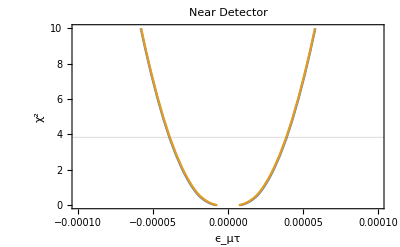

near_detector_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSet[[1+11*j;;11+11*j]]},{j,0,10}];
func=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSet[[1+5+11*j]]},{j,0,10}]
funcNo=Interpolation@%
Plot[{func[del],funcNo[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_s23.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

InterpolatingFunction[…]

{{-0.0001,4.86197},{-0.00008,2.34067},{-0.00006,0.972031},{-0.00004,0.293343},{-0.00002,0.0459541},{0.,0},{0.00002,0.045637},{0.00004,0.292348},{0.00006,0.96976},{0.00008,2.33523},{0.0001,4.85292}}

InterpolatingFunction[…]

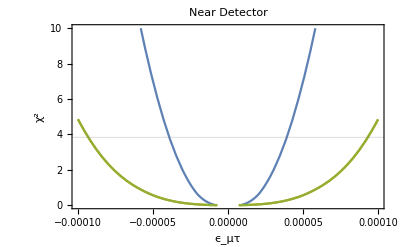

near_detector_bg_s23.pdf

```mathematica
Table[{ls23d[[1+11*j,1]],Min@dataSetbg[[1+11*j;;11+11*j]]},{j,0,10}];
funcbg=Interpolation@%
Table[{ls23d[[1+5+11*j,1]],dataSetbg[[1+5+11*j]]},{j,0,10}]
funcNobg=Interpolation@%
Plot[{func[del],funcbg[del],funcNobg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_bg_s23.pdf",%]
```

### chi - α

```mathematica
(*nteo - ndata + ndata*Log(ndata/nteo)*)
```

```mathematica
chi=nsi+(1+a)*ncp-(n+nc)+(n+nc)*Log[(n+nc)/(nsi+(1+a)*ncp)]+(a/sg)^2
```

-n-nc+(1+a) ncp+nsi+a^2/sg^2+(n+nc) Log[(n+nc)/((1+a) ncp+nsi)]

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->n,ncp->nc}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
%/.{sg->0.25,nc->2,n->11}
ContourPlot[{%%[[1,1,2]]/.sg->0.25,%%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→-(2 n+nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)},{a→(-2 n-nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)}}

{{a→-6.5625},{a→0.}}

-Graphics-

```mathematica
(* this means a=0. Consistent, since for a=0 we must recover the data_True (chi=0)*)
(* Thus, we only use the second root *)
```

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->10,ncp->1}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
ContourPlot[{%[[1,1,2]]/.sg->0.25,%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→1/4 (-22-sg^2-√(484+(-44+8 n+8 nc) sg^2+sg^4))},{a→1/4 (-22-sg^2+√(484+(-44+8 n+8 nc) sg^2+sg^4))}}

-Graphics-

```mathematica
(* only second root makes sense*)
```

## All data sets - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
sinal=Table[{bg[[i,1]],bg[[i,2]]+dataT[[i,2]]},{i,Length@bg}];
```

```mathematica
ListPlot[{bg,dataT,sinal},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

9

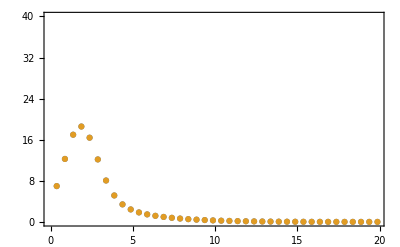

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,6.95631},{0.875,12.2351},{1.375,16.9446},{1.875,18.5355},{2.375,16.3634},{2.875,12.1403},{3.375,8.04398},{3.875,5.13964},{4.375,3.40362},{4.875,2.42284},{5.375,1.84224},{5.875,1.46025},{6.375,1.18223},{6.875,0.96633},{7.375,0.79289},{7.875,0.651239},{8.375,0.534604},{8.875,0.438183},{9.375,0.358339},{9.875,0.292214},{10.375,0.237505},{10.875,0.192326},{11.375,0.155112},{11.875,0.124557},{12.375,0.0995612},{12.875,0.0791971},{13.375,0.0626812},{13.875,0.0493508},{14.375,0.0386464},{14.875,0.0300967},{15.375,0.0233058},{15.875,0.0179429},{16.375,0.0137326},{16.875,0.0104471},{17.375,0.00789904},{17.875,0.00593526},{18.375,0.00443142},{18.875,0.00328727},{19.375,0.0024225},{19.875,0.00177327}},{{0.375,6.95777},{0.875,12.2377},{1.375,16.9482},{1.875,18.5394},{2.375,16.3668},{2.875,12.1428},{3.375,8.04561},{3.875,5.14065},{4.375,3.40426},{4.875,2.42328},{5.375,1.84257},{5.875,1.4605},{6.375,1.18243},{6.875,0.966486},{7.375,0.793014},{7.875,0.651338},{8.375,0.534683},{8.875,0.438246},{9.375,0.358389},{9.875,0.292254},{10.375,0.237537},{10.875,0.192351},{11.375,0.155132},{11.875,0.124572},{12.375,0.0995731},{12.875,0.0792064},{13.375,0.0626884},{13.875,0.0493563},{14.375,0.0386506},{14.875,0.0300999},{15.375,0.0233083},{15.875,0.0179447},{16.375,0.013734},{16.875,0.0104481},{17.375,0.0078998},{17.875,0.00593582},{18.375,0.00443183},{18.875,0.00328757},{19.375,0.00242271},{19.875,0.00177342}},{{0.375,6.95923},{0.875,12.2403},{1.375,16.9518},{1.875,18.5433},{2.375,16.3703},{2.875,12.1453},{3.375,8.04724},{3.875,5.14167},{4.375,3.40492},{4.875,2.42373},{5.375,1.8429},{5.875,1.46075},{6.375,1.18263},{6.875,0.966645},{7.375,0.793142},{7.875,0.651441},{8.375,0.534765},{8.875,0.438312},{9.375,0.358442},{9.875,0.292296},{10.375,0.23757},{10.875,0.192377},{11.375,0.155153},{11.875,0.124589},{12.375,0.099586},{12.875,0.0792164},{13.375,0.0626961},{13.875,0.0493623},{14.375,0.0386552},{14.875,0.0301034},{15.375,0.0233109},{15.875,0.0179468},{16.375,0.0137355},{16.875,0.0104493},{17.375,0.00790065},{17.875,0.00593644},{18.375,0.00443229},{18.875,0.0032879},{19.375,0.00242296},{19.875,0.0017736}},{{0.375,6.9607},{0.875,12.2429},{1.375,16.9553},{1.875,18.5472},{2.375,16.3737},{2.875,12.1478},{3.375,8.04889},{3.875,5.1427},{4.375,3.40558},{4.875,2.42419},{5.375,1.84324},{5.875,1.46101},{6.375,1.18283},{6.875,0.96681},{7.375,0.793274},{7.875,0.651547},{8.375,0.534851},{8.875,0.43838},{9.375,0.358497},{9.875,0.29234},{10.375,0.237605},{10.875,0.192405},{11.375,0.155175},{11.875,0.124606},{12.375,0.0995996},{12.875,0.0792271},{13.375,0.0627044},{13.875,0.0493687},{14.375,0.0386602},{14.875,0.0301072},{15.375,0.0233138},{15.875,0.017949},{16.375,0.0137372},{16.875,0.0104505},{17.375,0.00790158},{17.875,0.00593713},{18.375,0.0044328},{18.875,0.00328827},{19.375,0.00242323},{19.875,0.00177379}},{{0.375,6.96217},{0.875,12.2455},{1.375,16.9589},{1.875,18.5511},{2.375,16.3771},{2.875,12.1504},{3.375,8.05055},{3.875,5.14373},{4.375,3.40625},{4.875,2.42465},{5.375,1.84358},{5.875,1.46128},{6.375,1.18304},{6.875,0.966979},{7.375,0.79341},{7.875,0.651656},{8.375,0.534939},{8.875,0.438452},{9.375,0.358554},{9.875,0.292386},{10.375,0.237642},{10.875,0.192434},{11.375,0.155198},{11.875,0.124625},{12.375,0.0996142},{12.875,0.0792385},{13.375,0.0627133},{13.875,0.0493756},{14.375,0.0386655},{14.875,0.0301113},{15.375,0.023317},{15.875,0.0179514},{16.375,0.013739},{16.875,0.0104519},{17.375,0.0079026},{17.875,0.00593789},{18.375,0.00443336},{18.875,0.00328869},{19.375,0.00242353},{19.875,0.00177401}},{{0.375,6.96365},{0.875,12.2481},{1.375,16.9625},{1.875,18.555},{2.375,16.3806},{2.875,12.1529},{3.375,8.05221},{3.875,5.14478},{4.375,3.40692},{4.875,2.42512},{5.375,1.84393},{5.875,1.46155},{6.375,1.18326},{6.875,0.967152},{7.375,0.79355},{7.875,0.65177},{8.375,0.535031},{8.875,0.438526},{9.375,0.358614},{9.875,0.292434},{10.375,0.237681},{10.875,0.192465},{11.375,0.155223},{11.875,0.124644},{12.375,0.0996295},{12.875,0.0792506},{13.375,0.0627228},{13.875,0.049383},{14.375,0.0386712},{14.875,0.0301157},{15.375,0.0233204},{15.875,0.0179539},{16.375,0.0137409},{16.875,0.0104534},{17.375,0.0079037},{17.875,0.00593871},{18.375,0.00443397},{18.875,0.00328913},{19.375,0.00242386},{19.875,0.00177425}},{{0.375,6.96512},{0.875,12.2507},{1.375,16.9661},{1.875,18.559},{2.375,16.3841},{2.875,12.1555},{3.375,8.05389},{3.875,5.14583},{4.375,3.4076},{4.875,2.42559},{5.375,1.84428},{5.875,1.46182},{6.375,1.18348},{6.875,0.96733},{7.375,0.793694},{7.875,0.651887},{8.375,0.535126},{8.875,0.438603},{9.375,0.358676},{9.875,0.292484},{10.375,0.237721},{10.875,0.192498},{11.375,0.155248},{11.875,0.124665},{12.375,0.0996458},{12.875,0.0792634},{13.375,0.0627328},{13.875,0.0493908},{14.375,0.0386773},{14.875,0.0301204},{15.375,0.023324},{15.875,0.0179567},{16.375,0.013743},{16.875,0.0104549},{17.375,0.00790489},{17.875,0.0059396},{18.375,0.00443463},{18.875,0.00328962},{19.375,0.00242421},{19.875,0.00177451}},{{0.375,6.96661},{0.875,12.2533},{1.375,16.9698},{1.875,18.5629},{2.375,16.3876},{2.875,12.158},{3.375,8.05557},{3.875,5.14689},{4.375,3.40829},{4.875,2.42608},{5.375,1.84464},{5.875,1.46211},{6.375,1.18371},{6.875,0.967513},{7.375,0.793843},{7.875,0.652007},{8.375,0.535224},{8.875,0.438682},{9.375,0.358741},{9.875,0.292536},{10.375,0.237763},{10.875,0.192531},{11.375,0.155275},{11.875,0.124686},{12.375,0.0996628},{12.875,0.0792769},{13.375,0.0627434},{13.875,0.0493991},{14.375,0.0386838},{14.875,0.0301254},{15.375,0.0233278},{15.875,0.0179596},{16.375,0.0137453},{16.875,0.0104566},{17.375,0.00790616},{17.875,0.00594055},{18.375,0.00443534},{18.875,0.00329014},{19.375,0.0024246},{19.875,0.00177479}},{{0.375,6.96809},{0.875,12.2559},{1.375,16.9734},{1.875,18.5669},{2.375,16.391},{2.875,12.1606},{3.375,8.05726},{3.875,5.14795},{4.375,3.40899},{4.875,2.42657},{5.375,1.84501},{5.875,1.4624},{6.375,1.18394},{6.875,0.9677},{7.375,0.793995},{7.875,0.652131},{8.375,0.535325},{8.875,0.438764},{9.375,0.358807},{9.875,0.29259},{10.375,0.237807},{10.875,0.192566},{11.375,0.155304},{11.875,0.124709},{12.375,0.0996808},{12.875,0.079291},{13.375,0.0627546},{13.875,0.0494079},{14.375,0.0386906},{14.875,0.0301307},{15.375,0.0233319},{15.875,0.0179628},{16.375,0.0137477},{16.875,0.0104584},{17.375,0.00790753},{17.875,0.00594157},{18.375,0.0044361},{18.875,0.0032907},{19.375,0.00242501},{19.875,0.00177509}},{{0.375,6.96958},{0.875,12.2586},{1.375,16.977},{1.875,18.5709},{2.375,16.3945},{2.875,12.1632},{3.375,8.05896},{3.875,5.14903},{4.375,3.4097},{4.875,2.42706},{5.375,1.84538},{5.875,1.46269},{6.375,1.18417},{6.875,0.967892},{7.375,0.794151},{7.875,0.652259},{8.375,0.535429},{8.875,0.438849},{9.375,0.358877},{9.875,0.292647},{10.375,0.237852},{10.875,0.192603},{11.375,0.155333},{11.875,0.124732},{12.375,0.0996995},{12.875,0.0793059},{13.375,0.0627663},{13.875,0.0494171},{14.375,0.0386978},{14.875,0.0301363},{15.375,0.0233362},{15.875,0.0179661},{16.375,0.0137502},{16.875,0.0104604},{17.375,0.00790897},{17.875,0.00594266},{18.375,0.00443691},{18.875,0.0032913},{19.375,0.00242545},{19.875,0.00177541}},{{0.375,6.97108},{0.875,12.2612},{1.375,16.9807},{1.875,18.5749},{2.375,16.398},{2.875,12.1658},{3.375,8.06067},{3.875,5.15011},{4.375,3.41041},{4.875,2.42756},{5.375,1.84576},{5.875,1.46299},{6.375,1.18441},{6.875,0.968088},{7.375,0.794312},{7.875,0.65239},{8.375,0.535537},{8.875,0.438937},{9.375,0.358948},{9.875,0.292705},{10.375,0.237899},{10.875,0.192641},{11.375,0.155364},{11.875,0.124757},{12.375,0.0997192},{12.875,0.0793215},{13.375,0.0627787},{13.875,0.0494268},{14.375,0.0387054},{14.875,0.0301422},{15.375,0.0233408},{15.875,0.0179696},{16.375,0.0137529},{16.875,0.0104624},{17.375,0.00791051},{17.875,0.00594381},{18.375,0.00443776},{18.875,0.00329194},{19.375,0.00242592},{19.875,0.00177576}},{{0.375,6.97258},{0.875,12.2638},{1.375,16.9843},{1.875,18.5788},{2.375,16.4016},{2.875,12.1684},{3.375,8.06239},{3.875,5.15121},{4.375,3.41113},{4.875,2.42807},{5.375,1.84615},{5.875,1.46329},{6.375,1.18466},{6.875,0.968288},{7.375,0.794476},{7.875,0.652525},{8.375,0.535647},{8.875,0.439028},{9.375,0.359022},{9.875,0.292765},{10.375,0.237948},{10.875,0.192681},{11.375,0.155396},{11.875,0.124783},{12.375,0.0997397},{12.875,0.0793378},{13.375,0.0627915},{13.875,0.0494369},{14.375,0.0387133},{14.875,0.0301484},{15.375,0.0233455},{15.875,0.0179733},{16.375,0.0137557},{16.875,0.0104645},{17.375,0.00791213},{17.875,0.00594503},{18.375,0.00443867},{18.875,0.00329261},{19.375,0.00242641},{19.875,0.00177612}},{{0.375,6.97408},{0.875,12.2665},{1.375,16.988},{1.875,18.5829},{2.375,16.4051},{2.875,12.171},{3.375,8.06411},{3.875,5.15231},{4.375,3.41185},{4.875,2.42859},{5.375,1.84654},{5.875,1.4636},{6.375,1.18491},{6.875,0.968494},{7.375,0.794645},{7.875,0.652664},{8.375,0.535761},{8.875,0.439121},{9.375,0.359099},{9.875,0.292827},{10.375,0.237999},{10.875,0.192722},{11.375,0.155429},{11.875,0.124809},{12.375,0.099761},{12.875,0.0793548},{13.375,0.062805},{13.875,0.0494475},{14.375,0.0387216},{14.875,0.0301548},{15.375,0.0233506},{15.875,0.0179771},{16.375,0.0137586},{16.875,0.0104668},{17.375,0.00791384},{17.875,0.00594631},{18.375,0.00443963},{18.875,0.00329333},{19.375,0.00242694},{19.875,0.0017765}},{{0.375,6.97559},{0.875,12.2691},{1.375,16.9917},{1.875,18.5869},{2.375,16.4086},{2.875,12.1736},{3.375,8.06585},{3.875,5.15341},{4.375,3.41259},{4.875,2.42911},{5.375,1.84694},{5.875,1.46392},{6.375,1.18517},{6.875,0.968704},{7.375,0.794817},{7.875,0.652806},{8.375,0.535878},{8.875,0.439217},{9.375,0.359177},{9.875,0.292892},{10.375,0.238051},{10.875,0.192765},{11.375,0.155463},{11.875,0.124837},{12.375,0.0997832},{12.875,0.0793725},{13.375,0.062819},{13.875,0.0494586},{14.375,0.0387303},{14.875,0.0301616},{15.375,0.0233558},{15.875,0.0179812},{16.375,0.0137617},{16.875,0.0104692},{17.375,0.00791563},{17.875,0.00594766},{18.375,0.00444064},{18.875,0.00329407},{19.375,0.00242749},{19.875,0.00177691}},{{0.375,6.9771},{0.875,12.2718},{1.375,16.9953},{1.875,18.5909},{2.375,16.4122},{2.875,12.1763},{3.375,8.0676},{3.875,5.15453},{4.375,3.41333},{4.875,2.42964},{5.375,1.84734},{5.875,1.46424},{6.375,1.18543},{6.875,0.968918},{7.375,0.794994},{7.875,0.652952},{8.375,0.535998},{8.875,0.439316},{9.375,0.359258},{9.875,0.292958},{10.375,0.238106},{10.875,0.192809},{11.375,0.155499},{11.875,0.124866},{12.375,0.0998062},{12.875,0.0793909},{13.375,0.0628336},{13.875,0.0494701},{14.375,0.0387394},{14.875,0.0301687},{15.375,0.0233613},{15.875,0.0179854},{16.375,0.013765},{16.875,0.0104716},{17.375,0.00791751},{17.875,0.00594908},{18.375,0.0044417},{18.875,0.00329486},{19.375,0.00242807},{19.875,0.00177733}},{{0.375,6.97861},{0.875,12.2744},{1.375,16.999},{1.875,18.5949},{2.375,16.4157},{2.875,12.1789},{3.375,8.06935},{3.875,5.15565},{4.375,3.41407},{4.875,2.43018},{5.375,1.84775},{5.875,1.46457},{6.375,1.18569},{6.875,0.969137},{7.375,0.795175},{7.875,0.653101},{8.375,0.536121},{8.875,0.439418},{9.375,0.359342},{9.875,0.293027},{10.375,0.238162},{10.875,0.192854},{11.375,0.155536},{11.875,0.124895},{12.375,0.0998301},{12.875,0.0794099},{13.375,0.0628488},{13.875,0.0494821},{14.375,0.0387488},{14.875,0.0301761},{15.375,0.023367},{15.875,0.0179898},{16.375,0.0137684},{16.875,0.0104742},{17.375,0.00791947},{17.875,0.00595056},{18.375,0.00444281},{18.875,0.00329569},{19.375,0.00242868},{19.875,0.00177778}},{{0.375,6.98013},{0.875,12.2771},{1.375,17.0027},{1.875,18.599},{2.375,16.4193},{2.875,12.1816},{3.375,8.07111},{3.875,5.15679},{4.375,3.41483},{4.875,2.43072},{5.375,1.84817},{5.875,1.4649},{6.375,1.18597},{6.875,0.96936},{7.375,0.795359},{7.875,0.653254},{8.375,0.536248},{8.875,0.439522},{9.375,0.359428},{9.875,0.293097},{10.375,0.238219},{10.875,0.192901},{11.375,0.155574},{11.875,0.124926},{12.375,0.0998548},{12.875,0.0794297},{13.375,0.0628645},{13.875,0.0494946},{14.375,0.0387586},{14.875,0.0301837},{15.375,0.023373},{15.875,0.0179944},{16.375,0.0137719},{16.875,0.0104769},{17.375,0.00792152},{17.875,0.0059521},{18.375,0.00444397},{18.875,0.00329655},{19.375,0.00242932},{19.875,0.00177825}},{{0.375,6.98166},{0.875,12.2798},{1.375,17.0064},{1.875,18.603},{2.375,16.4229},{2.875,12.1842},{3.375,8.07288},{3.875,5.15793},{4.375,3.41559},{4.875,2.43127},{5.375,1.84859},{5.875,1.46524},{6.375,1.18624},{6.875,0.969588},{7.375,0.795548},{7.875,0.65341},{8.375,0.536377},{8.875,0.439629},{9.375,0.359516},{9.875,0.29317},{10.375,0.238279},{10.875,0.19295},{11.375,0.155613},{11.875,0.124958},{12.375,0.0998804},{12.875,0.0794502},{13.375,0.0628808},{13.875,0.0495075},{14.375,0.0387687},{14.875,0.0301917},{15.375,0.0233792},{15.875,0.0179992},{16.375,0.0137756},{16.875,0.0104797},{17.375,0.00792366},{17.875,0.00595371},{18.375,0.00444517},{18.875,0.00329745},{19.375,0.00242998},{19.875,0.00177874}},{{0.375,6.98318},{0.875,12.2825},{1.375,17.0101},{1.875,18.6071},{2.375,16.4265},{2.875,12.1869},{3.375,8.07466},{3.875,5.15907},{4.375,3.41636},{4.875,2.43182},{5.375,1.84902},{5.875,1.46558},{6.375,1.18652},{6.875,0.969821},{7.375,0.795741},{7.875,0.65357},{8.375,0.53651},{8.875,0.439739},{9.375,0.359607},{9.875,0.293244},{10.375,0.23834},{10.875,0.193},{11.375,0.155654},{11.875,0.124991},{12.375,0.0999069},{12.875,0.0794714},{13.375,0.0628977},{13.875,0.0495208},{14.375,0.0387793},{14.875,0.0301999},{15.375,0.0233856},{15.875,0.0180042},{16.375,0.0137794},{16.875,0.0104827},{17.375,0.00792588},{17.875,0.00595539},{18.375,0.00444643},{18.875,0.00329838},{19.375,0.00243068},{19.875,0.00177925}},{{0.375,6.98471},{0.875,12.2852},{1.375,17.0139},{1.875,18.6112},{2.375,16.4301},{2.875,12.1896},{3.375,8.07645},{3.875,5.16023},{4.375,3.41714},{4.875,2.43238},{5.375,1.84945},{5.875,1.46593},{6.375,1.18681},{6.875,0.970058},{7.375,0.795938},{7.875,0.653734},{8.375,0.536646},{8.875,0.439851},{9.375,0.3597},{9.875,0.293321},{10.375,0.238403},{10.875,0.193051},{11.375,0.155696},{11.875,0.125025},{12.375,0.0999342},{12.875,0.0794933},{13.375,0.0629152},{13.875,0.0495347},{14.375,0.0387902},{14.875,0.0302085},{15.375,0.0233923},{15.875,0.0180094},{16.375,0.0137834},{16.875,0.0104857},{17.375,0.00792819},{17.875,0.00595714},{18.375,0.00444774},{18.875,0.00329936},{19.375,0.0024314},{19.875,0.00177978}},{{0.375,6.98625},{0.875,12.2879},{1.375,17.0176},{1.875,18.6152},{2.375,16.4337},{2.875,12.1923},{3.375,8.07825},{3.875,5.16139},{4.375,3.41792},{4.875,2.43295},{5.375,1.84989},{5.875,1.46628},{6.375,1.1871},{6.875,0.9703},{7.375,0.796139},{7.875,0.653901},{8.375,0.536785},{8.875,0.439967},{9.375,0.359795},{9.875,0.2934},{10.375,0.238467},{10.875,0.193104},{11.375,0.155739},{11.875,0.12506},{12.375,0.0999623},{12.875,0.0795158},{13.375,0.0629332},{13.875,0.049549},{14.375,0.0388015},{14.875,0.0302173},{15.375,0.0233992},{15.875,0.0180147},{16.375,0.0137875},{16.875,0.0104889},{17.375,0.00793059},{17.875,0.00595895},{18.375,0.0044491},{18.875,0.00330037},{19.375,0.00243215},{19.875,0.00178033}}}

```mathematica
dataTrue
```

{{0.375,6.97108},{0.875,12.2612},{1.375,16.9807},{1.875,18.5749},{2.375,16.398},{2.875,12.1658},{3.375,8.06067},{3.875,5.15012},{4.375,3.41041},{4.875,2.42756},{5.375,1.84576},{5.875,1.46299},{6.375,1.18441},{6.875,0.968088},{7.375,0.794312},{7.875,0.65239},{8.375,0.535537},{8.875,0.438937},{9.375,0.358948},{9.875,0.292705},{10.375,0.237899},{10.875,0.192641},{11.375,0.155364},{11.875,0.124757},{12.375,0.0997192},{12.875,0.0793215},{13.375,0.0627787},{13.875,0.0494268},{14.375,0.0387054},{14.875,0.0301422},{15.375,0.0233408},{15.875,0.0179696},{16.375,0.0137529},{16.875,0.0104624},{17.375,0.00791051},{17.875,0.00594381},{18.375,0.00443777},{18.875,0.00329194},{19.375,0.00242592},{19.875,0.00177576}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],ls23d,"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{0.000483881,0.000393953,0.000312872,0.000240778,0.000177813,0.000124124,0.0000798549,0.0000451564,0.0000201788,5.07506×10^-6,0,5.11058×10^-6,0.0000205657,0.0000465264,0.0000831555,0.000130618,0.000189081,0.000258713,0.000339686,0.000432171,0.000536345}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{0.000414755,0.000337674,0.000268176,0.000206381,0.000152412,0.000106392,0.0000684471,0.0000387055,0.0000172961,4.35005×10^-6,0,4.38049×10^-6,0.0000176278,0.0000398797,0.0000712761,0.000111958,0.000162069,0.000221754,0.000291159,0.000370433,0.000459724}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.000345366,0.000281633,0.000224028,0.000172681,0.000127727,0.0000893011,0.0000575423,0.00003259,0.0000145861,3.67415×10^-6,0,3.71125×10^-6,0.0000149575,0.0000338902,0.0000606628,0.0000954308,0.000138351,0.000189584,0.000249289,0.00031763,0.000394772}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.000296028,0.0002414,0.000192024,0.000148012,0.00010948,0.0000765438,0.000049322,0.0000279343,0.0000125023,3.14927×10^-6,0,3.18107×10^-6,0.0000128207,0.0000290487,0.0000519967,0.0000817978,0.000118587,0.0001625,0.000213676,0.000272254,0.000338376}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

16

-Graphics-

```mathematica
$10^{-7}<|U_{\mu N|<10^{-6}$
```

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,1.14049},{0.875,1.86951},{1.375,2.6115},{1.875,3.10286},{2.375,3.18695},{2.875,2.91278},{3.375,2.45301},{3.875,1.96829},{4.375,1.5451},{4.875,1.20714},{5.375,0.94712},{5.875,0.748925},{6.375,0.597215},{6.875,0.479935},{7.375,0.388214},{7.875,0.315649},{8.375,0.257625},{8.875,0.210788},{9.375,0.172681},{9.875,0.141484},{10.375,0.115828},{10.875,0.0946676},{11.375,0.0771904},{11.875,0.0627543},{12.375,0.0508426},{12.875,0.0410332},{13.375,0.0329772},{13.875,0.0263832},{14.375,0.0210067},{14.875,0.0166415},{15.375,0.0131139},{15.875,0.0102772},{16.375,0.00800808},{16.875,0.0062029},{17.375,0.00477512},{17.875,0.00365264},{18.375,0.00277572},{18.875,0.0020951},{19.375,0.00157041},{19.875,0.00116876}},{{0.375,1.14071},{0.875,1.86988},{1.375,2.61203},{1.875,3.10349},{2.375,3.18759},{2.875,2.91336},{3.375,2.45349},{3.875,1.96866},{4.375,1.54539},{4.875,1.20736},{5.375,0.947287},{5.875,0.749053},{6.375,0.597314},{6.875,0.480012},{7.375,0.388274},{7.875,0.315697},{8.375,0.257663},{8.875,0.210818},{9.375,0.172705},{9.875,0.141503},{10.375,0.115843},{10.875,0.0946795},{11.375,0.0771998},{11.875,0.0627617},{12.375,0.0508484},{12.875,0.0410378},{13.375,0.0329808},{13.875,0.026386},{14.375,0.0210089},{14.875,0.0166432},{15.375,0.0131152},{15.875,0.0102782},{16.375,0.00800884},{16.875,0.00620348},{17.375,0.00477556},{17.875,0.00365297},{18.375,0.00277596},{18.875,0.00209528},{19.375,0.00157054},{19.875,0.00116885}},{{0.375,1.14095},{0.875,1.87026},{1.375,2.61256},{1.875,3.10412},{2.375,3.18824},{2.875,2.91394},{3.375,2.45397},{3.875,1.96904},{4.375,1.54568},{4.875,1.20759},{5.375,0.947458},{5.875,0.749185},{6.375,0.597416},{6.875,0.480092},{7.375,0.388337},{7.875,0.315747},{8.375,0.257702},{8.875,0.210849},{9.375,0.17273},{9.875,0.141523},{10.375,0.115859},{10.875,0.0946922},{11.375,0.0772099},{11.875,0.0627697},{12.375,0.0508548},{12.875,0.0410428},{13.375,0.0329847},{13.875,0.0263891},{14.375,0.0210113},{14.875,0.0166451},{15.375,0.0131167},{15.875,0.0102793},{16.375,0.00800969},{16.875,0.00620412},{17.375,0.00477604},{17.875,0.00365333},{18.375,0.00277624},{18.875,0.00209548},{19.375,0.00157069},{19.875,0.00116896}},{{0.375,1.14118},{0.875,1.87065},{1.375,2.61309},{1.875,3.10475},{2.375,3.18889},{2.875,2.91453},{3.375,2.45446},{3.875,1.96943},{4.375,1.54598},{4.875,1.20781},{5.375,0.947632},{5.875,0.749319},{6.375,0.597521},{6.875,0.480174},{7.375,0.388402},{7.875,0.315798},{8.375,0.257743},{8.875,0.210882},{9.375,0.172756},{9.875,0.141544},{10.375,0.115876},{10.875,0.0947056},{11.375,0.0772206},{11.875,0.0627783},{12.375,0.0508616},{12.875,0.0410482},{13.375,0.0329889},{13.875,0.0263924},{14.375,0.0210139},{14.875,0.0166471},{15.375,0.0131182},{15.875,0.0102806},{16.375,0.00801062},{16.875,0.00620484},{17.375,0.00477659},{17.875,0.00365374},{18.375,0.00277654},{18.875,0.00209571},{19.375,0.00157087},{19.875,0.00116909}},{{0.375,1.14141},{0.875,1.87103},{1.375,2.61363},{1.875,3.10539},{2.375,3.18954},{2.875,2.91512},{3.375,2.45495},{3.875,1.96982},{4.375,1.54628},{4.875,1.20804},{5.375,0.947808},{5.875,0.749456},{6.375,0.597628},{6.875,0.480258},{7.375,0.388468},{7.875,0.315851},{8.375,0.257785},{8.875,0.210916},{9.375,0.172783},{9.875,0.141566},{10.375,0.115894},{10.875,0.0947198},{11.375,0.077232},{11.875,0.0627874},{12.375,0.0508688},{12.875,0.041054},{13.375,0.0329935},{13.875,0.026396},{14.375,0.0210167},{14.875,0.0166493},{15.375,0.01312},{15.875,0.0102819},{16.375,0.00801165},{16.875,0.00620562},{17.375,0.00477718},{17.875,0.0036542},{18.375,0.00277688},{18.875,0.00209597},{19.375,0.00157105},{19.875,0.00116923}},{{0.375,1.14165},{0.875,1.87142},{1.375,2.61417},{1.875,3.10603},{2.375,3.19019},{2.875,2.91571},{3.375,2.45545},{3.875,1.97021},{4.375,1.54658},{4.875,1.20828},{5.375,0.947988},{5.875,0.749595},{6.375,0.597737},{6.875,0.480344},{7.375,0.388537},{7.875,0.315906},{8.375,0.257829},{8.875,0.210951},{9.375,0.172812},{9.875,0.141589},{10.375,0.115912},{10.875,0.0947347},{11.375,0.077244},{11.875,0.062797},{12.375,0.0508765},{12.875,0.0410601},{13.375,0.0329984},{13.875,0.0263999},{14.375,0.0210197},{14.875,0.0166517},{15.375,0.0131218},{15.875,0.0102833},{16.375,0.00801276},{16.875,0.00620648},{17.375,0.00477784},{17.875,0.00365469},{18.375,0.00277726},{18.875,0.00209625},{19.375,0.00157126},{19.875,0.00116938}},{{0.375,1.14188},{0.875,1.87181},{1.375,2.61472},{1.875,3.10668},{2.375,3.19085},{2.875,2.91631},{3.375,2.45595},{3.875,1.97061},{4.375,1.54689},{4.875,1.20851},{5.375,0.948171},{5.875,0.749738},{6.375,0.597849},{6.875,0.480433},{7.375,0.388607},{7.875,0.315963},{8.375,0.257875},{8.875,0.210988},{9.375,0.172842},{9.875,0.141613},{10.375,0.115932},{10.875,0.0947504},{11.375,0.0772567},{11.875,0.0628072},{12.375,0.0508847},{12.875,0.0410666},{13.375,0.0330036},{13.875,0.026404},{14.375,0.021023},{14.875,0.0166543},{15.375,0.0131238},{15.875,0.0102849},{16.375,0.00801396},{16.875,0.0062074},{17.375,0.00477854},{17.875,0.00365523},{18.375,0.00277766},{18.875,0.00209655},{19.375,0.00157149},{19.875,0.00116955}},{{0.375,1.14212},{0.875,1.8722},{1.375,2.61526},{1.875,3.10732},{2.375,3.19152},{2.875,2.91691},{3.375,2.45645},{3.875,1.97101},{4.375,1.5472},{4.875,1.20875},{5.375,0.948357},{5.875,0.749883},{6.375,0.597963},{6.875,0.480524},{7.375,0.38868},{7.875,0.316021},{8.375,0.257922},{8.875,0.211026},{9.375,0.172873},{9.875,0.141638},{10.375,0.115952},{10.875,0.0947669},{11.375,0.07727},{11.875,0.0628179},{12.375,0.0508933},{12.875,0.0410735},{13.375,0.0330091},{13.875,0.0264084},{14.375,0.0210264},{14.875,0.016657},{15.375,0.013126},{15.875,0.0102865},{16.375,0.00801525},{16.875,0.00620839},{17.375,0.0047793},{17.875,0.00365581},{18.375,0.0027781},{18.875,0.00209688},{19.375,0.00157174},{19.875,0.00116973}},{{0.375,1.14236},{0.875,1.87259},{1.375,2.61581},{1.875,3.10798},{2.375,3.19218},{2.875,2.91752},{3.375,2.45696},{3.875,1.97141},{4.375,1.54751},{4.875,1.209},{5.375,0.948546},{5.875,0.750031},{6.375,0.59808},{6.875,0.480617},{7.375,0.388755},{7.875,0.316081},{8.375,0.257971},{8.875,0.211065},{9.375,0.172905},{9.875,0.141664},{10.375,0.115973},{10.875,0.0947841},{11.375,0.0772839},{11.875,0.0628292},{12.375,0.0509024},{12.875,0.0410808},{13.375,0.0330149},{13.875,0.026413},{14.375,0.0210301},{14.875,0.0166599},{15.375,0.0131282},{15.875,0.0102883},{16.375,0.00801662},{16.875,0.00620946},{17.375,0.00478012},{17.875,0.00365643},{18.375,0.00277857},{18.875,0.00209724},{19.375,0.001572},{19.875,0.00116993}},{{0.375,1.1426},{0.875,1.87299},{1.375,2.61636},{1.875,3.10863},{2.375,3.19285},{2.875,2.91813},{3.375,2.45747},{3.875,1.97182},{4.375,1.54783},{4.875,1.20924},{5.375,0.948738},{5.875,0.750182},{6.375,0.5982},{6.875,0.480712},{7.375,0.388831},{7.875,0.316143},{8.375,0.258021},{8.875,0.211106},{9.375,0.172938},{9.875,0.141691},{10.375,0.115995},{10.875,0.0948021},{11.375,0.0772985},{11.875,0.062841},{12.375,0.0509119},{12.875,0.0410885},{13.375,0.0330211},{13.875,0.0264179},{14.375,0.021034},{14.875,0.016663},{15.375,0.0131306},{15.875,0.0102902},{16.375,0.00801809},{16.875,0.00621059},{17.375,0.00478099},{17.875,0.00365709},{18.375,0.00277908},{18.875,0.00209762},{19.375,0.00157228},{19.875,0.00117014}},{{0.375,1.14284},{0.875,1.87338},{1.375,2.61692},{1.875,3.10929},{2.375,3.19353},{2.875,2.91875},{3.375,2.45799},{3.875,1.97223},{4.375,1.54815},{4.875,1.20949},{5.375,0.948933},{5.875,0.750336},{6.375,0.598322},{6.875,0.480809},{7.375,0.38891},{7.875,0.316207},{8.375,0.258073},{8.875,0.211148},{9.375,0.172972},{9.875,0.14172},{10.375,0.116018},{10.875,0.0948208},{11.375,0.0773138},{11.875,0.0628534},{12.375,0.0509219},{12.875,0.0410965},{13.375,0.0330275},{13.875,0.026423},{14.375,0.0210381},{14.875,0.0166662},{15.375,0.0131332},{15.875,0.0102922},{16.375,0.00801964},{16.875,0.00621179},{17.375,0.00478191},{17.875,0.0036578},{18.375,0.00277961},{18.875,0.00209802},{19.375,0.00157259},{19.875,0.00117037}},{{0.375,1.14308},{0.875,1.87378},{1.375,2.61748},{1.875,3.10995},{2.375,3.19421},{2.875,2.91936},{3.375,2.4585},{3.875,1.97265},{4.375,1.54848},{4.875,1.20975},{5.375,0.949132},{5.875,0.750492},{6.375,0.598446},{6.875,0.480909},{7.375,0.38899},{7.875,0.316272},{8.375,0.258126},{8.875,0.211192},{9.375,0.173008},{9.875,0.141749},{10.375,0.116042},{10.875,0.0948403},{11.375,0.0773297},{11.875,0.0628663},{12.375,0.0509324},{12.875,0.041105},{13.375,0.0330343},{13.875,0.0264285},{14.375,0.0210424},{14.875,0.0166696},{15.375,0.0131359},{15.875,0.0102943},{16.375,0.00802129},{16.875,0.00621306},{17.375,0.00478289},{17.875,0.00365855},{18.375,0.00278018},{18.875,0.00209845},{19.375,0.00157291},{19.875,0.00117061}},{{0.375,1.14333},{0.875,1.87418},{1.375,2.61804},{1.875,3.11062},{2.375,3.19489},{2.875,2.91999},{3.375,2.45903},{3.875,1.97306},{4.375,1.54881},{4.875,1.21},{5.375,0.949333},{5.875,0.750651},{6.375,0.598573},{6.875,0.481011},{7.375,0.389073},{7.875,0.316339},{8.375,0.258181},{8.875,0.211237},{9.375,0.173045},{9.875,0.141779},{10.375,0.116067},{10.875,0.0948606},{11.375,0.0773462},{11.875,0.0628797},{12.375,0.0509433},{12.875,0.0411138},{13.375,0.0330414},{13.875,0.0264341},{14.375,0.0210469},{14.875,0.0166732},{15.375,0.0131387},{15.875,0.0102965},{16.375,0.00802302},{16.875,0.0062144},{17.375,0.00478393},{17.875,0.00365934},{18.375,0.00278078},{18.875,0.0020989},{19.375,0.00157325},{19.875,0.00117086}},{{0.375,1.14357},{0.875,1.87459},{1.375,2.6186},{1.875,3.11129},{2.375,3.19558},{2.875,2.92061},{3.375,2.45956},{3.875,1.97349},{4.375,1.54914},{4.875,1.21026},{5.375,0.949537},{5.875,0.750813},{6.375,0.598702},{6.875,0.481115},{7.375,0.389157},{7.875,0.316408},{8.375,0.258237},{8.875,0.211283},{9.375,0.173083},{9.875,0.14181},{10.375,0.116092},{10.875,0.0948816},{11.375,0.0773634},{11.875,0.0628937},{12.375,0.0509547},{12.875,0.041123},{13.375,0.0330488},{13.875,0.0264401},{14.375,0.0210517},{14.875,0.016677},{15.375,0.0131417},{15.875,0.0102989},{16.375,0.00802484},{16.875,0.00621582},{17.375,0.00478501},{17.875,0.00366017},{18.375,0.00278142},{18.875,0.00209938},{19.375,0.00157361},{19.875,0.00117113}},{{0.375,1.14382},{0.875,1.87499},{1.375,2.61916},{1.875,3.11196},{2.375,3.19627},{2.875,2.92125},{3.375,2.46009},{3.875,1.97392},{4.375,1.54947},{4.875,1.21053},{5.375,0.949745},{5.875,0.750977},{6.375,0.598834},{6.875,0.481222},{7.375,0.389244},{7.875,0.316479},{8.375,0.258295},{8.875,0.211331},{9.375,0.173122},{9.875,0.141842},{10.375,0.116119},{10.875,0.0949034},{11.375,0.0773812},{11.875,0.0629083},{12.375,0.0509665},{12.875,0.0411326},{13.375,0.0330565},{13.875,0.0264463},{14.375,0.0210566},{14.875,0.0166809},{15.375,0.0131448},{15.875,0.0103013},{16.375,0.00802675},{16.875,0.0062173},{17.375,0.00478616},{17.875,0.00366105},{18.375,0.00278208},{18.875,0.00209989},{19.375,0.00157399},{19.875,0.00117141}},{{0.375,1.14407},{0.875,1.8754},{1.375,2.61973},{1.875,3.11263},{2.375,3.19696},{2.875,2.92188},{3.375,2.46062},{3.875,1.97435},{4.375,1.54981},{4.875,1.21079},{5.375,0.949955},{5.875,0.751145},{6.375,0.598968},{6.875,0.481331},{7.375,0.389332},{7.875,0.316551},{8.375,0.258355},{8.875,0.21138},{9.375,0.173163},{9.875,0.141876},{10.375,0.116146},{10.875,0.0949259},{11.375,0.0773997},{11.875,0.0629234},{12.375,0.0509788},{12.875,0.0411425},{13.375,0.0330646},{13.875,0.0264527},{14.375,0.0210618},{14.875,0.016685},{15.375,0.013148},{15.875,0.0103039},{16.375,0.00802874},{16.875,0.00621885},{17.375,0.00478735},{17.875,0.00366197},{18.375,0.00278278},{18.875,0.00210042},{19.375,0.00157439},{19.875,0.00117171}},{{0.375,1.14432},{0.875,1.87581},{1.375,2.6203},{1.875,3.11331},{2.375,3.19766},{2.875,2.92252},{3.375,2.46116},{3.875,1.97478},{4.375,1.55016},{4.875,1.21106},{5.375,0.950168},{5.875,0.751315},{6.375,0.599105},{6.875,0.481441},{7.375,0.389423},{7.875,0.316625},{8.375,0.258416},{8.875,0.21143},{9.375,0.173204},{9.875,0.14191},{10.375,0.116175},{10.875,0.0949492},{11.375,0.0774188},{11.875,0.062939},{12.375,0.0509915},{12.875,0.0411529},{13.375,0.0330729},{13.875,0.0264595},{14.375,0.0210672},{14.875,0.0166893},{15.375,0.0131514},{15.875,0.0103065},{16.375,0.00803083},{16.875,0.00622047},{17.375,0.00478861},{17.875,0.00366293},{18.375,0.00278352},{18.875,0.00210097},{19.375,0.0015748},{19.875,0.00117202}},{{0.375,1.14457},{0.875,1.87622},{1.375,2.62088},{1.875,3.11399},{2.375,3.19836},{2.875,2.92316},{3.375,2.46171},{3.875,1.97522},{4.375,1.5505},{4.875,1.21134},{5.375,0.950385},{5.875,0.751488},{6.375,0.599245},{6.875,0.481555},{7.375,0.389515},{7.875,0.316701},{8.375,0.258478},{8.875,0.211482},{9.375,0.173247},{9.875,0.141945},{10.375,0.116204},{10.875,0.0949733},{11.375,0.0774385},{11.875,0.0629552},{12.375,0.0510047},{12.875,0.0411636},{13.375,0.0330816},{13.875,0.0264664},{14.375,0.0210728},{14.875,0.0166937},{15.375,0.013155},{15.875,0.0103093},{16.375,0.008033},{16.875,0.00622216},{17.375,0.00478991},{17.875,0.00366393},{18.375,0.00278428},{18.875,0.00210155},{19.375,0.00157524},{19.875,0.00117234}},{{0.375,1.14482},{0.875,1.87663},{1.375,2.62146},{1.875,3.11468},{2.375,3.19907},{2.875,2.92381},{3.375,2.46226},{3.875,1.97566},{4.375,1.55086},{4.875,1.21161},{5.375,0.950605},{5.875,0.751664},{6.375,0.599386},{6.875,0.48167},{7.375,0.38961},{7.875,0.316779},{8.375,0.258542},{8.875,0.211535},{9.375,0.173291},{9.875,0.141982},{10.375,0.116234},{10.875,0.0949981},{11.375,0.0774589},{11.875,0.0629719},{12.375,0.0510184},{12.875,0.0411747},{13.375,0.0330906},{13.875,0.0264737},{14.375,0.0210786},{14.875,0.0166984},{15.375,0.0131586},{15.875,0.0103122},{16.375,0.00803526},{16.875,0.00622392},{17.375,0.00479127},{17.875,0.00366498},{18.375,0.00278508},{18.875,0.00210215},{19.375,0.00157569},{19.875,0.00117268}},{{0.375,1.14508},{0.875,1.87705},{1.375,2.62204},{1.875,3.11537},{2.375,3.19978},{2.875,2.92446},{3.375,2.46281},{3.875,1.97611},{4.375,1.55121},{4.875,1.21189},{5.375,0.950827},{5.875,0.751842},{6.375,0.599531},{6.875,0.481788},{7.375,0.389706},{7.875,0.316859},{8.375,0.258608},{8.875,0.211589},{9.375,0.173336},{9.875,0.142019},{10.375,0.116265},{10.875,0.0950236},{11.375,0.07748},{11.875,0.0629892},{12.375,0.0510325},{12.875,0.0411862},{13.375,0.0330999},{13.875,0.0264812},{14.375,0.0210846},{14.875,0.0167032},{15.375,0.0131624},{15.875,0.0103152},{16.375,0.00803761},{16.875,0.00622575},{17.375,0.00479269},{17.875,0.00366606},{18.375,0.00278591},{18.875,0.00210278},{19.375,0.00157617},{19.875,0.00117304}},{{0.375,1.14533},{0.875,1.87747},{1.375,2.62262},{1.875,3.11606},{2.375,3.20049},{2.875,2.92512},{3.375,2.46336},{3.875,1.97656},{4.375,1.55157},{4.875,1.21218},{5.375,0.951053},{5.875,0.752023},{6.375,0.599678},{6.875,0.481907},{7.375,0.389805},{7.875,0.31694},{8.375,0.258675},{8.875,0.211645},{9.375,0.173382},{9.875,0.142058},{10.375,0.116297},{10.875,0.09505},{11.375,0.0775017},{11.875,0.063007},{12.375,0.0510471},{12.875,0.0411981},{13.375,0.0331095},{13.875,0.0264889},{14.375,0.0210908},{14.875,0.0167081},{15.375,0.0131664},{15.875,0.0103183},{16.375,0.00804005},{16.875,0.00622765},{17.375,0.00479416},{17.875,0.00366719},{18.375,0.00278677},{18.875,0.00210344},{19.375,0.00157666},{19.875,0.0011734}}}

```mathematica
dataTrue
```

{{0.375,1.14284},{0.875,1.87338},{1.375,2.61692},{1.875,3.10929},{2.375,3.19353},{2.875,2.91875},{3.375,2.45799},{3.875,1.97223},{4.375,1.54815},{4.875,1.20949},{5.375,0.948934},{5.875,0.750336},{6.375,0.598322},{6.875,0.48081},{7.375,0.38891},{7.875,0.316207},{8.375,0.258073},{8.875,0.211148},{9.375,0.172972},{9.875,0.14172},{10.375,0.116018},{10.875,0.0948209},{11.375,0.0773138},{11.875,0.0628534},{12.375,0.0509219},{12.875,0.0410965},{13.375,0.0330275},{13.875,0.0264231},{14.375,0.0210381},{14.875,0.0166662},{15.375,0.0131332},{15.875,0.0102922},{16.375,0.00801965},{16.875,0.00621179},{17.375,0.00478191},{17.875,0.0036578},{18.375,0.00277961},{18.875,0.00209802},{19.375,0.00157259},{19.875,0.00117037}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],ls23d,"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{0.000107563,0.0000880048,0.0000702355,0.0000543156,0.000040307,0.0000282727,0.0000182768,0.0000103847,4.6627×10^-6,1.17826×10^-6,0,1.19763×10^-6,4.84196×10^-6,0.0000110049,0.0000197595,0.0000311799,0.0000453412,0.0000623199,0.0000821933,0.00010504,0.000130939}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0000921967,0.0000754327,0.0000602019,0.0000465562,0.0000345488,0.0000242337,0.0000156659,8.90119×10^-6,3.9966×10^-6,1.00994×10^-6,0,1.02654×10^-6,4.15025×10^-6,9.43278×10^-6,0.0000169367,0.0000267256,0.0000388639,0.000053417,0.0000704514,0.0000900341,0.000112234}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.0000506844,0.0000416891,0.0000334466,0.0000260002,0.0000193939,0.0000136729,8.88348×10^-6,5.07272×10^-6,2.28889×10^-6,5.81232×10^-7,0,5.96474×10^-7,2.42294×10^-6,5.53271×10^-6,9.9801×10^-6,0.0000158204,0.00002311,0.0000319063,0.0000422675,0.000054253,0.0000679232}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.0000434438,0.0000357335,0.0000286685,0.0000222859,0.0000166233,0.0000117197,7.61441×10^-6,4.34805×10^-6,1.96191×10^-6,4.98199×10^-7,0,5.11264×10^-7,2.07681×10^-6,4.74233×10^-6,8.55437×10^-6,0.0000135604,0.0000198086,0.0000273482,0.0000362293,0.0000465026,0.0000582199}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

3

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,6.18396},{0.875,9.92319},{1.375,13.8347},{1.875,16.7132},{2.375,17.7471},{2.875,16.9952},{3.375,15.1158},{3.875,12.8127},{4.375,10.5392},{4.875,8.50136},{5.375,6.76104},{5.875,5.31522},{6.375,4.13633},{6.875,3.18922},{7.375,2.43805},{7.875,1.84925},{8.375,1.3927},{8.875,1.04219},{9.375,0.775533},{9.875,0.57433},{10.375,0.423625},{10.875,0.31147},{11.375,0.228468},{11.875,0.167327},{12.375,0.122457},{12.875,0.0896203},{13.375,0.0656334},{13.875,0.0481266},{14.375,0.0353484},{14.875,0.0260132},{15.375,0.0191817},{15.875,0.0141712},{16.375,0.0104864},{16.875,0.00776893},{17.375,0.00575924},{17.875,0.00426927},{18.375,0.00316243},{18.875,0.00233908},{19.375,0.00172626},{19.875,0.00127027}},{{0.375,6.18519},{0.875,9.92517},{1.375,13.8375},{1.875,16.7166},{2.375,17.7506},{2.875,16.9986},{3.375,15.1188},{3.875,12.8152},{4.375,10.5411},{4.875,8.50293},{5.375,6.76227},{5.875,5.31617},{6.375,4.13706},{6.875,3.18977},{7.375,2.43846},{7.875,1.84956},{8.375,1.39292},{8.875,1.04236},{9.375,0.775655},{9.875,0.574419},{10.375,0.423689},{10.875,0.311516},{11.375,0.228501},{11.875,0.167351},{12.375,0.122474},{12.875,0.0896322},{13.375,0.0656418},{13.875,0.0481326},{14.375,0.0353527},{14.875,0.0260162},{15.375,0.0191838},{15.875,0.0141727},{16.375,0.0104875},{16.875,0.00776971},{17.375,0.0057598},{17.875,0.00426968},{18.375,0.00316272},{18.875,0.00233928},{19.375,0.00172641},{19.875,0.00127038}},{{0.375,6.18643},{0.875,9.92718},{1.375,13.8403},{1.875,16.7199},{2.375,17.7542},{2.875,17.0019},{3.375,15.1217},{3.875,12.8176},{4.375,10.5432},{4.875,8.50453},{5.375,6.76352},{5.875,5.31714},{6.375,4.1378},{6.875,3.19033},{7.375,2.43889},{7.875,1.84988},{8.375,1.39316},{8.875,1.04253},{9.375,0.775781},{9.875,0.57451},{10.375,0.423755},{10.875,0.311564},{11.375,0.228535},{11.875,0.167375},{12.375,0.122491},{12.875,0.0896447},{13.375,0.0656508},{13.875,0.0481389},{14.375,0.0353572},{14.875,0.0260194},{15.375,0.0191862},{15.875,0.0141744},{16.375,0.0104887},{16.875,0.00777058},{17.375,0.00576042},{17.875,0.00427013},{18.375,0.00316304},{18.875,0.00233952},{19.375,0.00172658},{19.875,0.0012705}},{{0.375,6.18767},{0.875,9.92919},{1.375,13.8431},{1.875,16.7233},{2.375,17.7577},{2.875,17.0053},{3.375,15.1247},{3.875,12.8201},{4.375,10.5452},{4.875,8.50614},{5.375,6.76479},{5.875,5.31812},{6.375,4.13856},{6.875,3.1909},{7.375,2.43932},{7.875,1.8502},{8.375,1.3934},{8.875,1.0427},{9.375,0.77591},{9.875,0.574605},{10.375,0.423824},{10.875,0.311613},{11.375,0.228571},{11.875,0.167401},{12.375,0.12251},{12.875,0.0896579},{13.375,0.0656602},{13.875,0.0481457},{14.375,0.0353621},{14.875,0.0260229},{15.375,0.0191887},{15.875,0.0141762},{16.375,0.01049},{16.875,0.00777152},{17.375,0.0057611},{17.875,0.00427062},{18.375,0.0031634},{18.875,0.00233978},{19.375,0.00172677},{19.875,0.00127064}},{{0.375,6.18893},{0.875,9.93121},{1.375,13.8459},{1.875,16.7267},{2.375,17.7613},{2.875,17.0088},{3.375,15.1277},{3.875,12.8227},{4.375,10.5472},{4.875,8.50778},{5.375,6.76607},{5.875,5.31912},{6.375,4.13933},{6.875,3.19149},{7.375,2.43976},{7.875,1.85053},{8.375,1.39364},{8.875,1.04289},{9.375,0.776044},{9.875,0.574702},{10.375,0.423895},{10.875,0.311665},{11.375,0.228608},{11.875,0.167427},{12.375,0.122529},{12.875,0.0896717},{13.375,0.0656701},{13.875,0.0481528},{14.375,0.0353672},{14.875,0.0260266},{15.375,0.0191914},{15.875,0.0141781},{16.375,0.0104914},{16.875,0.00777255},{17.375,0.00576185},{17.875,0.00427117},{18.375,0.0031638},{18.875,0.00234007},{19.375,0.00172698},{19.875,0.00127079}},{{0.375,6.19019},{0.875,9.93325},{1.375,13.8488},{1.875,16.7302},{2.375,17.765},{2.875,17.0122},{3.375,15.1308},{3.875,12.8252},{4.375,10.5493},{4.875,8.50944},{5.375,6.76738},{5.875,5.32014},{6.375,4.14011},{6.875,3.19208},{7.375,2.44021},{7.875,1.85087},{8.375,1.3939},{8.875,1.04307},{9.375,0.776181},{9.875,0.574803},{10.375,0.423968},{10.875,0.311718},{11.375,0.228647},{11.875,0.167455},{12.375,0.122549},{12.875,0.0896862},{13.375,0.0656806},{13.875,0.0481604},{14.375,0.0353727},{14.875,0.0260306},{15.375,0.0191942},{15.875,0.0141802},{16.375,0.0104929},{16.875,0.00777365},{17.375,0.00576266},{17.875,0.00427176},{18.375,0.00316423},{18.875,0.00234038},{19.375,0.00172721},{19.875,0.00127096}},{{0.375,6.19147},{0.875,9.9353},{1.375,13.8516},{1.875,16.7336},{2.375,17.7686},{2.875,17.0157},{3.375,15.1338},{3.875,12.8278},{4.375,10.5514},{4.875,8.51112},{5.375,6.7687},{5.875,5.32117},{6.375,4.1409},{6.875,3.19269},{7.375,2.44067},{7.875,1.85122},{8.375,1.39416},{8.875,1.04327},{9.375,0.776323},{9.875,0.574907},{10.375,0.424044},{10.875,0.311773},{11.375,0.228687},{11.875,0.167484},{12.375,0.12257},{12.875,0.0897013},{13.375,0.0656916},{13.875,0.0481683},{14.375,0.0353784},{14.875,0.0260348},{15.375,0.0191973},{15.875,0.0141824},{16.375,0.0104946},{16.875,0.00777484},{17.375,0.00576353},{17.875,0.0042724},{18.375,0.0031647},{18.875,0.00234073},{19.375,0.00172746},{19.875,0.00127114}},{{0.375,6.19275},{0.875,9.93737},{1.375,13.8545},{1.875,16.7371},{2.375,17.7723},{2.875,17.0192},{3.375,15.1369},{3.875,12.8304},{4.375,10.5535},{4.875,8.51282},{5.375,6.77004},{5.875,5.32222},{6.375,4.14171},{6.875,3.19331},{7.375,2.44114},{7.875,1.85157},{8.375,1.39442},{8.875,1.04346},{9.375,0.776468},{9.875,0.575013},{10.375,0.424122},{10.875,0.31183},{11.375,0.228728},{11.875,0.167514},{12.375,0.122592},{12.875,0.0897172},{13.375,0.065703},{13.875,0.0481767},{14.375,0.0353845},{14.875,0.0260392},{15.375,0.0192005},{15.875,0.0141848},{16.375,0.0104963},{16.875,0.00777611},{17.375,0.00576446},{17.875,0.00427308},{18.375,0.0031652},{18.875,0.0023411},{19.375,0.00172773},{19.875,0.00127134}},{{0.375,6.19404},{0.875,9.93944},{1.375,13.8574},{1.875,16.7406},{2.375,17.776},{2.875,17.0227},{3.375,15.1401},{3.875,12.833},{4.375,10.5557},{4.875,8.51454},{5.375,6.7714},{5.875,5.32328},{6.375,4.14253},{6.875,3.19394},{7.375,2.44162},{7.875,1.85193},{8.375,1.39469},{8.875,1.04366},{9.375,0.776617},{9.875,0.575123},{10.375,0.424202},{10.875,0.311889},{11.375,0.228771},{11.875,0.167546},{12.375,0.122615},{12.875,0.0897337},{13.375,0.065715},{13.875,0.0481854},{14.375,0.0353909},{14.875,0.0260438},{15.375,0.0192039},{15.875,0.0141873},{16.375,0.0104981},{16.875,0.00777746},{17.375,0.00576546},{17.875,0.00427382},{18.375,0.00316574},{18.875,0.0023415},{19.375,0.00172802},{19.875,0.00127155}},{{0.375,6.19533},{0.875,9.94153},{1.375,13.8603},{1.875,16.7441},{2.375,17.7797},{2.875,17.0263},{3.375,15.1432},{3.875,12.8357},{4.375,10.5579},{4.875,8.51628},{5.375,6.77278},{5.875,5.32436},{6.375,4.14337},{6.875,3.19458},{7.375,2.44211},{7.875,1.8523},{8.375,1.39497},{8.875,1.04387},{9.375,0.77677},{9.875,0.575236},{10.375,0.424285},{10.875,0.31195},{11.375,0.228815},{11.875,0.167578},{12.375,0.122638},{12.875,0.0897508},{13.375,0.0657275},{13.875,0.0481945},{14.375,0.0353975},{14.875,0.0260487},{15.375,0.0192075},{15.875,0.0141899},{16.375,0.0105001},{16.875,0.0077789},{17.375,0.00576652},{17.875,0.0042746},{18.375,0.00316632},{18.875,0.00234192},{19.375,0.00172834},{19.875,0.00127178}},{{0.375,6.19664},{0.875,9.94363},{1.375,13.8633},{1.875,16.7476},{2.375,17.7835},{2.875,17.0298},{3.375,15.1464},{3.875,12.8384},{4.375,10.5601},{4.875,8.51804},{5.375,6.77418},{5.875,5.32545},{6.375,4.14422},{6.875,3.19524},{7.375,2.44261},{7.875,1.85268},{8.375,1.39525},{8.875,1.04408},{9.375,0.776927},{9.875,0.575352},{10.375,0.424371},{10.875,0.312012},{11.375,0.228861},{11.875,0.167611},{12.375,0.122663},{12.875,0.0897686},{13.375,0.0657405},{13.875,0.048204},{14.375,0.0354045},{14.875,0.0260538},{15.375,0.0192112},{15.875,0.0141927},{16.375,0.0105021},{16.875,0.00778041},{17.375,0.00576764},{17.875,0.00427543},{18.375,0.00316693},{18.875,0.00234237},{19.375,0.00172867},{19.875,0.00127203}},{{0.375,6.19795},{0.875,9.94574},{1.375,13.8662},{1.875,16.7512},{2.375,17.7872},{2.875,17.0334},{3.375,15.1496},{3.875,12.8411},{4.375,10.5623},{4.875,8.51983},{5.375,6.77559},{5.875,5.32656},{6.375,4.14508},{6.875,3.1959},{7.375,2.44312},{7.875,1.85306},{8.375,1.39554},{8.875,1.0443},{9.375,0.777088},{9.875,0.575471},{10.375,0.424458},{10.875,0.312077},{11.375,0.228908},{11.875,0.167646},{12.375,0.122688},{12.875,0.0897871},{13.375,0.0657541},{13.875,0.0482139},{14.375,0.0354118},{14.875,0.0260592},{15.375,0.0192152},{15.875,0.0141956},{16.375,0.0105043},{16.875,0.007782},{17.375,0.00576882},{17.875,0.0042763},{18.375,0.00316758},{18.875,0.00234285},{19.375,0.00172902},{19.875,0.00127229}},{{0.375,6.19928},{0.875,9.94786},{1.375,13.8692},{1.875,16.7547},{2.375,17.791},{2.875,17.0371},{3.375,15.1528},{3.875,12.8438},{4.375,10.5645},{4.875,8.52163},{5.375,6.77703},{5.875,5.32769},{6.375,4.14596},{6.875,3.19658},{7.375,2.44364},{7.875,1.85346},{8.375,1.39584},{8.875,1.04452},{9.375,0.777252},{9.875,0.575593},{10.375,0.424548},{10.875,0.312143},{11.375,0.228957},{11.875,0.167681},{12.375,0.122714},{12.875,0.0898062},{13.375,0.0657681},{13.875,0.0482242},{14.375,0.0354194},{14.875,0.0260648},{15.375,0.0192193},{15.875,0.0141987},{16.375,0.0105065},{16.875,0.00778368},{17.375,0.00577006},{17.875,0.00427723},{18.375,0.00316827},{18.875,0.00234336},{19.375,0.0017294},{19.875,0.00127257}},{{0.375,6.20061},{0.875,9.95},{1.375,13.8721},{1.875,16.7583},{2.375,17.7948},{2.875,17.0407},{3.375,15.156},{3.875,12.8465},{4.375,10.5668},{4.875,8.52346},{5.375,6.77848},{5.875,5.32884},{6.375,4.14685},{6.875,3.19727},{7.375,2.44416},{7.875,1.85386},{8.375,1.39614},{8.875,1.04474},{9.375,0.777421},{9.875,0.575718},{10.375,0.424641},{10.875,0.312211},{11.375,0.229007},{11.875,0.167718},{12.375,0.122741},{12.875,0.089826},{13.375,0.0657826},{13.875,0.0482349},{14.375,0.0354272},{14.875,0.0260706},{15.375,0.0192236},{15.875,0.0142018},{16.375,0.0105089},{16.875,0.00778544},{17.375,0.00577137},{17.875,0.0042782},{18.375,0.00316899},{18.875,0.00234389},{19.375,0.00172979},{19.875,0.00127286}},{{0.375,6.20195},{0.875,9.95215},{1.375,13.8751},{1.875,16.762},{2.375,17.7987},{2.875,17.0444},{3.375,15.1593},{3.875,12.8493},{4.375,10.5691},{4.875,8.52531},{5.375,6.77995},{5.875,5.32999},{6.375,4.14776},{6.875,3.19797},{7.375,2.4447},{7.875,1.85426},{8.375,1.39644},{8.875,1.04498},{9.375,0.777593},{9.875,0.575846},{10.375,0.424736},{10.875,0.312281},{11.375,0.229059},{11.875,0.167756},{12.375,0.122769},{12.875,0.0898465},{13.375,0.0657977},{13.875,0.048246},{14.375,0.0354354},{14.875,0.0260766},{15.375,0.0192281},{15.875,0.0142052},{16.375,0.0105114},{16.875,0.00778728},{17.375,0.00577274},{17.875,0.00427921},{18.375,0.00316974},{18.875,0.00234446},{19.375,0.00173021},{19.875,0.00127316}},{{0.375,6.2033},{0.875,9.95431},{1.375,13.8782},{1.875,16.7656},{2.375,17.8025},{2.875,17.0481},{3.375,15.1626},{3.875,12.8521},{4.375,10.5714},{4.875,8.52717},{5.375,6.78144},{5.875,5.33117},{6.375,4.14867},{6.875,3.19868},{7.375,2.44524},{7.875,1.85468},{8.375,1.39676},{8.875,1.04521},{9.375,0.77777},{9.875,0.575977},{10.375,0.424833},{10.875,0.312353},{11.375,0.229112},{11.875,0.167795},{12.375,0.122797},{12.875,0.0898676},{13.375,0.0658133},{13.875,0.0482575},{14.375,0.0354439},{14.875,0.0260829},{15.375,0.0192328},{15.875,0.0142086},{16.375,0.0105139},{16.875,0.0077892},{17.375,0.00577417},{17.875,0.00428028},{18.375,0.00317054},{18.875,0.00234504},{19.375,0.00173064},{19.875,0.00127349}},{{0.375,6.20465},{0.875,9.95648},{1.375,13.8812},{1.875,16.7693},{2.375,17.8064},{2.875,17.0518},{3.375,15.1659},{3.875,12.8549},{4.375,10.5737},{4.875,8.52906},{5.375,6.78295},{5.875,5.33236},{6.375,4.1496},{6.875,3.1994},{7.375,2.4458},{7.875,1.8551},{8.375,1.39708},{8.875,1.04545},{9.375,0.77795},{9.875,0.576111},{10.375,0.424932},{10.875,0.312427},{11.375,0.229166},{11.875,0.167835},{12.375,0.122827},{12.875,0.0898894},{13.375,0.0658293},{13.875,0.0482694},{14.375,0.0354527},{14.875,0.0260894},{15.375,0.0192376},{15.875,0.0142122},{16.375,0.0105166},{16.875,0.0077912},{17.375,0.00577566},{17.875,0.00428139},{18.375,0.00317136},{18.875,0.00234566},{19.375,0.0017311},{19.875,0.00127382}},{{0.375,6.20602},{0.875,9.95867},{1.375,13.8842},{1.875,16.7729},{2.375,17.8103},{2.875,17.0556},{3.375,15.1693},{3.875,12.8578},{4.375,10.5761},{4.875,8.53097},{5.375,6.78448},{5.875,5.33357},{6.375,4.15055},{6.875,3.20013},{7.375,2.44636},{7.875,1.85553},{8.375,1.3974},{8.875,1.0457},{9.375,0.778134},{9.875,0.576249},{10.375,0.425034},{10.875,0.312502},{11.375,0.229222},{11.875,0.167876},{12.375,0.122857},{12.875,0.0899119},{13.375,0.0658459},{13.875,0.0482816},{14.375,0.0354618},{14.875,0.0260962},{15.375,0.0192426},{15.875,0.014216},{16.375,0.0105194},{16.875,0.00779328},{17.375,0.00577721},{17.875,0.00428255},{18.375,0.00317223},{18.875,0.0023463},{19.375,0.00173158},{19.875,0.00127418}},{{0.375,6.20739},{0.875,9.96086},{1.375,13.8873},{1.875,16.7766},{2.375,17.8143},{2.875,17.0594},{3.375,15.1727},{3.875,12.8607},{4.375,10.5784},{4.875,8.5329},{5.375,6.78603},{5.875,5.33479},{6.375,4.15151},{6.875,3.20087},{7.375,2.44693},{7.875,1.85597},{8.375,1.39774},{8.875,1.04595},{9.375,0.778322},{9.875,0.576389},{10.375,0.425139},{10.875,0.312579},{11.375,0.229279},{11.875,0.167919},{12.375,0.122889},{12.875,0.089935},{13.375,0.065863},{13.875,0.0482943},{14.375,0.0354712},{14.875,0.0261031},{15.375,0.0192478},{15.875,0.0142198},{16.375,0.0105223},{16.875,0.00779544},{17.375,0.00577883},{17.875,0.00428376},{18.375,0.00317313},{18.875,0.00234697},{19.375,0.00173208},{19.875,0.00127454}},{{0.375,6.20877},{0.875,9.96307},{1.375,13.8904},{1.875,16.7804},{2.375,17.8182},{2.875,17.0632},{3.375,15.1761},{3.875,12.8636},{4.375,10.5808},{4.875,8.53486},{5.375,6.78759},{5.875,5.33603},{6.375,4.15248},{6.875,3.20163},{7.375,2.44752},{7.875,1.85641},{8.375,1.39808},{8.875,1.0462},{9.375,0.778513},{9.875,0.576532},{10.375,0.425245},{10.875,0.312659},{11.375,0.229338},{11.875,0.167962},{12.375,0.122921},{12.875,0.0899588},{13.375,0.0658806},{13.875,0.0483074},{14.375,0.0354809},{14.875,0.0261104},{15.375,0.0192532},{15.875,0.0142239},{16.375,0.0105253},{16.875,0.00779769},{17.375,0.00578051},{17.875,0.00428502},{18.375,0.00317407},{18.875,0.00234767},{19.375,0.00173259},{19.875,0.00127493}},{{0.375,6.21016},{0.875,9.9653},{1.375,13.8935},{1.875,16.7841},{2.375,17.8222},{2.875,17.067},{3.375,15.1795},{3.875,12.8665},{4.375,10.5833},{4.875,8.53683},{5.375,6.78917},{5.875,5.33729},{6.375,4.15347},{6.875,3.2024},{7.375,2.44811},{7.875,1.85687},{8.375,1.39842},{8.875,1.04646},{9.375,0.778709},{9.875,0.576679},{10.375,0.425354},{10.875,0.31274},{11.375,0.229398},{11.875,0.168007},{12.375,0.122954},{12.875,0.0899832},{13.375,0.0658987},{13.875,0.0483208},{14.375,0.0354909},{14.875,0.0261178},{15.375,0.0192588},{15.875,0.014228},{16.375,0.0105284},{16.875,0.00780001},{17.375,0.00578225},{17.875,0.00428632},{18.375,0.00317504},{18.875,0.0023484},{19.375,0.00173313},{19.875,0.00127533}}}

```mathematica
dataTrue
```

{{0.375,6.19664},{0.875,9.94363},{1.375,13.8633},{1.875,16.7476},{2.375,17.7835},{2.875,17.0298},{3.375,15.1464},{3.875,12.8384},{4.375,10.5601},{4.875,8.51804},{5.375,6.77418},{5.875,5.32545},{6.375,4.14422},{6.875,3.19524},{7.375,2.44261},{7.875,1.85268},{8.375,1.39525},{8.875,1.04408},{9.375,0.776927},{9.875,0.575352},{10.375,0.424371},{10.875,0.312012},{11.375,0.228861},{11.875,0.167611},{12.375,0.122663},{12.875,0.0897686},{13.375,0.0657406},{13.875,0.048204},{14.375,0.0354045},{14.875,0.0260538},{15.375,0.0192113},{15.875,0.0141927},{16.375,0.0105021},{16.875,0.00778041},{17.375,0.00576764},{17.875,0.00427543},{18.375,0.00316693},{18.875,0.00234237},{19.375,0.00172867},{19.875,0.00127203}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],ls23d,"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{0.000633114,0.000517695,0.000412918,0.000319126,0.000236669,0.000165899,0.000107173,0.000060853,0.0000273036,6.89467×10^-6,0,6.9976×10^-6,0.0000282696,0.0000642023,0.000115186,0.000181616,0.00026389,0.000362411,0.000477586,0.000609827,0.000759548}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{0.000542669,0.000443738,0.000353929,0.000273537,0.000202859,0.000142199,0.0000918628,0.0000521597,0.0000234031,5.90971×10^-6,0,5.99794×10^-6,0.0000242311,0.0000550305,0.0000987309,0.000155671,0.000226191,0.000310638,0.00040936,0.000522709,0.000651041}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.000533313,0.000436369,0.000348273,0.000269335,0.000199868,0.000140189,0.0000906201,0.0000514855,0.0000231145,5.84034×10^-6,0,5.93455×10^-6,0.000023989,0.0000545123,0.0000978573,0.000154381,0.000224444,0.000308411,0.00040665,0.000519535,0.000647442}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.000457126,0.00037403,0.000298519,0.000230858,0.000171315,0.000120162,0.0000776744,0.0000441304,0.0000198125,5.00601×10^-6,0,5.08676×10^-6,0.000020562,0.0000467248,0.0000838777,0.000132326,0.00019238,0.000264352,0.000348558,0.000445316,0.00055495}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataSet1
dataSet1bg
```

{0.000414755,0.000337674,0.000268176,0.000206381,0.000152412,0.000106392,0.0000684471,0.0000387055,0.0000172961,4.35005×10^-6,0,4.38049×10^-6,0.0000176278,0.0000398797,0.0000712761,0.000111958,0.000162069,0.000221754,0.000291159,0.000370433,0.000459724}

{0.000296028,0.0002414,0.000192024,0.000148012,0.00010948,0.0000765438,0.000049322,0.0000279343,0.0000125023,3.14927×10^-6,0,3.18107×10^-6,0.0000128207,0.0000290487,0.0000519967,0.0000817978,0.000118587,0.0001625,0.000213676,0.000272254,0.000338376}

```mathematica
dataSet2
dataSet2bg
```

{0.0000921967,0.0000754327,0.0000602019,0.0000465562,0.0000345488,0.0000242337,0.0000156659,8.90119×10^-6,3.9966×10^-6,1.00994×10^-6,0,1.02654×10^-6,4.15025×10^-6,9.43278×10^-6,0.0000169367,0.0000267256,0.0000388639,0.000053417,0.0000704514,0.0000900341,0.000112234}

{0.0000434438,0.0000357335,0.0000286685,0.0000222859,0.0000166233,0.0000117197,7.61441×10^-6,4.34805×10^-6,1.96191×10^-6,4.98199×10^-7,0,5.11264×10^-7,2.07681×10^-6,4.74233×10^-6,8.55437×10^-6,0.0000135604,0.0000198086,0.0000273482,0.0000362293,0.0000465026,0.0000582199}

```mathematica
dataSet3
dataSet3bg
```

{0.000542669,0.000443738,0.000353929,0.000273537,0.000202859,0.000142199,0.0000918628,0.0000521597,0.0000234031,5.90971×10^-6,0,5.99794×10^-6,0.0000242311,0.0000550305,0.0000987309,0.000155671,0.000226191,0.000310638,0.00040936,0.000522709,0.000651041}

{0.000457126,0.00037403,0.000298519,0.000230858,0.000171315,0.000120162,0.0000776744,0.0000441304,0.0000198125,5.00601×10^-6,0,5.08676×10^-6,0.000020562,0.0000467248,0.0000838777,0.000132326,0.00019238,0.000264352,0.000348558,0.000445316,0.00055495}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3
```

{0.00104962,0.000856845,0.000682307,0.000526474,0.000389819,0.000272825,0.000175976,0.0000997664,0.0000446958,0.0000112697,0,0.000011405,0.0000460091,0.000104343,0.000186944,0.000294354,0.000427124,0.000585809,0.00077097,0.000983175,0.001223}

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

far_detector.pdf

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg
```

{0.000796598,0.000651164,0.000519212,0.000401156,0.000297419,0.000208426,0.000134611,0.0000764128,0.0000342767,8.65348×10^-6,0,8.77909×10^-6,0.0000354595,0.0000805159,0.000144429,0.000227685,0.000330776,0.000454201,0.000598463,0.000764073,0.000951546}

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_bg.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

far_detector_bg.pdf

## All data sets - near - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}]];
```

```mathematica
bg
```

{{0.375,35312.5},{0.875,38536.2},{1.375,30255.2},{1.875,19105.5},{2.375,10647.},{2.875,5737.55},{3.375,3223.68},{3.875,2040.68},{4.375,1508.33},{4.875,1360.45},{5.375,1005.55},{5.875,857.675},{6.375,857.675},{6.875,680.225},{7.375,680.225},{7.875,502.775},{8.375,502.775},{8.875,325.325},{9.375,325.325},{9.875,177.45},{10.375,177.45},{10.875,88.725},{11.375,0},{11.875,0},{12.375,0},{12.875,0},{13.375,0},{13.875,0},{14.375,0},{14.875,0},{15.375,0},{15.875,0},{16.375,0},{16.875,0},{17.375,0},{17.875,0},{18.375,0},{18.875,0},{19.375,0},{19.875,0}}

```mathematica
Transpose[{data[[All,1]],data[[All,2]]*(1300/1)^2*(70/40000)}]
```

{{0.375,20111.},{0.875,35312.5},{1.375,48828.3},{1.875,53737.8},{2.375,47822.8},{2.875,35815.3},{3.375,23837.5},{3.875,15379.},{4.375,10144.2},{4.875,7275.45},{5.375,5589.67},{5.875,4406.68},{6.375,3549.},{6.875,2868.78},{7.375,2366.},{7.875,1863.23},{8.375,1508.33},{8.875,1183.},{9.375,1005.55},{9.875,857.675},{10.375,502.775},{10.875,502.775},{11.375,325.325},{11.875,0.},{12.375,0.},{12.875,0.},{13.375,0.},{13.875,0.},{14.375,0.},{14.875,0.},{15.375,0.},{15.875,0.},{16.375,0.},{16.875,0.},{17.375,0.},{17.875,0.},{18.375,0.},{18.875,0.},{19.375,0.},{19.875,0.}}

```mathematica
Transpose[{bg[[All,1]],bg[[All,2]]*((1300/1)^2*(70/40000))^-1}]
```

{{0.375,11.94},{0.875,13.03},{1.375,10.23},{1.875,6.46},{2.375,3.6},{2.875,1.94},{3.375,1.09},{3.875,0.69},{4.375,0.51},{4.875,0.46},{5.375,0.34},{5.875,0.29},{6.375,0.29},{6.875,0.23},{7.375,0.23},{7.875,0.17},{8.375,0.17},{8.875,0.11},{9.375,0.11},{9.875,0.06},{10.375,0.06},{10.875,0.03},{11.375,0},{11.875,0},{12.375,0},{12.875,0},{13.375,0},{13.875,0},{14.375,0},{14.875,0},{15.375,0},{15.875,0},{16.375,0},{16.875,0},{17.375,0},{17.875,0},{18.375,0},{18.875,0},{19.375,0},{19.875,0}}

```mathematica
Transpose[{data[[All,1]],data[[All,2]]}]
```

{{0.375,6.8},{0.875,11.94},{1.375,16.51},{1.875,18.17},{2.375,16.17},{2.875,12.11},{3.375,8.06},{3.875,5.2},{4.375,3.43},{4.875,2.46},{5.375,1.89},{5.875,1.49},{6.375,1.2},{6.875,0.97},{7.375,0.8},{7.875,0.63},{8.375,0.51},{8.875,0.4},{9.375,0.34},{9.875,0.29},{10.375,0.17},{10.875,0.17},{11.375,0.11},{11.875,0.},{12.375,0.},{12.875,0.},{13.375,0.},{13.875,0.},{14.375,0.},{14.875,0.},{15.375,0.},{15.875,0.},{16.375,0.},{16.875,0.},{17.375,0.},{17.875,0.},{18.375,0.},{18.875,0.},{19.375,0.},{19.875,0.}}

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(94593.79431933298 ee epS^2-16993.30788307618 ee^2 epS^2+729.0000000000001 ee^3 epS^2+259.51658341292085 ee s23^2-46.62087210720489 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-184751.02944044588 ee epS^2 s23^2+33986.61576615236 ee^2 epS^2 s23^2-1458.0000000000002 ee^3 epS^2 s23^2-259.5165834129209 ee s23^4+46.62087210720489 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+189187.5893080193 ee epS^2 s23^4-33986.61576615236 ee^2 epS^2 s23^4+1458.0000000000002 ee^3 epS^2 s23^4-6842.630720016514 ee epS s23 √(1-s23^2)+1258.7635468945318 ee^2 epS s23 √(1-s23^2)-54.00000000000001 ee^3 epS s23 √(1-s23^2)+14013.895504297725 ee epS s23^3 √(1-s23^2)-2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)+108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+2.437058034171625 ee epS^2 Sin[0.006402357909858133/ee]-0.03512714837222423 s23^2 Sin[0.006402357909858133/ee]+0.012713742369988023 ee s23^2 Sin[0.006402357909858133/ee]-0.0005454098974757641 ee^2 s23^2 Sin[0.006402357909858133/ee]+25.60769116335146 epS^2 s23^2 Sin[0.006402357909858133/ee]-11.705376221892895 ee epS^2 s23^2 Sin[0.006402357909858133/ee]+0.397603815259832 ee^2 epS^2 s23^2 Sin[0.006402357909858133/ee]+0.03512714837222423 s23^4 Sin[0.006402357909858133/ee]-0.012713742369988023 ee s23^4 Sin[0.006402357909858133/ee]+0.0005454098974757641 ee^2 s23^4 Sin[0.006402357909858133/ee]-25.60769116335146 epS^2 s23^4 Sin[0.006402357909858133/ee]+9.26831818772127 ee epS^2 s23^4 Sin[0.006402357909858133/ee]-0.397603815259832 ee^2 epS^2 s23^4 Sin[0.006402357909858133/ee]+0.9484330060500541 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-0.43353245266269974 ee epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]+0.014726067231845632 ee^2 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-1.8968660121001082 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+0.6865420879793533 ee epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]-0.029452134463691264 ee^2 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+Cos[δ] (ee s23 (0.00012107371492220409 epS^2 s23^2 √(1-s23^2)-1.6608191333311595*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (6.7263175012044485*^-6 s23-8.968423319544172*^-6 s23^3))+s23 (-0.0014111405425865087 epS^2 s23^2 √(1-s23^2)+1.935720911561134*^-6 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00007839669689246875 s23+0.00010452892922785395 s23^3))+ee^2 (-0.1888960369049804 √(1-s23^2) (-0.5 s23+1. s23^3)+137.70521090373074 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.275048249108618+10.200385992868943 s23^2-10.200385992868943 s23^4))+ee^3 (0.01620699299409185 √(1-s23^2) (-0.5 s23+1. s23^3)-11.814897892692962 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10939720271012002-0.8751776216809599 s23^2+0.8751776216809601 s23^4))+(s23 √(1-s23^2) (-0.0035238968220475553+0.007047793644095111 s23^2+ee (0.00030234499379971615-0.0006046899875994323 s23^2))+epS^2 s23 √(1-s23^2) (5.137841566545336-5.137841566545336 s23^2+ee (-0.4408190009599862+0.4408190009599862 s23^2))+epS (0.09514521419528398-0.4757260709764199 s23^2+0.3805808567811359 s23^4+ee (-0.008163314832592337+0.04081657416296169 s23^2-0.03265325933036935 s23^4))) Sin[0.006402357909858133/ee])+0.09514521419528398 epS s23^2 Sin[δ]-0.008163314832592337 ee epS s23^2 Sin[δ]+0.0035238968220475553 s23 √(1-s23^2) Sin[δ]-0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]+0.000026132232306963488 epS Sin[0.006402357909858133/ee] Sin[δ]-2.2421058289978646*^-6 ee epS Sin[0.006402357909858133/ee] Sin[δ]-1.2750482491086177 ee^2 epS Sin[0.006402357909858133/ee] Sin[δ]+0.10939720271012002 ee^3 epS Sin[0.006402357909858133/ee] Sin[δ]-0.00002613223216485494 epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]+2.2421058289978646*^-6 ee epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]-9.67860455780567*^-7 s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+8.304095677758028*^-8 ee s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+Cos[0.006402357909858133/ee] (4436.55919822007 ee epS^2-259.5165834129209 ee s23^2+46.62087210720489 ee^2 s23^2-1.9999999999999998 ee^3 s23^2+184751.03010979923 ee epS^2 s23^2-33986.61576615236 ee^2 epS^2 s23^2+1458.0000000000002 ee^3 epS^2 s23^2+259.51658341292085 ee s23^4-46.62087210720489 ee^2 s23^4+1.9999999999999998 ee^3 s23^4-189187.5893080193 ee epS^2 s23^4+33986.61576615236 ee^2 epS^2 s23^4-1458.0000000000002 ee^3 epS^2 s23^4+6842.6307448073785 ee epS s23 √(1-s23^2)-1258.7635468945318 ee^2 epS s23 √(1-s23^2)+54.00000000000001 ee^3 epS s23 √(1-s23^2)-14013.895504297725 ee epS s23^3 √(1-s23^2)+2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)-108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+(s23 √(1-s23^2) (9.67860455780567*^-7-1.9357209106729556*^-6 s23^2+ee^3 (0.008103496497045925-0.01620699299409185 s23^2)+ee (-8.304095677758028*^-8+1.6608191322209365*^-7 s23^2)+ee^2 (-0.0944480184524902+0.1888960369049804 s23^2))+epS^2 s23 √(1-s23^2) (-0.001411140544405498+0.0014111405425865087 s23^2+ee^2 (68.85260545186536-137.70521090373074 s23^2)+ee (0.00012107371497904751-0.00012107371486536067 s23^2)+ee^3 (-5.907448946346481+11.814897892692962 s23^2))+epS (-0.000026132232306963488+0.00013066116162008257 s23^2-0.00010452892917101053 s23^4+ee^3 (-0.10939720271012002+0.87517762168096 s23^2-0.8751776216809601 s23^4)+ee (2.2421058307742214*^-6-0.000011210529159200178 s23^2+8.9684233266496*^-6 s23^4)+ee^2 (1.2750482491086181-10.200385992868942 s23^2+10.200385992868945 s23^4))) Cos[δ]+0.09514521419528398 epS Sin[δ]-0.008163314832592337 ee epS Sin[δ]-0.09514521419528395 epS s23^2 Sin[δ]+0.008163314832592337 ee epS s23^2 Sin[δ]-0.0035238968220475553 s23 √(1-s23^2) Sin[δ]+0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]))/(-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0171738},{0.875,0.0304239},{1.375,0.0420615},{1.875,0.0455539},{2.375,0.0394764},{2.875,0.0284772},{3.375,0.0181604},{3.875,0.0110781},{4.375,0.00699979},{4.875,0.00479633},{5.375,0.00355398},{5.875,0.00277145},{6.375,0.0022199},{6.875,0.00180072},{7.375,0.00146894},{7.875,0.0012009},{8.375,0.000982052},{8.875,0.00080235},{9.375,0.000654366},{9.875,0.000532371},{10.375,0.000431826},{10.875,0.000349067},{11.375,0.000281091},{11.875,0.000225411},{12.375,0.000179958},{12.875,0.000142994},{13.375,0.000113064},{13.875,0.0000889407},{14.375,0.0000695938},{14.875,0.0000541585},{15.375,0.0000419109},{15.875,0.0000322473},{16.375,0.0000246669},{16.875,0.0000187559},{17.375,0.0000141747},{17.875,0.0000106461},{18.375,7.94553×10^-6},{18.875,5.8919×10^-6},{19.375,4.34047×10^-6},{19.875,3.17623×10^-6}}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

12

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,1.24776},{0.875,2.08562},{1.375,2.87078},{1.875,3.2435},{2.375,3.08503},{2.875,2.59767},{3.375,2.07085},{3.875,1.66395},{4.375,1.39169},{4.875,1.20917},{5.375,1.0734},{5.875,0.959702},{6.375,0.857302},{6.875,0.762398},{7.375,0.673975},{7.875,0.591934},{8.375,0.516384},{8.875,0.447405},{9.375,0.384981},{9.875,0.328987},{10.375,0.279199},{10.875,0.235308},{11.375,0.196945},{11.875,0.163694},{12.375,0.135112},{12.875,0.110745},{13.375,0.0901405},{13.875,0.072857},{14.375,0.0584753},{14.875,0.0466033},{15.375,0.0368801},{15.875,0.0289793},{16.375,0.0226095},{16.875,0.017514},{17.375,0.0134693},{17.875,0.0102839},{18.375,0.00779444},{18.875,0.00586415},{19.375,0.00437907},{19.875,0.00324548}},{{0.375,1.01401},{0.875,1.69524},{1.375,2.33347},{1.875,2.63605},{2.375,2.50652},{2.875,2.10963},{3.375,1.68092},{3.875,1.34996},{4.375,1.12864},{4.875,0.980373},{5.375,0.870155},{5.875,0.777908},{6.375,0.694856},{6.875,0.6179},{7.375,0.546213},{7.875,0.479707},{8.375,0.418468},{8.875,0.362559},{9.375,0.311966},{9.875,0.266587},{10.375,0.226238},{10.875,0.19067},{11.375,0.159582},{11.875,0.132638},{12.375,0.109477},{12.875,0.0897327},{13.375,0.0730367},{13.875,0.0590322},{14.375,0.0473792},{14.875,0.0377596},{15.375,0.0298814},{15.875,0.0234798},{16.375,0.0183187},{16.875,0.0141901},{17.375,0.0109131},{17.875,0.00833209},{18.375,0.00631512},{18.875,0.00475116},{19.375,0.00354793},{19.875,0.00262949}},{{0.375,0.804859},{0.875,1.34594},{1.375,1.8527},{1.875,2.09252},{2.375,1.98889},{2.875,1.67296},{3.375,1.33202},{3.875,1.06901},{4.375,0.893277},{4.875,0.775654},{5.375,0.688302},{5.875,0.615247},{6.375,0.549506},{6.875,0.488612},{7.375,0.431897},{7.875,0.379291},{8.375,0.330857},{8.875,0.286643},{9.375,0.246636},{9.875,0.210754},{10.375,0.178851},{10.875,0.15073},{11.375,0.126152},{11.875,0.10485},{12.375,0.0865405},{12.875,0.0709317},{13.375,0.0577332},{13.875,0.0466625},{14.375,0.0374509},{14.875,0.0298469},{15.375,0.0236194},{15.875,0.0185592},{16.375,0.0144796},{16.875,0.0112161},{17.375,0.00862584},{17.875,0.00658576},{18.375,0.00499151},{18.875,0.00375533},{19.375,0.00280428},{19.875,0.00207834}},{{0.375,0.620304},{0.875,1.03771},{1.375,1.42847},{1.875,1.61292},{2.375,1.53213},{2.875,1.28764},{3.375,1.02416},{3.875,0.821115},{4.375,0.685596},{4.875,0.595016},{5.375,0.52784},{5.875,0.47172},{6.375,0.421255},{6.875,0.374531},{7.375,0.331029},{7.875,0.290688},{8.375,0.253552},{8.875,0.219657},{9.375,0.188991},{9.875,0.161489},{10.375,0.137039},{10.875,0.115488},{11.375,0.0966542},{11.875,0.0803314},{12.375,0.0663019},{12.875,0.0543423},{13.375,0.0442299},{13.875,0.035748},{14.375,0.0286905},{14.875,0.0228649},{15.375,0.0180939},{15.875,0.0142173},{16.375,0.011092},{16.875,0.00859201},{17.375,0.00660767},{17.875,0.00504487},{18.375,0.00382359},{18.875,0.00287663},{19.375,0.0021481},{19.875,0.00159201}},{{0.375,0.460347},{0.875,0.770574},{1.375,1.06079},{1.875,1.19724},{2.375,1.13626},{2.875,0.953685},{3.375,0.757339},{3.875,0.60626},{4.375,0.505599},{4.875,0.438457},{5.375,0.388769},{5.875,0.347326},{6.375,0.3101},{6.875,0.275659},{7.375,0.243608},{7.875,0.213896},{8.375,0.186553},{8.875,0.161602},{9.375,0.139031},{9.875,0.118792},{10.375,0.100801},{10.875,0.0849451},{11.375,0.071089},{11.875,0.0590814},{12.375,0.0487615},{12.875,0.0399646},{13.375,0.0325268},{13.875,0.0262885},{14.375,0.0210981},{14.875,0.0168138},{15.375,0.0133052},{15.875,0.0104544},{16.375,0.00815612},{16.875,0.00631772},{17.375,0.00485857},{17.875,0.0037094},{18.375,0.00281139},{18.875,0.00211509},{19.375,0.00157941},{19.875,0.00117053}},{{0.375,0.324989},{0.875,0.544514},{1.375,0.749643},{1.875,0.845486},{2.375,0.801266},{2.875,0.671086},{3.375,0.531553},{3.875,0.424451},{4.375,0.353287},{4.875,0.30598},{5.375,0.271089},{5.875,0.242066},{6.375,0.216043},{6.875,0.191995},{7.375,0.169634},{7.875,0.148917},{8.375,0.12986},{8.875,0.112477},{9.375,0.0967558},{9.875,0.0826625},{10.375,0.0701372},{10.875,0.0591001},{11.375,0.0494563},{11.875,0.0411001},{12.375,0.0339192},{12.875,0.0277986},{13.375,0.0226239},{13.875,0.0182841},{14.375,0.0146736},{14.875,0.0116934},{15.375,0.00925302},{15.875,0.00727024},{16.375,0.00567182},{16.875,0.00439328},{17.375,0.00337852},{17.875,0.00257937},{18.375,0.00195488},{18.875,0.00147069},{19.375,0.0010982},{19.875,0.000813882}},{{0.375,0.21423},{0.875,0.359535},{1.375,0.495043},{1.875,0.557653},{2.375,0.527151},{2.875,0.439847},{3.375,0.346802},{3.875,0.275686},{4.375,0.22866},{4.875,0.197582},{5.375,0.1748},{5.875,0.15594},{6.375,0.139084},{6.875,0.12354},{7.375,0.109107},{7.875,0.0957497},{8.375,0.083473},{8.875,0.0722813},{9.375,0.0621656},{9.875,0.0531009},{10.375,0.0450476},{10.875,0.0379533},{11.375,0.0317562},{11.875,0.0263877},{12.375,0.021775},{12.875,0.0178442},{13.375,0.0145213},{13.875,0.0117349},{14.375,0.00941695},{14.875,0.00750393},{15.375,0.00593752},{15.875,0.00466495},{16.375,0.00363915},{16.875,0.00281868},{17.375,0.00216753},{17.875,0.00165476},{18.375,0.00125409},{18.875,0.000943438},{19.375,0.000704464},{19.875,0.000522069}},{{0.375,0.128068},{0.875,0.215636},{1.375,0.296984},{1.875,0.333743},{2.375,0.313914},{2.875,0.259966},{3.375,0.203088},{3.875,0.159967},{4.375,0.131718},{4.875,0.113265},{5.375,0.0999018},{5.875,0.0889474},{6.375,0.0792217},{6.875,0.0702924},{7.375,0.0620268},{7.875,0.0543944},{8.375,0.0473915},{8.875,0.0410163},{9.375,0.0352603},{9.875,0.0301071},{10.375,0.0255323},{10.875,0.0215049},{11.375,0.0179886},{11.875,0.014944},{12.375,0.012329},{12.875,0.0101014},{13.375,0.00821889},{13.875,0.00664075},{14.375,0.00532824},{14.875,0.00424525},{15.375,0.00335866},{15.875,0.00263851},{16.375,0.00205809},{16.875,0.00159393},{17.375,0.0012256},{17.875,0.000935585},{18.375,0.000708994},{18.875,0.000533332},{19.375,0.000398212},{19.875,0.000295092}},{{0.375,0.066505},{0.875,0.112818},{1.375,0.155468},{1.875,0.173757},{2.375,0.161556},{2.875,0.131444},{3.375,0.100409},{3.875,0.0772921},{4.375,0.0624605},{4.875,0.0530286},{5.375,0.0463948},{5.875,0.0410884},{6.375,0.036457},{6.875,0.0322535},{7.375,0.0283938},{7.875,0.0248512},{8.375,0.0216159},{8.875,0.0186815},{9.375,0.01604},{9.875,0.0136811},{10.375,0.0115912},{10.875,0.00975465},{11.375,0.00815359},{11.875,0.00676901},{12.375,0.0055812},{12.875,0.00457028},{13.375,0.00371672},{13.875,0.00300171},{14.375,0.00240745},{14.875,0.0019174},{15.375,0.00151644},{15.875,0.00119091},{16.375,0.000928664},{16.875,0.000719026},{17.375,0.000552734},{17.875,0.000421842},{18.375,0.000319607},{18.875,0.000240372},{19.375,0.000179441},{19.875,0.000132951}},{{0.375,0.0295403},{0.875,0.0510808},{1.375,0.0704937},{1.875,0.0776937},{2.375,0.0700768},{2.875,0.0542813},{3.375,0.0387668},{3.875,0.0276626},{4.375,0.0208878},{4.875,0.0168723},{5.375,0.0142789},{5.875,0.0123631},{6.375,0.0107898},{6.875,0.00942294},{7.375,0.00820786},{7.875,0.00712002},{8.375,0.00614606},{8.875,0.00527681},{9.375,0.00450471},{9.875,0.00382283},{10.375,0.00322441},{10.875,0.00270272},{11.375,0.00225107},{11.875,0.00186283},{12.375,0.0015315},{12.875,0.00125081},{13.375,0.00101478},{13.875,0.000817771},{14.375,0.000654564},{14.875,0.000520369},{15.375,0.000410856},{15.875,0.000322156},{16.375,0.000250854},{16.875,0.000193968},{17.375,0.000148925},{17.875,0.000113529},{18.375,0.0000859236},{18.875,0.000064559},{19.375,0.0000481505},{19.875,0.0000356455}},{{0.375,0.0171738},{0.875,0.0304239},{1.375,0.0420615},{1.875,0.0455539},{2.375,0.0394764},{2.875,0.0284772},{3.375,0.0181604},{3.875,0.0110781},{4.375,0.00699979},{4.875,0.00479633},{5.375,0.00355398},{5.875,0.00277145},{6.375,0.0022199},{6.875,0.00180072},{7.375,0.00146894},{7.875,0.0012009},{8.375,0.000982052},{8.875,0.00080235},{9.375,0.000654366},{9.875,0.000532371},{10.375,0.000431826},{10.875,0.000349067},{11.375,0.000281091},{11.875,0.000225411},{12.375,0.000179958},{12.875,0.000142994},{13.375,0.000113064},{13.875,0.0000889407},{14.375,0.0000695938},{14.875,0.0000541585},{15.375,0.0000419109},{15.875,0.0000322473},{16.375,0.0000246669},{16.875,0.0000187559},{17.375,0.0000141747},{17.875,0.0000106461},{18.375,7.94553×10^-6},{18.875,5.8919×10^-6},{19.375,4.34047×10^-6},{19.875,3.17623×10^-6}},{{0.375,0.0294057},{0.875,0.0508476},{1.375,0.0701713},{1.875,0.0773374},{2.375,0.0697548},{2.875,0.054032},{3.375,0.0385901},{3.875,0.0275386},{4.375,0.0207966},{4.875,0.0168007},{5.375,0.0142201},{5.875,0.0123135},{6.375,0.0107475},{6.875,0.00938683},{7.375,0.00817706},{7.875,0.00709382},{8.375,0.00612386},{8.875,0.00525808},{9.375,0.00448899},{9.875,0.00380969},{10.375,0.00321348},{10.875,0.00269369},{11.375,0.00224364},{11.875,0.00185676},{12.375,0.00152657},{12.875,0.00124682},{13.375,0.00101158},{13.875,0.000815215},{14.375,0.000652536},{14.875,0.000518771},{15.375,0.000409604},{15.875,0.000321183},{16.375,0.000250102},{16.875,0.00019339},{17.375,0.000148484},{17.875,0.000113194},{18.375,0.0000856723},{18.875,0.0000643712},{19.375,0.0000480111},{19.875,0.0000355428}},{{0.375,0.0662359},{0.875,0.112352},{1.375,0.154823},{1.875,0.173044},{2.375,0.160912},{2.875,0.130946},{3.375,0.100056},{3.875,0.0770442},{4.375,0.0622781},{4.875,0.0528855},{5.375,0.0462771},{5.875,0.0409891},{6.375,0.0363724},{6.875,0.0321813},{7.375,0.0283322},{7.875,0.0247988},{8.375,0.0215715},{8.875,0.018644},{9.375,0.0160086},{9.875,0.0136548},{10.375,0.0115694},{10.875,0.00973658},{11.375,0.00813873},{11.875,0.00675686},{12.375,0.00557132},{12.875,0.0045623},{13.375,0.00371032},{13.875,0.00299659},{14.375,0.00240339},{14.875,0.0019142},{15.375,0.00151394},{15.875,0.00118896},{16.375,0.000927158},{16.875,0.00071787},{17.375,0.000551853},{17.875,0.000421173},{18.375,0.000319104},{18.875,0.000239997},{19.375,0.000179162},{19.875,0.000132745}},{{0.375,0.127664},{0.875,0.214937},{1.375,0.296017},{1.875,0.332674},{2.375,0.312948},{2.875,0.259218},{3.375,0.202558},{3.875,0.159595},{4.375,0.131444},{4.875,0.113051},{5.375,0.0997252},{5.875,0.0887984},{6.375,0.0790948},{6.875,0.070184},{7.375,0.0619344},{7.875,0.0543158},{8.375,0.0473249},{8.875,0.0409601},{9.375,0.0352131},{9.875,0.0300677},{10.375,0.0254995},{10.875,0.0214778},{11.375,0.0179664},{11.875,0.0149257},{12.375,0.0123142},{12.875,0.0100894},{13.375,0.00820929},{13.875,0.00663308},{14.375,0.00532216},{14.875,0.00424046},{15.375,0.00335491},{15.875,0.00263559},{16.375,0.00205584},{16.875,0.0015922},{17.375,0.00122428},{17.875,0.000934583},{18.375,0.00070824},{18.875,0.000532769},{19.375,0.000397794},{19.875,0.000294784}},{{0.375,0.213691},{0.875,0.358602},{1.375,0.493753},{1.875,0.556228},{2.375,0.525863},{2.875,0.43885},{3.375,0.346095},{3.875,0.27519},{4.375,0.228295},{4.875,0.197296},{5.375,0.174564},{5.875,0.155741},{6.375,0.138915},{6.875,0.123395},{7.375,0.108984},{7.875,0.0956449},{8.375,0.0833842},{8.875,0.0722064},{9.375,0.0621027},{9.875,0.0530484},{10.375,0.0450039},{10.875,0.0379172},{11.375,0.0317265},{11.875,0.0263634},{12.375,0.0217553},{12.875,0.0178282},{13.375,0.0145085},{13.875,0.0117247},{14.375,0.00940883},{14.875,0.00749754},{15.375,0.00593252},{15.875,0.00466106},{16.375,0.00363614},{16.875,0.00281637},{17.375,0.00216577},{17.875,0.00165342},{18.375,0.00125308},{18.875,0.000942687},{19.375,0.000703907},{19.875,0.000521658}},{{0.375,0.324317},{0.875,0.543348},{1.375,0.748031},{1.875,0.843704},{2.375,0.799656},{2.875,0.66984},{3.375,0.530669},{3.875,0.423831},{4.375,0.352831},{4.875,0.305622},{5.375,0.270794},{5.875,0.241818},{6.375,0.215832},{6.875,0.191815},{7.375,0.16948},{7.875,0.148786},{8.375,0.129749},{8.875,0.112383},{9.375,0.0966772},{9.875,0.0825968},{10.375,0.0700825},{10.875,0.0590549},{11.375,0.0494192},{11.875,0.0410698},{12.375,0.0338945},{12.875,0.0277786},{13.375,0.0226079},{13.875,0.0182714},{14.375,0.0146634},{14.875,0.0116854},{15.375,0.00924676},{15.875,0.00726537},{16.375,0.00566806},{16.875,0.00439039},{17.375,0.00337631},{17.875,0.00257769},{18.375,0.00195363},{18.875,0.00146975},{19.375,0.0010975},{19.875,0.000813368}},{{0.375,0.45954},{0.875,0.769175},{1.375,1.05885},{1.875,1.1951},{2.375,1.13433},{2.875,0.952189},{3.375,0.756279},{3.875,0.605517},{4.375,0.505052},{4.875,0.438028},{5.375,0.388416},{5.875,0.347028},{6.375,0.309846},{6.875,0.275442},{7.375,0.243423},{7.875,0.213739},{8.375,0.18642},{8.875,0.16149},{9.375,0.138937},{9.875,0.118713},{10.375,0.100735},{10.875,0.0848909},{11.375,0.0710444},{11.875,0.0590449},{12.375,0.0487319},{12.875,0.0399407},{13.375,0.0325076},{13.875,0.0262732},{14.375,0.0210859},{14.875,0.0168042},{15.375,0.0132977},{15.875,0.0104485},{16.375,0.0081516},{16.875,0.00631425},{17.375,0.00485592},{17.875,0.0037074},{18.375,0.00280988},{18.875,0.00211396},{19.375,0.00157857},{19.875,0.00116991}},{{0.375,0.619362},{0.875,1.03608},{1.375,1.42621},{1.875,1.61043},{2.375,1.52988},{2.875,1.2859},{3.375,1.02292},{3.875,0.820247},{4.375,0.684957},{4.875,0.594515},{5.375,0.527428},{5.875,0.471372},{6.375,0.420959},{6.875,0.374278},{7.375,0.330814},{7.875,0.290504},{8.375,0.253397},{8.875,0.219526},{9.375,0.188881},{9.875,0.161397},{10.375,0.136963},{10.875,0.115425},{11.375,0.0966022},{11.875,0.0802888},{12.375,0.0662674},{12.875,0.0543144},{13.375,0.0442074},{13.875,0.0357301},{14.375,0.0286763},{14.875,0.0228537},{15.375,0.0180852},{15.875,0.0142105},{16.375,0.0110868},{16.875,0.00858796},{17.375,0.00660459},{17.875,0.00504253},{18.375,0.00382183},{18.875,0.00287532},{19.375,0.00214713},{19.875,0.0015913}},{{0.375,0.803782},{0.875,1.34407},{1.375,1.85012},{1.875,2.08967},{2.375,1.98631},{2.875,1.67096},{3.375,1.33061},{3.875,1.06802},{4.375,0.892547},{4.875,0.775082},{5.375,0.687831},{5.875,0.61485},{6.375,0.549168},{6.875,0.488323},{7.375,0.431651},{7.875,0.379082},{8.375,0.33068},{8.875,0.286493},{9.375,0.24651},{9.875,0.210649},{10.375,0.178764},{10.875,0.150658},{11.375,0.126092},{11.875,0.104802},{12.375,0.0865011},{12.875,0.0708998},{13.375,0.0577075},{13.875,0.0466421},{14.375,0.0374347},{14.875,0.0298341},{15.375,0.0236093},{15.875,0.0185514},{16.375,0.0144736},{16.875,0.0112115},{17.375,0.00862231},{17.875,0.00658309},{18.375,0.0049895},{18.875,0.00375382},{19.375,0.00280316},{19.875,0.00207751}},{{0.375,1.0128},{0.875,1.69314},{1.375,2.33056},{1.875,2.63284},{2.375,2.50362},{2.875,2.10739},{3.375,1.67933},{3.875,1.34884},{4.375,1.12782},{4.875,0.979729},{5.375,0.869625},{5.875,0.777461},{6.375,0.694475},{6.875,0.617575},{7.375,0.545935},{7.875,0.479471},{8.375,0.418268},{8.875,0.362391},{9.375,0.311825},{9.875,0.266469},{10.375,0.226139},{10.875,0.190589},{11.375,0.159515},{11.875,0.132583},{12.375,0.109433},{12.875,0.0896968},{13.375,0.0730079},{13.875,0.0590092},{14.375,0.0473609},{14.875,0.0377453},{15.375,0.0298701},{15.875,0.0234711},{16.375,0.018312},{16.875,0.0141849},{17.375,0.0109091},{17.875,0.00832909},{18.375,0.00631286},{18.875,0.00474947},{19.375,0.00354668},{19.875,0.00262857}},{{0.375,1.24642},{0.875,2.08329},{1.375,2.86755},{1.875,3.23994},{2.375,3.08181},{2.875,2.59518},{3.375,2.06908},{3.875,1.66271},{4.375,1.39078},{4.875,1.20846},{5.375,1.07281},{5.875,0.959206},{6.375,0.856879},{6.875,0.762036},{7.375,0.673667},{7.875,0.591672},{8.375,0.516162},{8.875,0.447218},{9.375,0.384824},{9.875,0.328856},{10.375,0.279089},{10.875,0.235218},{11.375,0.196871},{11.875,0.163633},{12.375,0.135063},{12.875,0.110705},{13.375,0.0901084},{13.875,0.0728314},{14.375,0.0584551},{14.875,0.0465873},{15.375,0.0368676},{15.875,0.0289696},{16.375,0.022602},{16.875,0.0175082},{17.375,0.0134649},{17.875,0.0102805},{18.375,0.00779193},{18.875,0.00586227},{19.375,0.00437768},{19.875,0.00324446}}}

```mathematica
dataTrue
```

{{0.375,0.0171738},{0.875,0.0304239},{1.375,0.0420615},{1.875,0.0455539},{2.375,0.0394764},{2.875,0.0284772},{3.375,0.0181604},{3.875,0.0110781},{4.375,0.00699979},{4.875,0.00479633},{5.375,0.00355398},{5.875,0.00277145},{6.375,0.0022199},{6.875,0.00180072},{7.375,0.00146894},{7.875,0.0012009},{8.375,0.000982052},{8.875,0.00080235},{9.375,0.000654366},{9.875,0.000532371},{10.375,0.000431826},{10.875,0.000349067},{11.375,0.000281091},{11.875,0.000225411},{12.375,0.000179958},{12.875,0.000142994},{13.375,0.000113064},{13.875,0.0000889407},{14.375,0.0000695938},{14.875,0.0000541585},{15.375,0.0000419109},{15.875,0.0000322473},{16.375,0.0000246669},{16.875,0.0000187559},{17.375,0.0000141747},{17.875,0.0000106461},{18.375,7.94553×10^-6},{18.875,5.8919×10^-6},{19.375,4.34047×10^-6},{19.875,3.17623×10^-6}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],ls23d,"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{56.3014,45.2634,35.4109,26.7472,19.2766,13.0059,7.94523,4.11121,1.53067,0.228914,0,0.226381,1.52286,4.09803,7.92683,12.9824,19.2481,26.7136,35.3723,45.2198,56.2529}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{48.2584,38.7972,30.3522,22.9262,16.5228,11.1479,6.8102,3.5239,1.312,0.196212,0,0.194041,1.30531,3.5126,6.79442,11.1278,16.4983,22.8974,30.3191,38.7598,48.2168}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{2.04926,1.65434,1.30224,0.992582,0.725074,0.499469,0.315592,0.173363,0.0728909,0.0147987,0,0.0147334,0.072748,0.173145,0.315298,0.4991,0.724629,0.99206,1.30164,1.65367,2.0485}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.75651,1.41801,1.1162,0.850784,0.621492,0.428117,0.270507,0.148597,0.0624779,0.0126846,0,0.0126287,0.0623554,0.14841,0.270255,0.4278,0.62111,0.850337,1.11569,1.41743,1.75586}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.00252322},{0.875,0.00417909},{1.375,0.00584041},{1.875,0.00688102},{2.375,0.00695662},{2.875,0.00622535},{3.375,0.00511925},{3.875,0.00401051},{4.375,0.00307983},{4.875,0.00236124},{5.375,0.00182409},{5.875,0.00142445},{6.375,0.00112455},{6.875,0.000896437},{7.375,0.000720379},{7.875,0.000582596},{8.375,0.000473405},{8.875,0.000385921},{9.375,0.000315186},{9.875,0.000257577},{10.375,0.000210406},{10.875,0.000171644},{11.375,0.000139728},{11.875,0.000113435},{12.375,0.0000917889},{12.875,0.000073998},{13.375,0.0000594119},{13.875,0.0000474906},{14.375,0.0000377832},{14.875,0.0000299109},{15.375,0.0000235555},{15.875,0.0000184496},{16.375,0.0000143686},{16.875,0.0000111244},{17.375,8.56012×10^-6},{17.875,6.54537×10^-6},{18.375,4.97221×10^-6},{18.875,3.7518×10^-6},{19.375,2.81139×10^-6},{19.875,2.09178×10^-6}}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

17

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,0.31333},{0.875,0.478773},{1.375,0.655244},{1.875,0.796825},{2.375,0.870235},{2.875,0.873307},{3.375,0.827221},{3.875,0.757273},{4.375,0.681157},{4.875,0.607731},{5.375,0.540204},{5.875,0.479153},{6.375,0.424201},{6.875,0.374733},{7.375,0.330151},{7.875,0.289935},{8.375,0.25366},{8.875,0.220976},{9.375,0.191596},{9.875,0.165274},{10.375,0.141795},{10.875,0.120959},{11.375,0.102575},{11.875,0.0864555},{12.375,0.0724149},{12.875,0.0602686},{13.375,0.0498348},{13.875,0.0409359},{14.375,0.0334012},{14.875,0.0270682},{15.375,0.0217846},{15.875,0.0174093},{16.375,0.0138137},{16.875,0.0108813},{17.375,0.00850832},{17.875,0.00660309},{18.375,0.00508558},{18.875,0.00388663},{19.375,0.00294712},{19.875,0.00221701}},{{0.375,0.254289},{0.875,0.388618},{1.375,0.531883},{1.875,0.646767},{2.375,0.706245},{2.875,0.708592},{3.375,0.671049},{3.875,0.614176},{4.375,0.552342},{4.875,0.492727},{5.375,0.437925},{5.875,0.388396},{6.375,0.343826},{6.875,0.303712},{7.375,0.267566},{7.875,0.234964},{8.375,0.205559},{8.875,0.179068},{9.375,0.155256},{9.875,0.133924},{10.375,0.114896},{10.875,0.0980114},{11.375,0.0831139},{11.875,0.0700519},{12.375,0.0586747},{12.875,0.0488326},{13.375,0.0403782},{13.875,0.0331678},{14.375,0.0270627},{14.875,0.0219313},{15.375,0.0176503},{15.875,0.0141053},{16.375,0.011192},{16.875,0.00881613},{17.375,0.00689349},{17.875,0.00534984},{18.375,0.00412034},{18.875,0.00314894},{19.375,0.00238774},{19.875,0.00179621}},{{0.375,0.20146},{0.875,0.307952},{1.375,0.421504},{1.875,0.5125},{2.375,0.559513},{2.875,0.561212},{3.375,0.531313},{3.875,0.48614},{4.375,0.437084},{4.875,0.389826},{5.375,0.346411},{5.875,0.307191},{6.375,0.27191},{6.875,0.240166},{7.375,0.211568},{7.875,0.185778},{8.375,0.162521},{8.875,0.141571},{9.375,0.122741},{9.875,0.105873},{10.375,0.0908289},{10.875,0.0774792},{11.375,0.0657013},{11.875,0.0553749},{12.375,0.0463806},{12.875,0.0386002},{13.375,0.031917},{13.875,0.0262172},{14.375,0.0213913},{14.875,0.0173352},{15.375,0.0139512},{15.875,0.0111491},{16.375,0.0088463},{16.875,0.00696832},{17.375,0.00544862},{17.875,0.0042285},{18.375,0.00325669},{18.875,0.00248889},{19.375,0.00188724},{19.875,0.00141969}},{{0.375,0.154846},{0.875,0.236773},{1.375,0.324108},{1.875,0.394026},{2.375,0.430039},{2.875,0.431167},{3.375,0.408013},{3.875,0.373163},{4.375,0.335383},{4.875,0.29903},{5.375,0.265662},{5.875,0.235538},{6.375,0.208454},{6.875,0.184095},{7.375,0.162157},{7.875,0.142379},{8.375,0.124546},{8.875,0.108485},{9.375,0.0940507},{9.875,0.0811225},{10.375,0.0695926},{10.875,0.0593622},{11.375,0.0503369},{11.875,0.0424243},{12.375,0.0355328},{12.875,0.0295716},{13.375,0.0244511},{13.875,0.0200843},{14.375,0.0163871},{14.875,0.0132796},{15.375,0.0106872},{15.875,0.00854059},{16.375,0.00677651},{16.875,0.00533788},{17.375,0.00417373},{17.875,0.00323907},{18.375,0.00249464},{18.875,0.00190649},{19.375,0.00144562},{19.875,0.00108747}},{{0.375,0.114445},{0.875,0.175082},{1.375,0.239694},{1.875,0.291343},{2.375,0.317823},{2.875,0.318457},{3.375,0.301149},{3.875,0.275247},{4.375,0.247239},{4.875,0.220337},{5.375,0.195677},{5.875,0.173437},{6.375,0.153457},{6.875,0.135499},{7.375,0.119333},{7.875,0.104765},{8.375,0.0916334},{8.875,0.0798093},{9.375,0.0691854},{9.875,0.0596713},{10.375,0.0511874},{10.875,0.0436605},{11.375,0.0370209},{11.875,0.0312003},{12.375,0.0261312},{12.875,0.0217466},{13.375,0.0179806},{13.875,0.014769},{14.375,0.01205},{14.875,0.00976479},{15.375,0.00785839},{15.875,0.00627986},{16.375,0.00498267},{16.875,0.00392481},{17.375,0.0030688},{17.875,0.00238155},{18.375,0.00183419},{18.875,0.00140174},{19.375,0.00106287},{19.875,0.000799545}},{{0.375,0.0802572},{0.875,0.122879},{1.375,0.168263},{1.875,0.204453},{2.375,0.222866},{2.875,0.223081},{3.375,0.21072},{3.875,0.192391},{4.375,0.172653},{4.875,0.153748},{5.375,0.136456},{5.875,0.120888},{6.375,0.10692},{6.875,0.0943779},{7.375,0.0830967},{7.875,0.0729366},{8.375,0.0637835},{8.875,0.0555448},{9.375,0.0481449},{9.875,0.0415198},{10.375,0.0356133},{10.875,0.0303741},{11.375,0.0257532},{11.875,0.0217029},{12.375,0.0181758},{12.875,0.0151253},{13.375,0.0125054},{13.875,0.0102714},{14.375,0.00838006},{14.875,0.00679062},{15.375,0.00546471},{15.875,0.00436689},{16.375,0.00346476},{16.875,0.00272911},{17.375,0.00213384},{17.875,0.00165595},{18.375,0.00127533},{18.875,0.000974625},{19.375,0.000739004},{19.875,0.000555907}},{{0.375,0.0522833},{0.875,0.0801634},{1.375,0.109813},{1.875,0.133354},{2.375,0.145168},{2.875,0.145041},{3.375,0.136728},{3.875,0.124594},{4.375,0.111624},{4.875,0.0992634},{5.375,0.0880008},{5.875,0.0778911},{6.375,0.068842},{6.875,0.0607317},{7.375,0.0534472},{7.875,0.0468942},{8.375,0.0409962},{8.875,0.0356913},{9.375,0.0309293},{9.875,0.026668},{10.375,0.0228705},{10.875,0.0195031},{11.375,0.0165339},{11.875,0.0139319},{12.375,0.0116666},{12.875,0.00970767},{13.375,0.00802554},{13.875,0.00659132},{14.375,0.00537729},{14.875,0.00435713},{15.375,0.00350618},{15.875,0.00280168},{16.375,0.0022228},{16.875,0.00175077},{17.375,0.00136885},{17.875,0.00106225},{18.375,0.000818063},{18.875,0.00062516},{19.375,0.000474012},{19.875,0.000356561}},{{0.375,0.0305229},{0.875,0.0469357},{1.375,0.0643466},{1.875,0.0780479},{2.375,0.0847274},{2.875,0.0843346},{3.375,0.079172},{3.875,0.0718583},{4.375,0.0641521},{4.875,0.0568822},{5.375,0.0503097},{5.875,0.0444463},{6.375,0.0392235},{6.875,0.0345604},{7.375,0.0303849},{7.875,0.0266377},{8.375,0.0232715},{8.875,0.0202486},{9.375,0.0175385},{9.875,0.0151159},{10.375,0.0129587},{10.875,0.0110473},{11.375,0.00936286},{11.875,0.00788751},{12.375,0.00660358},{12.875,0.00549373},{13.375,0.004541},{13.875,0.00372892},{14.375,0.00304168},{14.875,0.00246431},{15.375,0.0019828},{15.875,0.00158423},{16.375,0.00125678},{16.875,0.000989809},{17.375,0.000773825},{17.875,0.000600455},{18.375,0.000462396},{18.875,0.000353339},{19.375,0.000267896},{19.875,0.000201507}},{{0.375,0.0149761},{0.875,0.0231957},{1.375,0.0318622},{1.875,0.0385336},{2.375,0.0415454},{2.875,0.0409634},{3.375,0.0380518},{3.875,0.0341823},{4.375,0.0302374},{4.875,0.0266047},{5.375,0.0233832},{5.875,0.0205536},{6.375,0.0180645},{6.875,0.0158641},{7.375,0.0139096},{7.875,0.0121669},{8.375,0.0106095},{8.875,0.00921681},{9.375,0.00797255},{9.875,0.00686341},{10.375,0.00587813},{10.875,0.00500677},{11.375,0.00424016},{11.875,0.00356962},{12.375,0.00298678},{12.875,0.00248347},{13.375,0.00205181},{13.875,0.00168415},{14.375,0.00137322},{14.875,0.00111217},{15.375,0.000894573},{15.875,0.000714542},{16.375,0.000566701},{16.875,0.000446212},{17.375,0.000348769},{17.875,0.000270575},{18.375,0.000208325},{18.875,0.000159165},{19.375,0.000120657},{19.875,0.0000907436}},{{0.375,0.00564287},{0.875,0.00894353},{1.375,0.0123601},{1.875,0.0148113},{2.375,0.0156218},{2.875,0.014927},{3.375,0.0133675},{3.875,0.0115663},{4.375,0.00988001},{4.875,0.00843109},{5.375,0.00722136},{5.875,0.00621301},{6.375,0.0053648},{6.875,0.00464281},{7.375,0.00402144},{7.875,0.00348185},{8.375,0.00301011},{8.875,0.00259592},{9.375,0.00223145},{9.875,0.00191065},{10.375,0.00162869},{10.875,0.00138156},{11.375,0.00116578},{11.875,0.000978264},{12.375,0.000816181},{12.875,0.000676896},{13.375,0.000557942},{13.875,0.000457005},{14.375,0.000371926},{14.875,0.000300701},{15.375,0.00024149},{15.875,0.000192616},{16.375,0.000152564},{16.875,0.000119984},{17.375,0.0000936804},{17.875,0.0000726054},{18.375,0.0000558506},{18.875,0.0000426356},{19.375,0.0000322959},{19.875,0.000024272}},{{0.375,0.00252322},{0.875,0.00417909},{1.375,0.00584041},{1.875,0.00688102},{2.375,0.00695662},{2.875,0.00622535},{3.375,0.00511925},{3.875,0.00401051},{4.375,0.00307983},{4.875,0.00236124},{5.375,0.00182409},{5.875,0.00142445},{6.375,0.00112455},{6.875,0.000896437},{7.375,0.000720379},{7.875,0.000582596},{8.375,0.000473405},{8.875,0.000385921},{9.375,0.000315186},{9.875,0.000257577},{10.375,0.000210406},{10.875,0.000171644},{11.375,0.000139728},{11.875,0.000113435},{12.375,0.0000917889},{12.875,0.000073998},{13.375,0.0000594119},{13.875,0.0000474906},{14.375,0.0000377832},{14.875,0.0000299109},{15.375,0.0000235555},{15.875,0.0000184496},{16.375,0.0000143686},{16.875,0.0000111244},{17.375,8.56012×10^-6},{17.875,6.54537×10^-6},{18.375,4.97221×10^-6},{18.875,3.7518×10^-6},{19.375,2.81139×10^-6},{19.875,2.09178×10^-6}},{{0.375,0.00561714},{0.875,0.00890241},{1.375,0.0123031},{1.875,0.0147428},{2.375,0.0155498},{2.875,0.0148585},{3.375,0.0133069},{3.875,0.0115148},{4.375,0.00983689},{4.875,0.00839519},{5.375,0.00719142},{5.875,0.00618794},{6.375,0.00534372},{6.875,0.00462503},{7.375,0.00400641},{7.875,0.00346912},{8.375,0.00299935},{8.875,0.00258682},{9.375,0.00222376},{9.875,0.00190418},{10.375,0.00162327},{10.875,0.00137702},{11.375,0.001162},{11.875,0.000975135},{12.375,0.000813601},{12.875,0.00067478},{13.375,0.000556216},{13.875,0.000455605},{14.375,0.000370797},{14.875,0.000299796},{15.375,0.000240769},{15.875,0.000192044},{16.375,0.000152115},{16.875,0.000119633},{17.375,0.0000934078},{17.875,0.0000723953},{18.375,0.0000556899},{18.875,0.0000425135},{19.375,0.0000322038},{19.875,0.000024203}},{{0.375,0.0149246},{0.875,0.0231135},{1.375,0.0317481},{1.875,0.0383966},{2.375,0.0414013},{2.875,0.0408265},{3.375,0.0379305},{3.875,0.0340791},{4.375,0.0301512},{4.875,0.0265329},{5.375,0.0233234},{5.875,0.0205035},{6.375,0.0180223},{6.875,0.0158286},{7.375,0.0138795},{7.875,0.0121414},{8.375,0.0105879},{8.875,0.0091986},{9.375,0.00795719},{9.875,0.00685047},{10.375,0.00586728},{10.875,0.00499769},{11.375,0.0042326},{11.875,0.00356336},{12.375,0.00298162},{12.875,0.00247924},{13.375,0.00204835},{13.875,0.00168135},{14.375,0.00137097},{14.875,0.00111036},{15.375,0.000893131},{15.875,0.0007134},{16.375,0.000565802},{16.875,0.00044551},{17.375,0.000348224},{17.875,0.000270155},{18.375,0.000208004},{18.875,0.000158921},{19.375,0.000120473},{19.875,0.0000906058}},{{0.375,0.0304457},{0.875,0.0468123},{1.375,0.0641755},{1.875,0.0778425},{2.375,0.0845111},{2.875,0.0841292},{3.375,0.0789901},{3.875,0.0717035},{4.375,0.0640227},{4.875,0.0567745},{5.375,0.0502199},{5.875,0.0443711},{6.375,0.0391603},{6.875,0.0345071},{7.375,0.0303398},{7.875,0.0265995},{8.375,0.0232392},{8.875,0.0202213},{9.375,0.0175154},{9.875,0.0150964},{10.375,0.0129424},{10.875,0.0110337},{11.375,0.00935153},{11.875,0.00787812},{12.375,0.00659584},{12.875,0.00548739},{13.375,0.00453583},{13.875,0.00372472},{14.375,0.00303829},{14.875,0.00246159},{15.375,0.00198064},{15.875,0.00158252},{16.375,0.00125543},{16.875,0.000988756},{17.375,0.000773007},{17.875,0.000599825},{18.375,0.000461914},{18.875,0.000352973},{19.375,0.00026762},{19.875,0.0002013}},{{0.375,0.0521803},{0.875,0.0799989},{1.375,0.109585},{1.875,0.13308},{2.375,0.144879},{2.875,0.144767},{3.375,0.136486},{3.875,0.124388},{4.375,0.111451},{4.875,0.0991198},{5.375,0.087881},{5.875,0.0777908},{6.375,0.0687577},{6.875,0.0606606},{7.375,0.0533871},{7.875,0.0468434},{8.375,0.0409531},{8.875,0.0356549},{9.375,0.0308986},{9.875,0.0266421},{10.375,0.0228487},{10.875,0.0194849},{11.375,0.0165188},{11.875,0.0139194},{12.375,0.0116563},{12.875,0.00969921},{13.375,0.00801863},{13.875,0.00658572},{14.375,0.00537277},{14.875,0.00435351},{15.375,0.0035033},{15.875,0.00279939},{16.375,0.002221},{16.875,0.00174937},{17.375,0.00136776},{17.875,0.00106141},{18.375,0.00081742},{18.875,0.000624671},{19.375,0.000473643},{19.875,0.000356286}},{{0.375,0.0801285},{0.875,0.122673},{1.375,0.167977},{1.875,0.20411},{2.375,0.222506},{2.875,0.222739},{3.375,0.210417},{3.875,0.192133},{4.375,0.172437},{4.875,0.153569},{5.375,0.136307},{5.875,0.120763},{6.375,0.106815},{6.875,0.094289},{7.375,0.0830215},{7.875,0.072873},{8.375,0.0637296},{8.875,0.0554993},{9.375,0.0481065},{9.875,0.0414874},{10.375,0.0355862},{10.875,0.0303515},{11.375,0.0257344},{11.875,0.0216872},{12.375,0.0181629},{12.875,0.0151147},{13.375,0.0124968},{13.875,0.0102644},{14.375,0.00837441},{14.875,0.00678609},{15.375,0.00546111},{15.875,0.00436403},{16.375,0.00346252},{16.875,0.00272735},{17.375,0.00213248},{17.875,0.00165489},{18.375,0.00127452},{18.875,0.000974015},{19.375,0.000738544},{19.875,0.000555563}},{{0.375,0.11429},{0.875,0.174835},{1.375,0.239352},{1.875,0.290932},{2.375,0.317391},{2.875,0.318046},{3.375,0.300785},{3.875,0.274937},{4.375,0.246981},{4.875,0.220122},{5.375,0.195497},{5.875,0.173286},{6.375,0.153331},{6.875,0.135392},{7.375,0.119243},{7.875,0.104688},{8.375,0.0915688},{8.875,0.0797547},{9.375,0.0691393},{9.875,0.0596325},{10.375,0.0511548},{10.875,0.0436333},{11.375,0.0369983},{11.875,0.0311816},{12.375,0.0261157},{12.875,0.0217339},{13.375,0.0179702},{13.875,0.0147606},{14.375,0.0120432},{14.875,0.00975936},{15.375,0.00785406},{15.875,0.00627643},{16.375,0.00497997},{16.875,0.0039227},{17.375,0.00306717},{17.875,0.00238029},{18.375,0.00183322},{18.875,0.001401},{19.375,0.00106232},{19.875,0.000799131}},{{0.375,0.154666},{0.875,0.236485},{1.375,0.323709},{1.875,0.393546},{2.375,0.429534},{2.875,0.430688},{3.375,0.407588},{3.875,0.372802},{4.375,0.335081},{4.875,0.298779},{5.375,0.265452},{5.875,0.235362},{6.375,0.208306},{6.875,0.183971},{7.375,0.162052},{7.875,0.14229},{8.375,0.124471},{8.875,0.108421},{9.375,0.0939969},{9.875,0.0810772},{10.375,0.0695546},{10.875,0.0593304},{11.375,0.0503105},{11.875,0.0424024},{12.375,0.0355148},{12.875,0.0295568},{13.375,0.0244391},{13.875,0.0200745},{14.375,0.0163792},{14.875,0.0132733},{15.375,0.0106822},{15.875,0.00853659},{16.375,0.00677337},{16.875,0.00533542},{17.375,0.00417182},{17.875,0.0032376},{18.375,0.00249352},{18.875,0.00190564},{19.375,0.00144498},{19.875,0.00108699}},{{0.375,0.201255},{0.875,0.307623},{1.375,0.421048},{1.875,0.511952},{2.375,0.558936},{2.875,0.560665},{3.375,0.530828},{3.875,0.485727},{4.375,0.436739},{4.875,0.389539},{5.375,0.346172},{5.875,0.30699},{6.375,0.271742},{6.875,0.240024},{7.375,0.211447},{7.875,0.185677},{8.375,0.162435},{8.875,0.141498},{9.375,0.122679},{9.875,0.105822},{10.375,0.0907855},{10.875,0.0774429},{11.375,0.0656711},{11.875,0.0553498},{12.375,0.04636},{12.875,0.0385833},{13.375,0.0319032},{13.875,0.026206},{14.375,0.0213823},{14.875,0.0173279},{15.375,0.0139454},{15.875,0.0111445},{16.375,0.0088427},{16.875,0.00696551},{17.375,0.00544644},{17.875,0.00422682},{18.375,0.00325541},{18.875,0.00248792},{19.375,0.00188651},{19.875,0.00141914}},{{0.375,0.254057},{0.875,0.388248},{1.375,0.531369},{1.875,0.64615},{2.375,0.705596},{2.875,0.707976},{3.375,0.670503},{3.875,0.613712},{4.375,0.551954},{4.875,0.492403},{5.375,0.437656},{5.875,0.38817},{6.375,0.343636},{6.875,0.303552},{7.375,0.26743},{7.875,0.234849},{8.375,0.205462},{8.875,0.178986},{9.375,0.155187},{9.875,0.133866},{10.375,0.114848},{10.875,0.0979706},{11.375,0.0830799},{11.875,0.0700238},{12.375,0.0586514},{12.875,0.0488135},{13.375,0.0403627},{13.875,0.0331552},{14.375,0.0270525},{14.875,0.0219232},{15.375,0.0176438},{15.875,0.0141002},{16.375,0.011188},{16.875,0.00881297},{17.375,0.00689104},{17.875,0.00534795},{18.375,0.00411889},{18.875,0.00314784},{19.375,0.00238692},{19.875,0.00179559}},{{0.375,0.313073},{0.875,0.478362},{1.375,0.654673},{1.875,0.796141},{2.375,0.869514},{2.875,0.872622},{3.375,0.826614},{3.875,0.756757},{4.375,0.680726},{4.875,0.607372},{5.375,0.539904},{5.875,0.478902},{6.375,0.42399},{6.875,0.374556},{7.375,0.33},{7.875,0.289808},{8.375,0.253552},{8.875,0.220885},{9.375,0.191519},{9.875,0.165209},{10.375,0.141741},{10.875,0.120914},{11.375,0.102537},{11.875,0.0864242},{12.375,0.0723891},{12.875,0.0602474},{13.375,0.0498175},{13.875,0.0409219},{14.375,0.0333899},{14.875,0.0270592},{15.375,0.0217774},{15.875,0.0174036},{16.375,0.0138092},{16.875,0.0108778},{17.375,0.0085056},{17.875,0.00660099},{18.375,0.00508398},{18.875,0.00388541},{19.375,0.0029462},{19.875,0.00221632}}}

```mathematica
dataTrue
```

{{0.375,0.00252322},{0.875,0.00417909},{1.375,0.00584041},{1.875,0.00688102},{2.375,0.00695662},{2.875,0.00622535},{3.375,0.00511925},{3.875,0.00401051},{4.375,0.00307983},{4.875,0.00236124},{5.375,0.00182409},{5.875,0.00142445},{6.375,0.00112455},{6.875,0.000896437},{7.375,0.000720379},{7.875,0.000582596},{8.375,0.000473405},{8.875,0.000385921},{9.375,0.000315186},{9.875,0.000257577},{10.375,0.000210406},{10.875,0.000171644},{11.375,0.000139728},{11.875,0.000113435},{12.375,0.0000917889},{12.875,0.000073998},{13.375,0.0000594119},{13.875,0.0000474906},{14.375,0.0000377832},{14.875,0.0000299109},{15.375,0.0000235555},{15.875,0.0000184496},{16.375,0.0000143686},{16.875,0.0000111244},{17.375,8.56012×10^-6},{17.875,6.54537×10^-6},{18.375,4.97221×10^-6},{18.875,3.7518×10^-6},{19.375,2.81139×10^-6},{19.875,2.09178×10^-6}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],ls23d,"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{21.2303,17.1111,13.4307,10.1896,7.38906,5.03048,3.11636,1.65097,0.642382,0.104961,0,0.104042,0.6399,1.64697,3.11088,5.02355,7.38069,10.1798,13.4194,17.0984,21.2162}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{18.1974,14.6667,11.512,8.73398,6.33348,4.31184,2.67116,1.41512,0.550614,0.0899668,0,0.0891785,0.548486,1.41169,2.66647,4.3059,6.3263,8.72556,11.5024,14.6558,18.1853}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.12531,0.909475,0.71665,0.546769,0.399779,0.275641,0.17434,0.0958975,0.0404183,0.00826801,0,0.00823276,0.0403415,0.0957803,0.174183,0.275444,0.399542,0.546492,0.716332,0.909117,1.12491}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.964554,0.77955,0.614271,0.468659,0.342668,0.236264,0.149434,0.0821979,0.0346443,0.00708687,0,0.00705665,0.0345785,0.0820974,0.1493,0.236095,0.342464,0.468421,0.613999,0.779243,0.964212}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,(1300/1)^2*(70/40000)*bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0133131},{0.875,0.0215821},{1.375,0.0301183},{1.875,0.0361098},{2.375,0.0377928},{2.875,0.0355151},{3.375,0.0309509},{3.875,0.0257333},{4.375,0.0208155},{4.875,0.0165605},{5.375,0.013024},{5.875,0.0101466},{6.375,0.00783774},{6.875,0.00600583},{7.375,0.00456727},{7.875,0.00344868},{8.375,0.00258704},{8.875,0.00192922},{9.375,0.00143114},{9.875,0.00105687},{10.375,0.000777542},{10.875,0.000570338},{11.375,0.000417436},{11.875,0.000305101},{12.375,0.00022286},{12.875,0.000162808},{13.375,0.000119032},{13.875,0.0000871446},{14.375,0.0000639125},{14.875,0.0000469692},{15.375,0.0000345905},{15.875,0.0000255253},{16.375,0.0000188682},{16.875,0.0000139652},{17.375,0.0000103437},{17.875,7.66179×10^-6},{18.375,5.67151×10^-6},{18.875,4.19236×10^-6},{19.375,3.09234×10^-6},{19.875,2.27443×10^-6}}

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

16

-Graphics-

### Data events

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataGen
```

{{{0.375,1.81024},{0.875,2.74651},{1.375,3.76883},{1.875,4.65122},{2.375,5.20758},{2.875,5.38443},{3.375,5.24474},{3.875,4.89355},{4.375,4.42401},{4.875,3.9026},{5.375,3.37354},{5.875,2.86566},{6.375,2.39697},{6.875,1.97755},{7.375,1.61163},{7.875,1.29917},{8.375,1.03725},{8.875,0.82119},{9.375,0.645437},{9.875,0.504191},{10.375,0.391858},{10.875,0.303313},{11.375,0.234039},{11.875,0.180174},{12.375,0.138493},{12.875,0.106357},{13.375,0.0816412},{13.875,0.0626608},{14.375,0.0480934},{14.875,0.0369118},{15.375,0.028324},{15.875,0.0217227},{16.375,0.0166437},{16.875,0.0127333},{17.375,0.00972155},{17.875,0.00740244},{18.375,0.00561818},{18.875,0.00424759},{19.375,0.0031972},{19.875,0.0023947}},{{0.375,1.46889},{0.875,2.22888},{1.375,3.05862},{1.875,3.77452},{2.375,4.22551},{2.875,4.36832},{3.375,4.25429},{3.875,3.96882},{4.375,3.58754},{4.875,3.16436},{5.375,2.73514},{5.875,2.32319},{6.375,1.94309},{6.875,1.60301},{7.375,1.30633},{7.875,1.05301},{8.375,0.840684},{8.875,0.665548},{9.375,0.52309},{9.875,0.408606},{10.375,0.317561},{10.875,0.245798},{11.375,0.189655},{11.875,0.146002},{12.375,0.112224},{12.875,0.0861818},{13.375,0.0661534},{13.875,0.0507728},{14.375,0.0389686},{14.875,0.0299081},{15.375,0.0229495},{15.875,0.0176005},{16.375,0.0134852},{16.875,0.0103168},{17.375,0.00787656},{17.875,0.00599754},{18.375,0.00455188},{18.875,0.0034414},{19.375,0.00259037},{19.875,0.00194017}},{{0.375,1.16346},{0.875,1.76572},{1.375,2.42315},{1.875,2.99009},{2.375,3.34679},{2.875,3.45915},{3.375,3.36808},{3.875,3.14141},{4.375,2.8391},{4.875,2.50382},{5.375,2.16392},{5.875,1.83781},{6.375,1.53699},{6.875,1.26788},{7.375,1.03316},{7.875,0.832761},{8.375,0.66481},{8.875,0.526288},{9.375,0.413619},{9.875,0.323081},{10.375,0.251083},{10.875,0.194336},{11.375,0.149943},{11.875,0.115427},{12.375,0.0887202},{12.875,0.0681302},{13.375,0.0522957},{13.875,0.0401361},{14.375,0.0308042},{14.875,0.0236415},{15.375,0.0181406},{15.875,0.0139123},{16.375,0.0106592},{16.875,0.00815467},{17.375,0.00622577},{17.875,0.00474051},{18.375,0.00359782},{18.875,0.00272007},{19.375,0.0020474},{19.875,0.00153348}},{{0.375,0.893958},{0.875,1.35704},{1.375,1.86242},{1.875,2.29792},{2.375,2.57143},{2.875,2.65692},{3.375,2.58611},{3.875,2.41132},{4.375,2.17869},{4.875,1.92098},{5.375,1.65989},{5.875,1.40952},{6.375,1.17865},{6.875,0.972176},{7.375,0.792117},{7.875,0.63842},{8.375,0.509624},{8.875,0.403408},{9.375,0.317026},{9.875,0.247617},{10.375,0.192425},{10.875,0.148928},{11.375,0.114902},{11.875,0.0884487},{12.375,0.0679811},{12.875,0.0522022},{13.375,0.0400681},{13.875,0.0307507},{14.375,0.0236002},{14.875,0.0181121},{15.375,0.0138975},{15.875,0.0106579},{16.375,0.00816563},{16.875,0.00624688},{17.375,0.00476917},{17.875,0.00363135},{18.375,0.00275599},{18.875,0.0020836},{19.375,0.00156831},{19.875,0.00117464}},{{0.375,0.66038},{0.875,1.00283},{1.375,1.37643},{1.875,1.69801},{2.375,1.89942},{2.875,1.96162},{3.375,1.90837},{3.875,1.77856},{4.375,1.60632},{4.875,1.41583},{5.375,1.22306},{5.875,1.03833},{6.375,0.868086},{6.875,0.715891},{7.375,0.583211},{7.875,0.469987},{8.375,0.375126},{8.875,0.29691},{9.375,0.233309},{9.875,0.182213},{10.375,0.141587},{10.875,0.109573},{11.375,0.0845331},{11.875,0.0650668},{12.375,0.0500068},{12.875,0.0383976},{13.375,0.0294707},{13.875,0.0226164},{14.375,0.0173566},{14.875,0.0133199},{15.375,0.01022},{15.875,0.00783739},{16.375,0.00600448},{16.875,0.00459343},{17.375,0.00350676},{17.875,0.00267007},{18.375,0.00202639},{18.875,0.00153198},{19.375,0.00115309},{19.875,0.000863636}},{{0.375,0.462725},{0.875,0.703098},{1.375,0.96519},{1.875,1.19037},{2.375,1.33076},{2.875,1.37326},{3.375,1.33488},{3.875,1.24311},{4.375,1.12198},{4.875,0.988377},{5.375,0.853408},{5.875,0.724234},{6.375,0.605288},{6.875,0.499026},{7.375,0.406439},{7.875,0.327461},{8.375,0.261316},{8.875,0.206794},{9.375,0.16247},{9.875,0.126869},{10.375,0.0985694},{10.875,0.0762723},{11.375,0.0588352},{11.875,0.0452816},{12.375,0.0347973},{12.875,0.0267165},{13.375,0.0205035},{13.875,0.0157335},{14.375,0.0120735},{14.875,0.00926483},{15.375,0.00710819},{15.875,0.00545074},{16.375,0.00417578},{16.875,0.00319432},{17.375,0.00243854},{17.875,0.00185666},{18.375,0.00140902},{18.875,0.00106521},{19.375,0.000801745},{19.875,0.000600473}},{{0.375,0.300995},{0.875,0.457843},{1.375,0.62869},{1.875,0.774988},{2.375,0.86546},{2.875,0.891837},{3.375,0.865616},{3.875,0.804992},{4.375,0.725678},{4.875,0.638621},{5.375,0.550951},{5.875,0.467229},{6.375,0.39026},{6.875,0.321582},{7.375,0.261799},{7.875,0.210843},{8.375,0.168194},{8.875,0.133058},{9.375,0.104508},{9.875,0.0815858},{10.375,0.0633712},{10.875,0.0490248},{11.375,0.0378087},{11.875,0.029093},{12.375,0.0223527},{12.875,0.0171588},{13.375,0.0131663},{13.875,0.0101017},{14.375,0.00775073},{14.875,0.00594693},{15.375,0.00456209},{15.875,0.00349796},{16.375,0.00267952},{16.875,0.00204956},{17.375,0.00156452},{17.875,0.00119111},{18.375,0.000903889},{18.875,0.000683297},{19.375,0.00051427},{19.875,0.000385151}},{{0.375,0.175188},{0.875,0.267064},{1.375,0.366933},{1.875,0.451872},{2.375,0.503512},{2.875,0.517351},{3.375,0.500594},{3.875,0.464194},{4.375,0.41741},{4.875,0.366562},{5.375,0.315685},{5.875,0.267318},{6.375,0.223},{6.875,0.183557},{7.375,0.149292},{7.875,0.120133},{8.375,0.0957601},{8.875,0.075704},{9.375,0.0594233},{9.875,0.046363},{10.375,0.035993},{10.875,0.0278309},{11.375,0.0214537},{11.875,0.0165011},{12.375,0.012673},{12.875,0.00972461},{13.375,0.00745929},{13.875,0.00572122},{14.375,0.0043884},{14.875,0.00336619},{15.375,0.00258168},{15.875,0.00197905},{16.375,0.00151569},{16.875,0.00115915},{17.375,0.000884687},{17.875,0.000673443},{18.375,0.000510986},{18.875,0.000386239},{19.375,0.000290668},{19.875,0.000217671}},{{0.375,0.0853059},{0.875,0.130761},{1.375,0.179919},{1.875,0.221021},{2.375,0.244918},{2.875,0.249802},{3.375,0.239809},{3.875,0.220718},{4.375,0.197177},{4.875,0.172199},{5.375,0.147608},{5.875,0.1245},{6.375,0.10351},{6.875,0.0849533},{7.375,0.0689173},{7.875,0.0553302},{8.375,0.0440143},{8.875,0.0347311},{9.375,0.0272154},{9.875,0.0212005},{10.375,0.0164346},{10.875,0.0126905},{11.375,0.00977016},{11.875,0.00750576},{12.375,0.00575809},{12.875,0.00441388},{13.375,0.0033824},{13.875,0.00259195},{14.375,0.00198649},{14.875,0.00152262},{15.375,0.00116696},{15.875,0.000894008},{16.375,0.000684312},{16.875,0.000523077},{17.375,0.000399047},{17.875,0.000303645},{18.375,0.000230316},{18.875,0.000174036},{19.375,0.000130937},{19.875,0.0000980309}},{{0.375,0.0313475},{0.875,0.0489336},{1.375,0.0676471},{1.875,0.0824336},{2.375,0.0896784},{2.875,0.0891902},{3.375,0.083261},{3.875,0.0745642},{4.375,0.0649789},{4.875,0.0555315},{5.375,0.0467209},{5.875,0.0387766},{6.375,0.0317894},{6.875,0.0257694},{7.375,0.0206759},{7.875,0.0164356},{8.375,0.0129566},{8.875,0.0101395},{9.375,0.00788474},{9.875,0.0060985},{10.375,0.00469614},{10.875,0.00360364},{11.375,0.00275807},{11.875,0.00210711},{12.375,0.00160805},{12.875,0.00122661},{13.375,0.000935652},{13.875,0.00071393},{14.375,0.000544995},{14.875,0.00041621},{15.375,0.000317931},{15.875,0.000242833},{16.375,0.00018537},{16.875,0.000141349},{17.375,0.000107599},{17.875,0.0000817174},{18.375,0.0000618775},{18.875,0.0000466869},{19.375,0.0000350786},{19.875,0.0000262322}},{{0.375,0.0133131},{0.875,0.0215821},{1.375,0.0301183},{1.875,0.0361098},{2.375,0.0377928},{2.875,0.0355151},{3.375,0.0309509},{3.875,0.0257333},{4.375,0.0208155},{4.875,0.0165605},{5.375,0.013024},{5.875,0.0101466},{6.375,0.00783774},{6.875,0.00600583},{7.375,0.00456727},{7.875,0.00344868},{8.375,0.00258704},{8.875,0.00192922},{9.375,0.00143114},{9.875,0.00105687},{10.375,0.000777542},{10.875,0.000570338},{11.375,0.000417436},{11.875,0.000305101},{12.375,0.00022286},{12.875,0.000162808},{13.375,0.000119032},{13.875,0.0000871446},{14.375,0.0000639125},{14.875,0.0000469692},{15.375,0.0000345905},{15.875,0.0000255253},{16.375,0.0000188682},{16.875,0.0000139652},{17.375,0.0000103437},{17.875,7.66179×10^-6},{18.375,5.67151×10^-6},{18.875,4.19236×10^-6},{19.375,3.09234×10^-6},{19.875,2.27443×10^-6}},{{0.375,0.0312027},{0.875,0.0487065},{1.375,0.0673323},{1.875,0.0820498},{2.375,0.0892614},{2.875,0.0887771},{3.375,0.0828782},{3.875,0.0742249},{4.375,0.0646869},{4.875,0.0552856},{5.375,0.0465172},{5.875,0.0386103},{6.375,0.0316553},{6.875,0.0256625},{7.375,0.0205915},{7.875,0.0163696},{8.375,0.0129055},{8.875,0.0101002},{9.375,0.00785466},{9.875,0.00607564},{10.375,0.00467883},{10.875,0.00359058},{11.375,0.00274825},{11.875,0.00209974},{12.375,0.00160252},{12.875,0.00122247},{13.375,0.000932545},{13.875,0.000711599},{14.375,0.000543244},{14.875,0.000414894},{15.375,0.00031694},{15.875,0.000242086},{16.375,0.000184807},{16.875,0.000140925},{17.375,0.00010728},{17.875,0.0000814777},{18.375,0.0000616977},{18.875,0.0000465523},{19.375,0.0000349782},{19.875,0.0000261576}},{{0.375,0.0850164},{0.875,0.130307},{1.375,0.179289},{1.875,0.220254},{2.375,0.244084},{2.875,0.248976},{3.375,0.239043},{3.875,0.220039},{4.375,0.196593},{4.875,0.171707},{5.375,0.1472},{5.875,0.124168},{6.375,0.103242},{6.875,0.0847394},{7.375,0.0687485},{7.875,0.0551983},{8.375,0.0439121},{8.875,0.0346524},{9.375,0.0271553},{9.875,0.0211548},{10.375,0.0164},{10.875,0.0126644},{11.375,0.00975053},{11.875,0.00749102},{12.375,0.00574704},{12.875,0.00440559},{13.375,0.00337619},{13.875,0.00258729},{14.375,0.00198299},{14.875,0.00151998},{15.375,0.00116498},{15.875,0.000892515},{16.375,0.000683187},{16.875,0.00052223},{17.375,0.000398409},{17.875,0.000303165},{18.375,0.000229956},{18.875,0.000173767},{19.375,0.000130736},{19.875,0.0000978818}},{{0.375,0.174754},{0.875,0.266383},{1.375,0.365989},{1.875,0.450721},{2.375,0.502261},{2.875,0.516112},{3.375,0.499445},{3.875,0.463175},{4.375,0.416534},{4.875,0.365824},{5.375,0.315073},{5.875,0.266819},{6.375,0.222598},{6.875,0.183236},{7.375,0.149038},{7.875,0.119935},{8.375,0.0956067},{8.875,0.075586},{9.375,0.059333},{9.875,0.0462944},{10.375,0.0359411},{10.875,0.0277917},{11.375,0.0214243},{11.875,0.0164789},{12.375,0.0126564},{12.875,0.00971218},{13.375,0.00744997},{13.875,0.00571423},{14.375,0.00438315},{14.875,0.00336224},{15.375,0.00257871},{15.875,0.00197681},{16.375,0.00151401},{16.875,0.00115788},{17.375,0.00088373},{17.875,0.000672724},{18.375,0.000510446},{18.875,0.000385835},{19.375,0.000290366},{19.875,0.000217447}},{{0.375,0.300416},{0.875,0.456935},{1.375,0.627431},{1.875,0.773452},{2.375,0.863792},{2.875,0.890185},{3.375,0.864085},{3.875,0.803634},{4.375,0.72451},{4.875,0.637638},{5.375,0.550137},{5.875,0.466563},{6.375,0.389723},{6.875,0.321154},{7.375,0.261461},{7.875,0.210579},{8.375,0.167989},{8.875,0.132901},{9.375,0.104388},{9.875,0.0814944},{10.375,0.063302},{10.875,0.0489726},{11.375,0.0377694},{11.875,0.0290635},{12.375,0.0223306},{12.875,0.0171422},{13.375,0.0131539},{13.875,0.0100924},{14.375,0.00774373},{14.875,0.00594166},{15.375,0.00455813},{15.875,0.00349498},{16.375,0.00267727},{16.875,0.00204787},{17.375,0.00156324},{17.875,0.00119015},{18.375,0.000903169},{18.875,0.000682758},{19.375,0.000513869},{19.875,0.000384853}},{{0.375,0.462001},{0.875,0.701963},{1.375,0.963616},{1.875,1.18845},{2.375,1.32868},{2.875,1.37119},{3.375,1.33296},{3.875,1.24142},{4.375,1.12052},{4.875,0.987147},{5.375,0.85239},{5.875,0.723402},{6.375,0.604617},{6.875,0.498491},{7.375,0.406017},{7.875,0.327131},{8.375,0.26106},{8.875,0.206597},{9.375,0.16232},{9.875,0.126755},{10.375,0.0984828},{10.875,0.076207},{11.375,0.0587861},{11.875,0.0452447},{12.375,0.0347697},{12.875,0.0266958},{13.375,0.0204879},{13.875,0.0157218},{14.375,0.0120647},{14.875,0.00925825},{15.375,0.00710324},{15.875,0.00544701},{16.375,0.00417297},{16.875,0.00319221},{17.375,0.00243695},{17.875,0.00185546},{18.375,0.00140812},{18.875,0.00106454},{19.375,0.000801243},{19.875,0.0006001}},{{0.375,0.659511},{0.875,1.00147},{1.375,1.37454},{1.875,1.69571},{2.375,1.89692},{2.875,1.95914},{3.375,1.90608},{3.875,1.77652},{4.375,1.60457},{4.875,1.41435},{5.375,1.22183},{5.875,1.03733},{6.375,0.867281},{6.875,0.715249},{7.375,0.582705},{7.875,0.469591},{8.375,0.374819},{8.875,0.296674},{9.375,0.233129},{9.875,0.182076},{10.375,0.141484},{10.875,0.109495},{11.375,0.0844742},{11.875,0.0650226},{12.375,0.0499736},{12.875,0.0383727},{13.375,0.0294521},{13.875,0.0226025},{14.375,0.0173461},{14.875,0.013312},{15.375,0.010214},{15.875,0.00783291},{16.375,0.00600111},{16.875,0.00459089},{17.375,0.00350485},{17.875,0.00266863},{18.375,0.00202531},{18.875,0.00153117},{19.375,0.00115249},{19.875,0.000863188}},{{0.375,0.892945},{0.875,1.35545},{1.375,1.86022},{1.875,2.29523},{2.375,2.56851},{2.875,2.65402},{3.375,2.58343},{3.875,2.40895},{4.375,2.17665},{4.875,1.91926},{5.375,1.65847},{5.875,1.40836},{6.375,1.17771},{6.875,0.971427},{7.375,0.791526},{7.875,0.637958},{8.375,0.509266},{8.875,0.403133},{9.375,0.316815},{9.875,0.247457},{10.375,0.192304},{10.875,0.148837},{11.375,0.114834},{11.875,0.0883971},{12.375,0.0679424},{12.875,0.0521732},{13.375,0.0400464},{13.875,0.0307344},{14.375,0.0235879},{14.875,0.0181029},{15.375,0.0138905},{15.875,0.0106527},{16.375,0.00816169},{16.875,0.00624391},{17.375,0.00476694},{17.875,0.00362967},{18.375,0.00275473},{18.875,0.00208265},{19.375,0.00156761},{19.875,0.00117412}},{{0.375,1.1623},{0.875,1.7639},{1.375,2.42063},{1.875,2.98701},{2.375,3.34346},{2.875,3.45585},{3.375,3.36502},{3.875,3.1387},{4.375,2.83676},{4.875,2.50185},{5.375,2.16229},{5.875,1.83648},{6.375,1.53592},{6.875,1.26703},{7.375,1.03248},{7.875,0.832234},{8.375,0.664401},{8.875,0.525973},{9.375,0.413378},{9.875,0.322898},{10.375,0.250945},{10.875,0.194232},{11.375,0.149865},{11.875,0.115368},{12.375,0.088676},{12.875,0.0680971},{13.375,0.0522708},{13.875,0.0401175},{14.375,0.0307902},{14.875,0.023631},{15.375,0.0181327},{15.875,0.0139063},{16.375,0.0106547},{16.875,0.00815128},{17.375,0.00622322},{17.875,0.00473859},{18.375,0.00359638},{18.875,0.002719},{19.375,0.0020466},{19.875,0.00153289}},{{0.375,1.46758},{0.875,2.22683},{1.375,3.05578},{1.875,3.77107},{2.375,4.22176},{2.875,4.3646},{3.375,4.25084},{3.875,3.96577},{4.375,3.58491},{4.875,3.16215},{5.375,2.7333},{5.875,2.32169},{6.375,1.94189},{6.875,1.60204},{7.375,1.30557},{7.875,1.05242},{8.375,0.840224},{8.875,0.665194},{9.375,0.522819},{9.875,0.4084},{10.375,0.317405},{10.875,0.24568},{11.375,0.189567},{11.875,0.145936},{12.375,0.112174},{12.875,0.0861445},{13.375,0.0661254},{13.875,0.0507519},{14.375,0.0389528},{14.875,0.0298963},{15.375,0.0229406},{15.875,0.0175938},{16.375,0.0134802},{16.875,0.010313},{17.375,0.00787369},{17.875,0.00599538},{18.375,0.00455027},{18.875,0.00344019},{19.375,0.00258946},{19.875,0.0019395}},{{0.375,1.80879},{0.875,2.74424},{1.375,3.76568},{1.875,4.64738},{2.375,5.20341},{2.875,5.3803},{3.375,5.24091},{3.875,4.89016},{4.375,4.42109},{4.875,3.90014},{5.375,3.37151},{5.875,2.864},{6.375,2.39563},{6.875,1.97648},{7.375,1.61079},{7.875,1.29851},{8.375,1.03674},{8.875,0.820797},{9.375,0.645136},{9.875,0.503963},{10.375,0.391685},{10.875,0.303182},{11.375,0.233941},{11.875,0.180101},{12.375,0.138438},{12.875,0.106315},{13.375,0.0816101},{13.875,0.0626375},{14.375,0.0480759},{14.875,0.0368987},{15.375,0.0283141},{15.875,0.0217152},{16.375,0.0166381},{16.875,0.012729},{17.375,0.00971836},{17.875,0.00740004},{18.375,0.00561638},{18.875,0.00424624},{19.375,0.0031962},{19.875,0.00239395}}}

```mathematica
dataTrue
```

{{0.375,0.0133131},{0.875,0.0215821},{1.375,0.0301183},{1.875,0.0361098},{2.375,0.0377928},{2.875,0.0355151},{3.375,0.0309509},{3.875,0.0257333},{4.375,0.0208155},{4.875,0.0165605},{5.375,0.013024},{5.875,0.0101466},{6.375,0.00783774},{6.875,0.00600583},{7.375,0.00456727},{7.875,0.00344868},{8.375,0.00258704},{8.875,0.00192922},{9.375,0.00143114},{9.875,0.00105687},{10.375,0.000777542},{10.875,0.000570338},{11.375,0.000417436},{11.875,0.000305101},{12.375,0.00022286},{12.875,0.000162808},{13.375,0.000119032},{13.875,0.0000871446},{14.375,0.0000639125},{14.875,0.0000469692},{15.375,0.0000345905},{15.875,0.0000255253},{16.375,0.0000188682},{16.875,0.0000139652},{17.375,0.0000103437},{17.875,7.66179×10^-6},{18.375,5.67151×10^-6},{18.875,4.19236×10^-6},{19.375,3.09234×10^-6},{19.875,2.27443×10^-6}}

```mathematica
Export[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],dataTrue,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],dataGen,"CSV"];
Export[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],ls23d,"CSV"];
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 1.0 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{116.539,93.9019,73.6768,55.8682,40.4819,27.527,17.0176,8.97889,3.45828,0.542882,0,0.537548,3.44379,8.95556,16.9857,27.4865,40.4331,55.8109,73.6112,93.828,116.457}

```mathematica
(* with bg *)
```

```mathematica
(* for 1.0 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.39947,2.73999,2.15332,1.63845,1.19452,0.820821,0.516817,0.282218,0.11715,0.0228134,0,0.0226949,0.116883,0.281807,0.516263,0.820123,1.19368,1.63746,2.15218,2.7387,3.39801}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0002},{-0.00018},{-0.00016},{-0.00014},{-0.00012},{-0.0001},{-0.00008},{-0.00006},{-0.00004},{-0.00002},{0.},{0.00002},{0.00004},{0.00006},{0.00008},{0.0001},{0.00012},{0.00014},{0.00016},{0.00018},{0.0002}}

```mathematica
dataSet1
dataSet1bg
```

{48.2584,38.7972,30.3522,22.9262,16.5228,11.1479,6.8102,3.5239,1.312,0.196212,0,0.194041,1.30531,3.5126,6.79442,11.1278,16.4983,22.8974,30.3191,38.7598,48.2168}

{1.75651,1.41801,1.1162,0.850784,0.621492,0.428117,0.270507,0.148597,0.0624779,0.0126846,0,0.0126287,0.0623554,0.14841,0.270255,0.4278,0.62111,0.850337,1.11569,1.41743,1.75586}

```mathematica
dataSet2
dataSet2bg
```

{18.1974,14.6667,11.512,8.73398,6.33348,4.31184,2.67116,1.41512,0.550614,0.0899668,0,0.0891785,0.548486,1.41169,2.66647,4.3059,6.3263,8.72556,11.5024,14.6558,18.1853}

{0.964554,0.77955,0.614271,0.468659,0.342668,0.236264,0.149434,0.0821979,0.0346443,0.00708687,0,0.00705665,0.0345785,0.0820974,0.1493,0.236095,0.342464,0.468421,0.613999,0.779243,0.964212}

```mathematica
dataSet3
dataSet3bg
```

{116.539,93.9019,73.6768,55.8682,40.4819,27.527,17.0176,8.97889,3.45828,0.542882,0,0.537548,3.44379,8.95556,16.9857,27.4865,40.4331,55.8109,73.6112,93.828,116.457}

{3.39947,2.73999,2.15332,1.63845,1.19452,0.820821,0.516817,0.282218,0.11715,0.0228134,0,0.0226949,0.116883,0.281807,0.516263,0.820123,1.19368,1.63746,2.15218,2.7387,3.39801}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

near_detector.pdf

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_bg.pdf",%]
```

InterpolatingFunction[…]

-Graphics-

near_detector_bg.pdf

### chi - α

```mathematica
(*nteo - ndata + ndata*Log(ndata/nteo)*)
```

```mathematica
chi=nsi+(1+a)*ncp-(n+nc)+(n+nc)*Log[(n+nc)/(nsi+(1+a)*ncp)]+(a/sg)^2
```

-n-nc+(1+a) ncp+nsi+a^2/sg^2+(n+nc) Log[(n+nc)/((1+a) ncp+nsi)]

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->n,ncp->nc}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
%/.{sg->0.25,nc->2,n->11}
ContourPlot[{%%[[1,1,2]]/.sg->0.25,%%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→-(2 n+nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)},{a→(-2 n-nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)}}

{{a→-6.5625},{a→0.}}

-Graphics-

```mathematica
(* this means a=0. Consistent, since for a=0 we must recover the data_True (chi=0)*)
(* Thus, we only use the second root *)
```

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->10,ncp->1}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
ContourPlot[{%[[1,1,2]]/.sg->0.25,%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→1/4 (-22-sg^2-√(484+(-44+8 n+8 nc) sg^2+sg^4))},{a→1/4 (-22-sg^2+√(484+(-44+8 n+8 nc) sg^2+sg^4))}}

-Graphics-

```mathematica
(* only second root makes sense*)
```

## ratio

### Nu

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
```

```mathematica
fSM=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"]//ToExpression;
fNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
flNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
nSM=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"]//ToExpression;
nNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
nlNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
If[nlNSI!=flNSI,Print["Not the same NSI range!"]]
```

```mathematica
chis23d=Table[2*Sum[(fNSI[[j,i,2]]/nNSI[[j,i,2]])-(fSM[[i,2]]/nSM[[i,2]])+(fSM[[i,2]]/nSM[[i,2]])*Log[(fSM[[i,2]]/nSM[[i,2]])/(fNSI[[j,i,2]]/nNSI[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{251425.,241229.,229852.,216988.,202197.,184812.,163760.,137172.,101439.,49134.9,7.84321×10^-10,48985.5,101305.,137042.,163625.,184667.,202040.,216816.,229664.,241024.,251203.}

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### AntiNu

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
```

```mathematica
fSM=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"]//ToExpression;
fNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
flNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
nSM=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"]//ToExpression;
nNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
nlNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
If[nlNSI!=flNSI,Print["Not the same NSI range!"]]
```

```mathematica
chis23d=Table[2*Sum[(fNSI[[j,i,2]]/nNSI[[j,i,2]])-(fSM[[i,2]]/nSM[[i,2]])+(fSM[[i,2]]/nSM[[i,2]])*Log[(fSM[[i,2]]/nSM[[i,2]])/(fNSI[[j,i,2]]/nNSI[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{259511.,249125.,237532.,224417.,209326.,191569.,170028.,142734.,105835.,51368.2,7.97882×10^-10,51213.1,105700.,142604.,169893.,191425.,209169.,224244.,237343.,248919.,259287.}

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### High

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
```

```mathematica
fSM=Import[StringJoin[NotebookDirectory[],mode,sign,"far_dataSM.dat"],"CSV"]//ToExpression;
fNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_data_NSI.dat"],"CSV"]//ToExpression;
flNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"far_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
nSM=Import[StringJoin[NotebookDirectory[],mode,sign,"near_dataSM.dat"],"CSV"]//ToExpression;
nNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_data_NSI.dat"],"CSV"]//ToExpression;
nlNSI=Import[StringJoin[NotebookDirectory[],mode,sign,"near_NSI.dat"],"CSV"]//ToExpression;
```

```mathematica
If[nlNSI!=flNSI,Print["Not the same NSI range!"]]
```

```mathematica
chis23d=Table[2*Sum[(fNSI[[j,i,2]]/nNSI[[j,i,2]])-(fSM[[i,2]])+(fSM[[i,2]])*Log[(fSM[[i,2]])/(fNSI[[j,i,2]]/nNSI[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{190.999,157.963,130.308,113.897,120.63,176.62,345.981,814.616,2281.83,8840.38,47971.7,8884.11,2291.89,818.292,347.624,177.345,120.828,113.733,129.866,157.291,190.122}

```mathematica
fNSI[[1,1,2]]
nNSI[[1,1,2]]
fSM[[1,2]]
nSM[[1,2]]
```

6.18396

1.55163

6.19664

0.0114112

```mathematica
nSM[[1,2]]
```

0.0114112

```mathematica
fSM[[1,2]]
```

6.19664

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3
```

{763948.,732983.,698426.,659342.,614383.,561506.,497413.,416327.,307050.,147011.,2.37916×10^-9,146547.,306639.,415933.,497006.,561069.,613908.,658822.,697857.,732364.,763276.}

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
(*Export["far_detector.pdf",%]*)
```

InterpolatingFunction[…]

-Graphics-

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg
```

{88.6546,60.9194,39.6349,23.9027,13.0422,6.2021,2.38902,0.696917,0.13213,0.0347965,0,0.17544,1.11113,3.72625,9.26041,18.679,33.0874,53.3481,80.4424,115.093,157.713}

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
```

InterpolatingFunction[…]

-Graphics-

far_detector_bg.pdf

## Testando flux GLOBE DUNE

```mathematica
fd=Import["/home/adriano/GLOBES/experimentos-de-neutrinos-UGR/Experiments/DUNE_2103.04797/dune_flux/flux_dune_antineutrino_FD_globes.txt","Table"];
```

```mathematica
nd=Import["/home/adriano/GLOBES/experimentos-de-neutrinos-UGR/Experiments/DUNE_2103.04797/dune_flux/flux_dune_antineutrino_ND_globes.txt","Table"];
```

```mathematica
(* energy,flux νe,flux νμ,flux ντ,flux ν̄ e,flux ν̄ μ,flux ν̄ τ *)
```

```mathematica
tab=Table[{fd[[i,1]],nd[[i,2]]/fd[[i,2]],nd[[i,3]]/fd[[i,3]],nd[[i,5]]/fd[[i,5]],nd[[i,6]]/fd[[i,6]]},{i,81}];
{tab[[1]],nd[[1]],fd[[1]]}
tab[[-1]]
```

{{0.125,6.03354×10^6,6.04335×10^6,6.91217×10^6,5.70238×10^6},{0.125,2.81682×10^-7,0.0000208572,0.,8.08559×10^-7,0.0000411367,0.},{0.125,4.6686×10^-14,3.45127×10^-12,0.,1.16976×10^-13,7.21394×10^-12,0.}}

{20.125,7.45996×10^6,6.15103×10^6,5.19608×10^6,4.55997×10^6}

```mathematica
(* tau fluxes, zero as it should *)
```

```mathematica
DeleteDuplicates/@{nd[[All,4]],fd[[All,4]],nd[[All,7]],fd[[All,7]]}
```

{{0.},{0.},{0.},{0.}}

```mathematica
name={"energy","flux νe","flux νμ","flux ν̄e","flux ν̄μ"}
```

{energy,flux νe,flux νμ,flux ν̄e,flux ν̄μ}

```mathematica
GraphicsGrid[Table[{Show[ListPlot[Transpose@{tab[[All,1]],tab[[All,i]]},Frame->True,FrameLabel->{"energy","ratio ND/FD"},PlotLabel->name[[i]],PlotRange->{All,{10^6,10^7}}],Plot[{(1300/1)^2,(1297/0.574)^2}(**(70/40000)*),{x,0,20},PlotStyle->{Red,Darker@Green}]]},{i,2,5}],ImageSize->500]
```

-Graphics-

```mathematica
(* red is for our choice for distance, green is for the value used in GLOBES *)
```

```mathematica
Export[StringJoin[NotebookDirectory[],"ratio.png"],%];
```